## sequence with decay, master equation backup 3/2

```mathematica
Clear["Global`*"];
dim=3/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
(*Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});*)
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;


IniPhi={{1},{0},{0},{0}};

StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi//FullSimplify
StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(χ*(3*Iz3half2.Iz3half2+η*(Iplus3half2.Iplus3half2+Iminus3half2.Iminus3half2)/2))*t].StateθϕInitial[θ,ϕ]

DensityMatrixEvo[t_,θ_,ϕ_]:=StateEvo[t,θ,ϕ].ConjugateTranspose[StateEvo[t,θ,ϕ]]


(*StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].StateθϕInitial[θ,ϕ]
StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t].StateθϕInitial[θ,ϕ]

StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(3Iz3half2.Iz3half2+η/2(Ix3half2.Ix3half2-Iy3half2.Iy3half2))*t].StateθϕInitial[θ,ϕ]
StateEvo2[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].css[θ,ϕ]*)
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
θ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
(*ϕ2[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*Print[N[xVal]];
Print[yVal//FullSimplify];*)
If[First[Flatten[N[xVal]]]==0&&First[Flatten[N[yVal]]]!=0,Pi/2,N[First[Flatten[ArcTan[yVal/xVal]]]]]
]*)
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]
]
ϕ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]]]
]
In1[state_]:=N[-Ix3half2*Sin[ϕ1DM[state]]+Iy3half2*Cos[ϕ1DM[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1DM[state]]Cos[ϕ1DM[state]]-Iy3half2*Cos[θ1DM[state]]Sin[ϕ1DM[state]]+Iz3half2*Sin[θ1DM[state]]]
(*In1[state_]:=N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]
In1n2plusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]*)
In1n2plusSqure[state_]:=Tr[(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=Tr[(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=Tr[(In1[state].In2[state]+In2[state].In1[state]).state]
ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )^1/((Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2)]]]
(*ξSqure[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )/Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]*)
(*ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]*)
ξbottomF[state_]:=N[First[Flatten[ Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]




d=4;
L0=Table[0 ,{i,d*d},{j,d*d}];
Do[L0[[i,j]]=Subscript[L, (i-1)*d*d+j],{i,1,d*d},{j,1,d*d}];
L0List=Flatten[L0];
H0=Table[0 ,{i,d},{j,d}];
ρ0=Table[0 ,{i,d},{j,d}];
Do[H0[[i,j]]=Subscript[H, (i-1)*d+j];ρ0[[i,j]]=Subscript[ρ, (i-1)*d+j],{i,1,d},{j,1,d}](*Print[L0//MatrixForm]; Print[H0//MatrixForm; Print[ρ0//MatrixForm]*)

(*RHLIST=-I*(H0.ρ0-ρ0.H0)+gamma*(PauliMatrix[3].ρ0.PauliMatrix[3]-ρ0);
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
*)
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
(*RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γ, z](KroneckerProduct[Iz3half2,Identit yMatrix[2]].ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));*)
RHBlockList=Flatten[Transpose[RHLIST]];
ρBlockList=Flatten[Transpose[ρ0]]; (*Print[ρBlockList]; Print[RHBlockList//MatrixForm]*)
LHBlockList=L0.Transpose[ρBlockList];(*Print[LHBlockList//MatrixForm]; Print[LHBlockList-RHBlockList//MatrixForm//FullSimplify]*)
Solvelist=LHBlockList-RHBlockList; (*Print[Solvelist//FullSimplify//MatrixForm]; Print[Solvelist[[1]]//FullSimplify//MatrixForm]*)
L1=Table[0 ,{i,d*d},{j,d*d}];
Do[L1[[i,j]]=Coefficient[Solvelist[[i]],Subscript[ρ, j],1],{i,1,d*d},{j,1,d*d}];
Do[L1[[i]]=Sort[L1[[i]]],{i,1,d}] ;(*Print[L1//MatrixForm];*)
L1=Flatten[L1];(*Print[L1//MatrixForm];*)
Do[L1[[i]]=Solve[L1[[i]]==0,L0List],{i,1,d*d*d*d}];
L1resultList=Flatten[Sort[L1]];(*Print[L1resultList]*)
Do[L1resultList[[i]]=L1resultList[[i,2]],{i,1,d*d*d*d}];(*Print[L1resultList]*)
L1resultList=N[Partition[L1resultList,d*d]];

(*HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}});
HMATRIX=({{0, (√3)/2 ⅇ^(-ⅈ ϕ11), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ11), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});
HMATRIX=Ix3half2.Ix3half2-Iy3half2.Iy3half2;
HMATRIX=Iz3half2.Iz3half2;*)
HMATRIX=({{0, (√3)/2 ⅇ^(-ⅈ ϕ11), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ11), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});

Print[HMATRIX//MatrixForm];

Do[
Subscript[H, (i-1)*d+j]=HMATRIX[[i,j]];
,{i,1,d},{j,1,d}]
Ω=0;
β=1;
Subscript[γI, z]=0;
Subscript[γI, x]=0;
Subscript[γS, z]=0;
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

General::stop: 在本次计算中，Solve::svars 的进一步输出将被抑制.

(0 | 1/2 √3 ⅇ^(-ⅈ ϕ11) | 0 | 0
1/2 √3 ⅇ^(ⅈ ϕ11) | 0 | ⅇ^(-ⅈ ϕ2) | 0
0 | ⅇ^(ⅈ ϕ2) | 0 | 1/2 √3 ⅇ^(-ⅈ ϕ3)
0 | 0 | 1/2 √3 ⅇ^(ⅈ ϕ3) | 0)

```mathematica
ξtopF[DMevolve[[m,k]]];
```

```mathematica
Ix3half2//MatrixForm
```

(0 | (√5)/2 | 0 | 0 | 0 | 0
(√5)/2 | 0 | √2 | 0 | 0 | 0
0 | √2 | 0 | 3/2 | 0 | 0
0 | 0 | 3/2 | 0 | √2 | 0
0 | 0 | 0 | √2 | 0 | (√5)/2
0 | 0 | 0 | 0 | (√5)/2 | 0)

```mathematica
Iy3half2//MatrixForm
```

(0 | -(ⅈ √5)/2 | 0 | 0 | 0 | 0
(ⅈ √5)/2 | 0 | -ⅈ √2 | 0 | 0 | 0
0 | ⅈ √2 | 0 | -(3 ⅈ)/2 | 0 | 0
0 | 0 | (3 ⅈ)/2 | 0 | -ⅈ √2 | 0
0 | 0 | 0 | ⅈ √2 | 0 | -(ⅈ √5)/2
0 | 0 | 0 | 0 | (ⅈ √5)/2 | 0)

```mathematica
Iz3half2//MatrixForm
```

(5/2 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | -3/2 | 0
0 | 0 | 0 | 0 | 0 | -5/2)

```mathematica
(*UEvo=MatrixExp[-I*({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})*t1];
UEvo=MatrixExp[-I*Iz3half2.Iz3half2*t1];
*)
UEvo=MatrixExp[-I*({{0, (√3)/2 ⅇ^(-ⅈ ϕ11), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ11), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}})*t1];

(*IniState={{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}};*)
IniState=StateθϕInitial[Pi/2,Pi/2];

EvoState=UEvo.IniState;

dt=0.01;
number1=10 ;
number=10;
totNumber=20;

CtTable=Table[0,{i,0,totNumber}];

ϕ1Table={2.9091890552946875,2.9091890552946875,2.9091890552946875,2.9091890552946875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.5708308510545996,1.5708308510545996,1.5708308510545996,1.5708308510545996,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={0.23204820931369552,0.23204820931369552,0.23204820931369552,0.23204820931369552,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
(*2.9091890552946875,1.5708308510545996,0.23204820931369552*)
(*
ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={2.4640929636277784,2.4640929636277784,2.4640929636277784,2.4640929636277784,2.4640929636277784,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.5707993665800126,1.5707993665800126,1.5707993665800126,1.5707993665800126,1.5707993665800126,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={0.6775129956656736,0.6775129956656736,0.6775129956656736,0.6775129956656736,0.6775129956656736,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={2.186016800144319,2.186016800144319,2.186016800144319,2.186016800144319,2.186016800144319,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={1.5533035943951141,1.5533035943951141,1.5533035943951141,1.5533035943951141,1.5533035943951141,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={0.9682468861101263,0.9682468861101263,0.9682468861101263,0.9682468861101263,0.9682468861101263,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};


ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};



ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2};


ϕ1Table={2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};

ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784};
*)
(*


ϕ1Table={-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.568321936589717,1.568321936589717,1.568321936589717,1.568321936589717,1.568321936589717,1.568321936589717,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

{-0.08020498865944425,1.5707963700712089,3.2217977877748813}
{3.221325162416943,1.570796297660026,-0.07973245576386301}
{2.477645500214468,-1.3749092762546273,0.5757622283635273}
{2.565836754991806,4.516468509150052,0.6639559593359925}



{-0.5204286660499657,1.568321936589717,-2.3256791460970287}
{0.5466940336400885,-1.5696775200128563,2.368817320960213}


3.2211560479365566,1.570796339304493,-0.0795633935280784


ϕ1Table={2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
*)

(*
ϕ1Table=Table[2.581055163108225,{i,0,totNumber}];
ϕ2Table=Table[3.9125553774195057,{i,0,totNumber}];
ϕ3Table=Table[0.8791183546201431,{i,0,totNumber}];

2.581055163108225,3.9125553774195057,0.8791183546201431*)
(*IniStateBox={{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}};
{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}
*)
IniStateBox={StateθϕInitial[Pi/2,Pi/2]};

fvaluebox={1};
SqueezeListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{i,number*totNumber}];
TargetStateBox={{{1},{0},{0},{0}},{{0},{1},{0},{0}},{{0},{0},{1},{0}},{{0},{0},{0},{1}}};
DM=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMList=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
Do[
Do[
If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];

DMList[[m,k]]=Flatten[Transpose[DM[[m,k]]]];
,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]

TargetStateDMBox=Table[0,{i,Length[TargetStateBox]}];
Do[
TargetStateDMBox[[i]]=TargetStateBox[[i]].ConjugateTranspose[TargetStateBox[[i]]];
,{i,1,Length[TargetStateDMBox]}]


FListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{j,1,Length[TargetStateBox]},{i,number}];

DMevolvemid=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMevolve=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
(*Print[FListBox];*)
Do[
Do[
(*ϕ11=ϕ1Table[[l]]+RandomReal[{-0.5,0.5}];
ϕ2=ϕ2Table[[l]]+RandomReal[{-0.5,0.5}];
ϕ3=ϕ3Table[[l]]+RandomReal[{-0.5,0.5}];*)
ϕ11=ϕ1Table[[l]];
ϕ2=ϕ2Table[[l]];
ϕ3=ϕ3Table[[l]];

DMevolvemid[[m,k]]=N[MatrixExp[(L1resultList/. t->(i)*dt)*dt].DMList[[m,k]]];

DMevolve[[m,k]]=Transpose[Partition[DMevolvemid[[m,k]],d]];

SqueezeListBox[[m,k,i+(l-1)*number1]]=ξtopF[DMevolve[[m,k]]];

FListBox[[m,k,1,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[1]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[1]]]])^1;
FListBox[[m,k,2,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[2]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[2]]]])^1;
FListBox[[m,k,3,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[3]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[3]]]])^1;
FListBox[[m,k,4,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[4]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[4]]]])^1;

If[i==number1,StateFinal=DMevolve[[m,k]]];


DMList[[m,k]]=DMevolvemid[[m,k]];
(*If[Divisible[i,number1/printnumber],Print[i,"/",number1,"   m: ",m,"   k: ",k]];*)
,{i,1,number1}];

,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]
Print[l];
,{l,1,totNumber}]
```

Flatten::normal: Flatten[1.49984+1.0842×10^-18 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-7.1281×10^-19 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+1.48046×10^-16 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

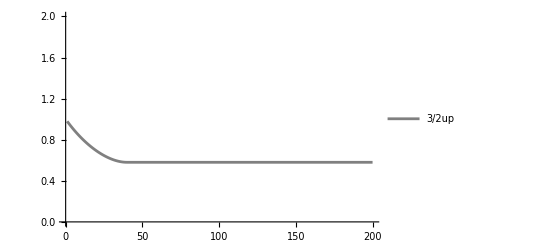

```mathematica
ListPlot[Chop[(1.5*SqueezeListBox[[1,1]])/1,10^-7],PlotRange->{{0,200},{0,2}},Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[(1.5*SqueezeListBox[[1,1]])/1,10^-7]
```

{0.979395,0.959427,0.940079,0.921332,0.90317,0.885578,0.868541,0.852046,0.836082,0.820635,0.805696,0.791255,0.777304,0.763834,0.750839,0.738312,0.726248,0.714644,0.703496,0.692802,0.682559,0.672769,0.66343,0.654546,0.646118,0.63815,0.630648,0.623617,0.617064,0.611,0.605432,0.600374,0.595838,0.591838,0.588393,0.585519,0.583237,0.58157,0.580542,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181,0.580181}

```mathematica
VPCIXnodeNew={0.9793948433877888,0.9594272274562079,0.940078608486477,0.9213315403028797,0.9031696398730471,0.8855775563483848,0.8685409434434621,0.852046435070332,0.8360816241605444,0.8206350446241242,0.8056961564112073,0.7912553336584277,0.7773038559186931,0.7638339024898111,0.7508385498746035,0.7383117724229284,0.726248446224446,0.7146443563402831,0.7034962074820411,0.6928016382681526,0.6825592392105025,0.6727685746088212,0.6634302085567958,0.6545457352924287,0.6461178141562012,0.638150209454399,0.630647835561862,0.6236168076389317,0.6170644983818069,0.6109996012745713,0.6054322008652473,0.6003738506481402,0.5958376592011362,0.5918383853004162,0.5883925428170962,0.5855185162918901,0.5832366881859865,0.5815695789206247,0.5805420009457709,0.5801812282217678,0.5801812282217671,0.5801812282217673,0.5801812282217665,0.580181228221767,0.5801812282217667,0.580181228221767,0.5801812282217667,0.5801812282217654,0.5801812282217659,0.580181228221766,0.5801812282217653,0.580181228221766,0.5801812282217657,0.5801812282217653,0.5801812282217652,0.5801812282217649,0.5801812282217647,0.5801812282217639,0.580181228221764,0.5801812282217633,0.5801812282217635,0.580181228221764,0.5801812282217629,0.5801812282217627,0.5801812282217631,0.5801812282217624,0.5801812282217618,0.5801812282217624,0.5801812282217618,0.580181228221762,0.580181228221762,0.5801812282217615,0.5801812282217618,0.5801812282217611,0.5801812282217609,0.5801812282217611,0.5801812282217609,0.5801812282217609,0.5801812282217598,0.58018122822176,0.5801812282217597,0.5801812282217601,0.5801812282217599,0.5801812282217598,0.5801812282217599,0.5801812282217595,0.5801812282217591,0.5801812282217599,0.5801812282217595,0.5801812282217591,0.5801812282217587,0.5801812282217585,0.5801812282217588,0.5801812282217582,0.5801812282217581,0.5801812282217578,0.5801812282217578,0.5801812282217578,0.5801812282217581,0.580181228221758,0.5801812282217577,0.5801812282217582,0.5801812282217584,0.5801812282217584,0.5801812282217582,0.5801812282217567,0.5801812282217571,0.5801812282217571,0.5801812282217571,0.5801812282217568,0.5801812282217571,0.5801812282217573,0.5801812282217571,0.5801812282217568,0.5801812282217568,0.5801812282217561,0.5801812282217569,0.5801812282217563,0.5801812282217568,0.5801812282217568,0.5801812282217564,0.5801812282217572,0.5801812282217569,0.580181228221756,0.5801812282217567,0.5801812282217567,0.5801812282217569,0.5801812282217571,0.5801812282217583,0.5801812282217574,0.5801812282217577,0.5801812282217579,0.5801812282217574,0.5801812282217573,0.5801812282217579,0.5801812282217579,0.5801812282217579,0.5801812282217578,0.5801812282217578,0.5801812282217574,0.5801812282217578,0.5801812282217583,0.5801812282217577,0.5801812282217577,0.5801812282217591,0.5801812282217587,0.5801812282217581,0.5801812282217584,0.580181228221758,0.580181228221758,0.5801812282217578,0.5801812282217578,0.5801812282217583,0.5801812282217588,0.580181228221758,0.5801812282217584,0.5801812282217587,0.5801812282217584,0.5801812282217582,0.5801812282217574,0.580181228221758,0.5801812282217578,0.580181228221758,0.580181228221758,0.5801812282217571,0.5801812282217587,0.5801812282217582,0.5801812282217583,0.5801812282217576,0.580181228221758,0.5801812282217579,0.5801812282217583,0.580181228221758,0.580181228221758,0.580181228221758,0.5801812282217584,0.5801812282217578,0.580181228221758,0.5801812282217581,0.5801812282217578,0.5801812282217582,0.5801812282217588,0.5801812282217592,0.5801812282217591,0.5801812282217584,0.5801812282217585,0.5801812282217584,0.5801812282217584,0.5801812282217593,0.5801812282217591,0.5801812282217588,0.5801812282217591,0.580181228221759,0.5801812282217593,0.5801812282217595,0.5801812282217595,0.5801812282217593,0.5801812282217594,0.5801812282217598,0.5801812282217597};
VPCIYnode={0.977709627758512,0.956165078274944,0.9353426414641257,0.9152201551656216,0.8957769515443097,0.8769938095314126,0.8588529131126772,0.8413378153090038,0.8244334077325888,0.8081258956389596,0.792402778432549,0.777252835621002,0.7626661182516705,0.7486339459031335,0.7351489093454882,0.722204879026085,0.7097970195828096,0.697921810635483,0.686577074158103,0.6757620087910865,0.6654772315141937,0.6557248271682335,0.6465084063879201,0.6378331725904173,0.6297059987554667,0.6221355148348218,0.6151322067427403,0.6087085280072706,0.6028790253061405,0.5976604792737197,0.5930720621495772,0.589135514047903,0.5858753398643861,0.5833190291074817,0.5814973012496308,0.5804443795470693,0.580198296681548,0.5808012360421424,0.5822999130003309,0.5847460011484877,0.5847460011484875,0.5847460011484873,0.5847460011484873,0.5847460011484868,0.5847460011484868,0.5847460011484865,0.5847460011484868,0.5847460011484864,0.5847460011484866,0.5847460011484862,0.5847460011484857,0.584746001148486,0.5847460011484855,0.5847460011484855,0.5847460011484851,0.5847460011484846,0.5847460011484846,0.5847460011484844,0.5847460011484842,0.5847460011484837,0.5847460011484839,0.5847460011484837,0.5847460011484834,0.584746001148483,0.5847460011484831,0.584746001148483,0.5847460011484826,0.5847460011484822,0.5847460011484822,0.584746001148482,0.584746001148482,0.5847460011484822,0.5847460011484822,0.5847460011484811,0.5847460011484811,0.5847460011484809,0.5847460011484806,0.584746001148481,0.5847460011484805,0.5847460011484804,0.5847460011484801,0.5847460011484797,0.5847460011484797,0.5847460011484791,0.5847460011484791,0.5847460011484793,0.5847460011484784,0.5847460011484782,0.5847460011484781,0.584746001148478,0.5847460011484777,0.5847460011484776,0.5847460011484776,0.5847460011484774,0.584746001148477,0.5847460011484771,0.584746001148477,0.5847460011484764,0.5847460011484764,0.5847460011484764,0.584746001148476,0.5847460011484755,0.5847460011484753,0.5847460011484755,0.5847460011484755,0.5847460011484751,0.5847460011484747,0.5847460011484744,0.5847460011484743,0.5847460011484744,0.5847460011484737,0.5847460011484737,0.5847460011484731,0.5847460011484731,0.5847460011484729,0.5847460011484727,0.5847460011484726,0.584746001148472,0.5847460011484724,0.5847460011484724,0.5847460011484726,0.5847460011484722,0.5847460011484724,0.584746001148472,0.5847460011484713,0.5847460011484713,0.5847460011484713,0.5847460011484706,0.5847460011484704,0.5847460011484704,0.58474600114847,0.58474600114847,0.5847460011484693,0.58474600114847,0.5847460011484702,0.5847460011484698,0.5847460011484691,0.5847460011484695,0.5847460011484693,0.5847460011484691,0.5847460011484691,0.5847460011484695,0.5847460011484693,0.5847460011484689,0.5847460011484691,0.5847460011484684,0.584746001148468,0.5847460011484684,0.5847460011484682,0.5847460011484682,0.5847460011484679,0.5847460011484671,0.5847460011484666,0.5847460011484669,0.5847460011484675,0.5847460011484671,0.5847460011484664,0.5847460011484669,0.5847460011484659,0.5847460011484656,0.5847460011484656,0.5847460011484655,0.5847460011484658,0.5847460011484662,0.5847460011484659,0.5847460011484658,0.5847460011484661,0.5847460011484645,0.5847460011484643,0.5847460011484641,0.5847460011484638,0.5847460011484641,0.5847460011484634,0.5847460011484639,0.5847460011484638,0.5847460011484638,0.5847460011484634,0.5847460011484631,0.5847460011484628,0.584746001148463,0.5847460011484628,0.5847460011484628,0.5847460011484631,0.5847460011484626,0.5847460011484621,0.5847460011484622,0.5847460011484609,0.5847460011484611,0.5847460011484611,0.5847460011484614,0.5847460011484611,0.5847460011484606,0.5847460011484602,0.5847460011484602,0.5847460011484595,0.58474600114846,0.5847460011484598,0.5847460011484593,0.5847460011484591,0.5847460011484591};
```

```mathematica
VPCIXnode={0.977709627758512,0.956165078274944,0.9353426414641257,0.9152201551656216,0.8957769515443097,0.8769938095314126,0.8588529131126772,0.8413378153090038,0.8244334077325888,0.8081258956389596,0.792402778432549,0.777252835621002,0.7626661182516705,0.7486339459031335,0.7351489093454882,0.722204879026085,0.7097970195828096,0.697921810635483,0.686577074158103,0.6757620087910865,0.6654772315141937,0.6557248271682335,0.6465084063879201,0.6378331725904173,0.6297059987554667,0.6221355148348218,0.6151322067427403,0.6087085280072706,0.6028790253061405,0.5976604792737197,0.5930720621495772,0.589135514047903,0.5858753398643861,0.5833190291074817,0.5814973012496308,0.5804443795470693,0.580198296681548,0.5808012360421424,0.5822999130003309,0.5847460011484877,0.5847460011484875,0.5847460011484873,0.584746001148487,0.5847460011484871,0.5847460011484868,0.5847460011484868,0.5847460011484864,0.5847460011484862,0.5847460011484862,0.5847460011484863,0.5847460011484857,0.5847460011484854,0.5847460011484851,0.5847460011484849,0.5847460011484844,0.5847460011484844,0.584746001148484,0.5847460011484843,0.5847460011484842,0.5847460011484842,0.5847460011484837,0.5847460011484824,0.5847460011484824,0.5847460011484829,0.5847460011484824,0.5847460011484823,0.584746001148481,0.5847460011484811,0.5847460011484805,0.584746001148481,0.5847460011484806,0.5847460011484802,0.5847460011484803,0.5847460011484794,0.5847460011484795,0.5847460011484794,0.5847460011484794,0.5847460011484801,0.5847460011484792,0.5847460011484787,0.5847460011484789,0.5847460011484792,0.5847460011484789,0.584746001148479,0.5847460011484796,0.5847460011484792,0.5847460011484789,0.5847460011484783,0.5847460011484776,0.5847460011484774,0.5847460011484773,0.5847460011484773,0.5847460011484773,0.5847460011484769,0.5847460011484757,0.5847460011484764,0.5847460011484757,0.5847460011484757,0.5847460011484751,0.5847460011484751,0.5847460011484752,0.5847460011484751,0.5847460011484742,0.5847460011484744,0.5847460011484742,0.5847460011484742,0.5847460011484739,0.5847460011484736,0.5847460011484727,0.5847460011484731,0.5847460011484724,0.5847460011484729,0.584746001148472,0.584746001148472,0.584746001148471,0.5847460011484718,0.5847460011484719,0.5847460011484721,0.5847460011484722,0.5847460011484719,0.5847460011484723,0.5847460011484724,0.5847460011484715,0.5847460011484708,0.5847460011484716,0.5847460011484712,0.5847460011484711,0.5847460011484705,0.5847460011484709,0.5847460011484704,0.5847460011484703,0.5847460011484713,0.5847460011484715,0.5847460011484711,0.5847460011484714,0.5847460011484714,0.5847460011484715,0.5847460011484718,0.5847460011484716,0.5847460011484716,0.5847460011484711,0.5847460011484703,0.5847460011484701,0.58474600114847,0.5847460011484702,0.5847460011484706,0.5847460011484699,0.5847460011484698,0.5847460011484705,0.5847460011484705,0.5847460011484709,0.5847460011484705,0.5847460011484705,0.5847460011484705,0.5847460011484709,0.5847460011484711,0.584746001148471,0.5847460011484704,0.5847460011484705,0.5847460011484712,0.5847460011484715,0.5847460011484719,0.5847460011484715,0.584746001148472,0.5847460011484708,0.5847460011484718,0.5847460011484705,0.5847460011484718,0.5847460011484711,0.5847460011484709,0.5847460011484715,0.5847460011484714,0.5847460011484715,0.5847460011484711,0.5847460011484711,0.5847460011484709,0.5847460011484704,0.5847460011484709,0.5847460011484709,0.5847460011484714,0.5847460011484711,0.5847460011484705,0.5847460011484713,0.5847460011484709,0.5847460011484709,0.5847460011484708,0.584746001148471,0.5847460011484706,0.584746001148471,0.5847460011484711,0.5847460011484709,0.5847460011484714,0.5847460011484718,0.5847460011484712,0.5847460011484704,0.5847460011484716,0.5847460011484711,0.5847460011484709,0.584746001148471,0.5847460011484706};
```

```mathematica
VPCIXsub={0.9788227553681041,0.9583864990629131,0.9386683657473401,0.9196470789462996,0.9013028998438031,0.8836175824929732,0.8665743352655945,0.850157788410263,0.8343539676301828,0.8191502736334795,0.8045354676511127,0.7904996629604142,0.7770343224965353,0.7641322626800383,0.7517876636371572,0.7399960860403589,0.7287544948514468,0.7180612903082539,0.7079163465596849,0.6983210584234452,0.6892783968170899,0.6807929734972682,0.6728711158353162,0.6655209524612588,0.6587525107242945,0.6525778270479028,0.6470110714040052,0.6420686872955221,0.6377695488232006,0.6341351366239719,0.6311897347083207,0.628960650497686,0.6274784606750973,0.6267772858193119,0.6268950972019081,0.6278740595967929,0.629760914492391,0.6326074087205469,0.6364707742369086,0.6414142656222881,0.6421871503468946,0.6429610859117558,0.6437364643213916,0.6445136798114857,0.6452931286858354,0.6460752091467747,0.6468603211191526,0.6476488660678871,0.6484412468091655,0.6492378673153829,0.6500391325138981,0.6508454480797025,0.6516572202221482,0.652474855465829,0.6532987604257964,0.6541293415772376,0.654967005019809,0.6558121562367974,0.6566651998493169,0.6575265393657423,0.6583965769266258,0.6592757130453034,0.660164346344481,0.6610628732890237,0.6619716879152674,0.6628911815570965,0.6638217425691342,0.664763756047319,0.6657176035472099,0.6666836628003577,0.6676623074290667,0.6686539066599172,0.6696588250364119,0.6706774221310972,0.6717100522575659,0.6727570641827045,0.6738188008395873,0.6748955990414198,0.6759877891969241,0.6770956950275844,0.678219633287158,0.6793599134838726,0.680516837605715,0.6816906998492471,0.682881786352353,0.6840903749313361,0.6853167348227952,0.6865611264306752,0.6878238010789239,0.6891050007701405,0.6904049579506445,0.6917238952823344,0.6930620254217367,0.6944195508066529,0.6957966634507164,0.6971935447463026,0.698610365276074,0.7000472846335555,0.7015044512530402,0.702982002249168,0.7044800632664506,0.7059987483390736,0.7075381597612201,0.7090983879681847,0.7106795114285307,0.7122815965475086,0.7139046975819466,0.7155488565668062,0.7172141032535772,0.7189004550606508,0.7206079170358353,0.722336481831102,0.7240861296896515,0.7258568284454067,0.7276485335349431,0.7294611880219235,0.7312947226340197,0.7331490558123286,0.7350240937732421,0.7369197305827228,0.738835848242896,0.7407723167908984,0.7427289944098108,0.74470572755159,0.7467023510718238,0.7487186883761164,0.7507545515779286,0.7528097416676531,0.7548840486926768,0.7569772519481901,0.759089120178466,0.7612194117883284,0.7633678750644957,0.7655342484064822,0.767718260566727,0.7699196308996015,0.7721380696189228,0.77437327806361,0.7766249489710821,0.7788927667580214,0.7811764078080641,0.7834755407660321,0.7857898268382454,0.7881189200985179,0.790462467799371,0.7928201106880286,0.7951914833267448,0.7975762144170071,0.7999739271271586,0.8023842394229876,0.8048067644008264,0.8072411106226768,0.8096868824529404,0.8121436803962778,0.8146111014361415,0.8170887393735433,0.8195761851655974,0.8220730272634287,0.8245788519489677,0.8270932436702515,0.8296157853747819,0.8321460588405409,0.8346836450042614,0.837228124286564,0.8397790769135783,0.8423360832346654,0.8448987240359056,0.8474665808489843,0.8500392362551537,0.8526162741839427,0.8551972802063108,0.8577818418219441,0.8603695487404216,0.8629599931559824,0.8655527700156425,0.8681474772804119,0.870743716179416,0.8733410914566904,0.8759392116104651,0.8785376891247667,0.881136140693168,0.8837341874345446,0.8863314551007067,0.8889275742757872,0.8915221805672936,0.8941149147887251,0.896705423133691,0.8992933573414854,0.9018783748540475,0.9044601389643024,0.9070383189558762,0.9096125902341426,0.9121826344486774,0.9147481396070656,0.9173088001802328,0.9198643171991048,0.9224143983430309,0.9249587580196322,0.9274971174364975,0.930029204664615};
```

```mathematica
VPCIYsub={0.9788227553681041,0.9583864990629131,0.9386683657473401,0.9196470789462996,0.9013028998438031,0.8836175824929732,0.8665743352655945,0.850157788410263,0.8343539676301828,0.8191502736334795,0.8045354676511127,0.7904996629604142,0.7770343224965353,0.7641322626800383,0.7517876636371572,0.7399960860403589,0.7287544948514468,0.7180612903082539,0.7079163465596849,0.6983210584234452,0.6892783968170899,0.6807929734972682,0.6728711158353162,0.6655209524612588,0.6587525107242945,0.6525778270479028,0.6470110714040052,0.6420686872955221,0.6377695488232006,0.6341351366239719,0.6311897347083207,0.628960650497686,0.6274784606750973,0.6267772858193119,0.6268950972019081,0.6278740595967929,0.629760914492391,0.6326074087205469,0.6364707742369086,0.6414142656222881,0.6421805133836058,0.6429347171847304,0.6436775401133664,0.6444096506015558,0.6451317221677796,0.645844433157012,0.6465484664788194,0.6472445093435838,0.64793325299694,0.6486153924525149,0.6492916262230533,0.6499626560500256,0.6506291866318004,0.6512919253504781,0.6519515819974806,0.6526088684979845,0.653264498634291,0.653919187768237,0.6545736525627367,0.6552286107025487,0.6558847806143754,0.6565428811863813,0.6572036314872445,0.6578677504848324,0.6585359567645986,0.6592089682478243,0.6598875019097781,0.6605722734979258,0.661263997250273,0.6619633856139597,0.662671148964209,0.663387995323731,0.6641146300826992,0.6648517557193959,0.6656000715216469,0.6663602733091398,0.6671330531567494,0.6679190991189695,0.6687190949555614,0.6695337198585404,0.6703636481805909,0.6712095491650386,0.672072086677482,0.6729519189391889,0.6738496982623823,0.6747660707875118,0.6757016762226308,0.6766571475849807,0.6776331109449035,0.6786301851721798,0.6796489816849117,0.6806901042010581,0.6817541484927196,0.6828417021432984,0.6839533443076309,0.6850896454751939,0.6862511672365066,0.6874384620528208,0.6886520730292046,0.6898925336911343,0.6911603677646777,0.6924560889603948,0.6937802007610345,0.6951331962131403,0.6965155577226582,0.6979277568546436,0.6993702541371689,0.7008434988695167,0.7023479289347558,0.7038839706168025,0.7054520384220319,0.7070525349055564,0.7086858505022391,0.7103523633625275,0.7120524391932088,0.7137864311031437,0.7155546794540747,0.7173575117165857,0.719195242331278,0.7210681725752461,0.7229765904339256,0.7249207704783718,0.7269009737480512,0.7289174476391956,0.7309704257987958,0.7330601280242816,0.7351867601689592,0.7373505140532445,0.7395515673817742,0.7417900836664035,0.7440662121551777,0.7463800877673005,0.7487318310341502,0.7511215480463728,0.7535493304071117,0.7560152551913779,0.7585193849116199,0.7610617674895015,0.7636424362339277,0.7662614098253346,0.7689186923062564,0.7716142730782058,0.7743481269048604,0.7771202139215746,0.7799304796512296,0.7827788550264226,0.7856652564179856,0.7885895856698498,0.7915517301402368,0.7945515627491778,0.7975889420323428,0.8006637122011682,0.8037757032092612,0.8069247308250699,0.8101105967107727,0.8133330885073913,0.816591979926067,0.819887030845475,0.8232179874153531,0.8265845821660776,0.8299865341242665,0.8334235489343456,0.8368953189860309,0.840401523547685,0.8439418289054667,0.8475158885082288,0.8511233431181013,0.854763820966683,0.8584369379167718,0.8621422976295745,0.8658794917372936,0.8696481000210352,0.8734476905939348,0.877277820089434,0.8811380338545958,0.8850278661483901,0.8889468403448277,0.8928944691408729,0.8968702547690051,0.9008736892143439,0.9049042544362229,0.9089614225941047,0.9130446562777227,0.9171534087413329,0.9212871241419647,0.9254452377815391,0.9296271763527437,0.9338323581885319,0.9380601935151219,0.942310084708357,0.9465814265533166,0.950873606507018,0.9551860049640952,0.9595179955253051,0.9638689452687217,0.9682382150234845,0.9726251596459619,0.9770291282981638,0.9814494647282865,0.9858855075532283};
```

```mathematica
OATnode={0.9802971230620083,0.9611772981038769,0.9426244258751326,0.9246233068609195,0.9071596147873929,0.8902198725950994,0.8737914308121137,0.8578624482691841,0.8424218751094261,0.8274594380552388,0.812965627905129,0.7989316892431124,0.7853496123534243,0.7722121273433381,0.7595127004872253,0.7472455328154847,0.7354055609827934,0.7239884604613546,0.7129906511164679,0.7024093052339817,0.6922423580820225,0.6824885211029998,0.6731472978463109,0.6642190027675581,0.6557047830365643,0.6476066435141509,0.6399274750767129,0.6326710864882078,0.6258422400414749,0.6194466912150364,0.6134912326178805,0.6079837425234615,0.6029332383255763,0.5983499352831083,0.5942453109583292,0.5906321757947565,0.58752475032604,0.5849387495573616,0.582891475115966,0.5814019158282564,0.580490857448102,0.5801810023352942,0.580497099965376,0.5814660892432203,0.5831172536939087,0.5854823907167837,0.5885959962134439,0.5924954660394443,0.5972213158842649,0.6028174213568024,0.6093312802463464,0.6168142991443731,0.6253221068534152,0.6349148972790103,0.6456578048031678,0.6576213154771265,0.6708817177524494,0.6855215968982523,0.7016303777351836,0.7193049208609686,0.7386501781565451,0.7597799140557928,0.7828174998469852,0.807896789163365,0.8351630838288413,0.8647742003701113,0.8969016488088852,0.9317319368307431,0.9694680141179595,1.0103308735640728,1.0545613282954085,1.1024219859524114,1.15419944458249,1.2102067378256018,1.2707860609040733,1.336311813341624,1.407193999430196,1.4838820333520417,1.5668690026842544,1.656696451924752,1.7539597568743654,1.8593141714170662,1.9734816407321834,2.0972584895744184,2.231524111360511,2.3772508038754427,2.5355149210219077,2.7075095378686354,2.894558859133949,3.0981346401761085,3.319874935776359,3.561605546988317,3.82536460191908,4.113430784750614,4.428355821373186,4.773001943106252,5.150585186367466,5.564725551090431,6.019505240769136,6.5195364504648445,7.07004046631206,7.676940204078875,8.346968761736635,9.087797112838906,9.908184750705907,10.818157942469416,11.829221311424142,12.954609793424474,14.209589683145914,15.61181959680712,17.181784858090605,18.94332223353903,20.92425632858366,23.157174607623226,25.680375327447436,28.539032222696527,31.786632304346227,35.486759655812385,39.715320057901096,44.56333062411028,50.14043816332264,56.57938364747346,64.04170357743162,72.72506033267501,82.87273459160292,94.78601103898205,108.8404697655863,125.50759906785436,145.38373033260225,169.22915438518962,198.02155534784475,233.0298222324435,275.917241340034,328.88764471939146,394.8953150609765,477.9510761609103,583.5760906551583,719.4869203757607,896.650439439197,1130.9442332029635,1445.834214608648,1876.8110817491875,2478.96759261212,3340.392244197993,4606.7891078286775,6528.818922056366,9558.033385370323,14553.69564628871,23263.018508349203,39542.330299802954,72837.39294515038,149685.11820393938,360207.5633184436,1.110338510737475*^6,5.343220378212298*^6,7.35916298399124*^7,2.4867625171315024*^12,1.393497494862875*^8,7.349355699926771*^6,1.3732716174845593*^6,422477.6042417418,170062.9639634373,81017.60572041626,43322.85200755762,25199.84295941052,15627.160955526695,10191.049864072758,6921.297081568648,4860.40891637428,3510.071129374628,2595.891389847131,1959.4581999070972,1505.560659783522,1174.9536482734572,929.6411642059318,744.5994629201646,602.9560460896985,493.0933033178359,406.8598387043552,338.43825322077487,283.61233610676925,239.28310967646223,203.1433009278103,173.45467319520657,148.89335281132583,128.44085271928662,111.30627917111002,96.87011972345417,84.64316410181937,74.2361663229819,65.33721805604185,57.69471708310816,51.1044360647044,45.399624397177945,40.44337354724626,36.122685597202,32.3438334892845,29.028708164178514,26.111925021493057,23.538518506780044};
```

```mathematica
OAT={0.9822579553251243,0.9650717750838005,0.9484271018796095,0.9323104450008798,0.916709157319973,0.9016114146122843,0.8870061972383578,0.8728832741430146,0.8592331891357294,0.8460472494267329,0.8333175164035265,0.8210367986427498,0.8091986471626856,0.7977973529322154,0.786827946662781,0.7762862009210318,0.7661686346112635,0.7564725198887364,0.7471958915774739,0.7383375591792989,0.7298971215748078,0.7218749845317762,0.7142723811522522,0.7070913954064949,0.7003349889200396,0.6940070311997184,0.6881123335055613,0.682656686598375,0.6776469026176178,0.673090861371193,0.6689975613482328,0.6653771757981095,0.6622411142540763,0.6596020899185113,0.6574741933690358,0.6558729730912525,0.6548155233950125,0.6543205803274459,0.6544086262581438,0.6551020038804792,0.6564250404489104,0.6584041831560173,0.6610681466460031,0.664448073764451,0.6685777107585676,0.6734935982692482,0.6792352795977203,0.6858455278869118,0.6933705940331436,0.701860477339448,0.7113692211403709,0.7219552358723975,0.7336816523375658,0.7466167082140192,0.7608341712106899,0.7764138026487755,0.7934418656859215,0.8120116828863798,0.8322242483894338,0.8541889005473435,0.8780240616029616,0.9038580517670048,0.9318299859488728,0.9620907624076895,0.9948041537392946,1.0301480119200856,1.0683156006132977,1.1095170696342058,1.1539810883993598,1.2019566573876554,1.2537151191605,1.3095523933741746,1.3697914635281487,1.4347851469967363,1.5049191842685612,1.5806156883631761,1.662337001218532,1.7505900105783965,1.8459309887113324,1.948971023347648,2.0603821217475593,2.1809040810752993,2.3113522325625073,2.452626183675145,2.6057197021003358,2.7717319083833525,2.9518799711216466,3.147513530548924,3.3601311140710077,3.591398852003773,3.8431718548215845,4.1175186763735825,4.416749362872776,4.743447677599162,5.100508199372317,5.491179122885095,5.9191117458355835,6.388417817532314,6.903736153868346,7.470310203774298,8.094078594425978,8.78178110168964,9.541083007659093,10.380721442996787,11.310678099212623,12.34238367486747,13.48896064136061,14.76551244498755,16.189469188910497,17.78100227477834,19.563523577786242,21.564288677670618,23.81512873294174,26.353342116128722,29.22278539422886,32.47521427764514,36.17193964057314,40.385882827401076,45.20413985055241,50.73119805080513,57.0929945559747,64.44206800608359,72.96414004232136,82.8865804044892,94.48937287605943,108.11942897383615,124.20942230128566,143.3027842177881,166.0871800912803,193.43978181724913,226.48913411653479,266.7006461244709,315.9961574042699,376.92333877519553,452.899083671546,548.564561614425,670.311802326933,827.0789314066067,1031.5751966733217,1302.2098388311965,1666.2038158384776,2164.7474481354375,2861.8127501046006,3859.736057411181,5327.872297859853,7557.714638540953,11074.633948772227,16878.864678642334,27005.2896053636,45947.42883728161,84717.38634498915,174268.42865147788,419775.7506462107,1.2952292910511722*^6,6.23911869278278*^6,8.601606754660287*^7,2.909501382359858*^12,1.632020581517836*^8,8.616008776683943*^6,1.611584704947155*^6,496298.3739698946,199983.57175064913,95370.20633360195,51050.83717827883,29726.272939441627,18453.73925359293,12047.31907964774,8190.914925287136,5758.351970231383,4163.223064645533,3082.4600817906603,2329.452859491519,1791.9835146997689,1400.1877560524435,1109.2356246778131,889.5870789856398,721.313960515022,590.6874177468503,488.06961100779245,406.57865251848114,341.22417168591005,288.3362076015534,245.18090674672686,209.6975480695198,180.31579885974696,155.82690970240648,135.2917297796294,117.97421389139953,103.29281064495869,90.78454711992222,80.07823166560803,70.87427495533854,62.92936287937961,56.0447197365706,50.05705168191082,44.8315077230505,40.2561713566703,36.23772207741932,32.69799731841558,29.57125206595694};
```

```mathematica
TACTnode={0.9802977700347852,0.9611823210576924,0.9426408776212081,0.9246611504269824,0.9072313378237347,0.8903401263003587,0.8739766900479641,0.8581306896529987,0.8427922699722608,0.827952057229676,0.8136011553639473,0.7997311416457491,0.7863340615728911,0.7734024230418646,0.7609291897843722,0.7489077740478268,0.7373320284894097,0.7261962372440496,0.7154951061177559,0.70522375184898,0.6953776903722753,0.6859528240104538,0.6769454275137404,0.6683521328572642,0.6601699127015985,0.652396062415159,0.645028180552169,0.6380641476757748,0.6315021034129067,0.6253404216258093,0.6195776835850505,0.6142126490304236,0.6092442250098236,0.6046714323920674,0.6004933699581081,0.5967091759864129,0.5933179872627196,0.5903188954623181,0.5877109008746633,0.585492863465821,0.583663451304287,0.5822210864102346,0.5811638881275598,0.5804896141622109,0.5801955994793524,0.580278693305817,0.5807351945429688,0.5815607859581556,0.5827504675900435,0.5842984898736032,0.586198287063657,0.5884424116106265,0.5910224702173014,0.5939290623795983,0.5971517222857867,0.6006788650155779,0.6044977380407839,0.608594379080617,0.6129535814046918,0.6175588677028943,0.6223924736508462,0.6274353422901497,0.6326671303115222,0.6380662272739075,0.6436097887118619,0.6492737839752324,0.6550330595084348,0.6608614181110806,0.6667317145275732,0.6726159674919643,0.6784854881077731,0.6843110241739315,0.690062919781509,0.6957112892066448,0.7012262038191421,0.7065778904204735,0.7117369391269853,0.7166745186321286,0.7213625964238555,0.7257741613082934,0.729883445406559,0.73366614265549,0.7370996207617198,0.740163123537142,0.7428379605861778,0.7451076814233856,0.7469582312739393,0.748378086047388,0.7493583642729513,0.7498929141364039,0.7499783741566167,0.7496142064745779,0.7488027021886323,0.7475489586449722,0.7458608290701392,0.7437488454000465,0.7412261156060508,0.7383081972317678,0.7350129492246894,0.7313603644658068,0.7273723856616876,0.7230727074620681,0.7184865677992532,0.7136405315128431,0.7085622693257847,0.7032803351786421,0.6978239448129921,0.6922227583280309,0.6865066692240682,0.6807056022002934,0.6748493217004856,0.6689672529074757,0.663088316583469,0.6572407788466381,0.6514521166718048,0.6457488996110636,0.6401566879542663,0.6346999472939681,0.6294019792281628,0.6242848677295167,0.6193694405332902,0.6146752447484886,0.6102205357777781,0.606022278540634,0.6020961599295924,0.5984566113895584,0.5951168404926752,0.5920888703838707,0.5893835859923273,0.5870107859391294,0.5849792391186879,0.5832967449887346,0.5819701966683248,0.5810056460133184,0.5804083699121279,0.5801829371195116,0.5803332750212484,0.580862735796382,0.5817741615153393,0.5830699477806875,0.5847521055819436,0.5868223210962515,0.5892820132224521,0.5921323886869998,0.5953744946061788,0.5990092684301828,0.6030375852309567,0.6074603023274054,0.6122783012688902,0.6174925272210962,0.6231040258176664,0.6291139775567265,0.6355237298339126,0.6423348267130146,0.6495490365422061,0.6571683775283024,0.6651951413838484,0.6736319151623464,0.682481601395836,0.6917474366465128,0.701433008580378,0.7115422716661408,0.7220795615970022,0.7330496085265661,0.7444575492031624,0.7563089380793602,0.7686097574655105,0.7813664267878768,0.7945858110032732,0.8082752282132792,0.8224424565119625,0.8370957400917266,0.852243794622351,0.8678958119085676,0.8840614638215778,0.9007509054897539,0.9179747777234153,0.9357442086379195,0.9540708144284583,0.9729666992387432,0.9924444540543006,0.9877135386768804,0.9683766813490807,0.9496186262704104,0.9314268992032271,0.9137895131105818,0.8966949690217605,0.8801322559401296,0.8640908498598002,0.8485607119461873,0.8335322859244587,0.8189964947090486,0.8049447362968329,0.7913688789362696,0.77826125557469,0.7656146575760442,0.7534223276917241,0.7416779522575895,0.7303756525810492,0.7195099754729889};
```

```mathematica
TACT={0.9822588647939818,0.9650788986488256,0.9484506478043504,0.9323651211852926,0.9168138008636106,0.9017886515648581,0.8872821293117892,0.873287189286708,0.8597972929825394,0.8468064147011809,0.8343090474463417,0.8223002082467462,0.8107754429342329,0.7997308303898751,0.7891629862597359,0.7790690661302301,0.7694467681412173,0.7602943350029011,0.7516105553703099,0.74339476451655,0.7356468442331423,0.7283672218725756,0.7215568684347172,0.7152172955849413,0.7093505514777572,0.7039592152454471,0.6990463899967545,0.6946156941560778,0.6906712509591162,0.6872176759064359,0.6842600619623431,0.6818039622727663,0.6798553701629093,0.6784206961634452,0.677506741803275,0.677120669897757,0.6772699710541492,0.677962426111281,0.6792060642286206,0.6810091163414775,0.6833799637046111,0.6863270812566373,0.6898589755529637,0.6939841170361698,0.6987108664405463,0.7040473951625016,0.7100015994714854,0.7165810084876069,0.7237926859127748,0.7316431255725835,0.7401381409066329,0.7492827486358373,0.759081046936632,0.7695360885637452,0.7806497494849851,0.7924225937226932,0.8048537352361171,0.817940697825696,0.8316792741922796,0.8460633854395885,0.86108494246404,0.8767337108293913,0.8929971808709803,0.9098604449117378,0.9273060835952049,0.9453140634449839,0.9638616478403803,0.9829233236495374,1.0024707457790696,1.0224727018782593,1.0428950993717914,1.0637009768838541,1.0848505419549765,1.1063012367390463,1.1280078331003862,1.1499225582100008,1.1719952513677723,1.1941735523571586,1.2164031211759034,1.238627888487505,1.2607903356124048,1.2828318023353797,1.3046928202582757,1.3263134688879088,1.3476337511314846,1.368593984390258,1.38913520301071,1.409199567484578,1.4287307754972203,1.4476744697189223,1.465978637124768,1.4835939946218275,1.500474355861484,1.5165769743201891,1.5318628580411011,1.5462970518364405,1.5598488832469708,1.5724921691293927,1.5842053803808216,1.5949717629957574,1.604779414368423,1.613621314483611,1.6214953123646545,1.628404068850065,1.6343549574344565,1.639359925519871,1.6434353189676394,1.6466016733084121,1.6488834753509494,1.650308899224245,1.650909521089837,1.650720016872812,1.6497778473836568,1.6481229351440279,1.6457973370948098,1.6428449171629114,1.639311022403831,1.6352421661303063,1.6306857210940335,1.625689625418042,1.620302103592016,1.6145714044512856,1.6085455576710617,1.6022721499285084,1.5957981215230816,1.5891695839055904,1.5824316582530358,1.5756283349425413,1.5688023535255744,1.561995102584425,1.5552465386664005,1.548595123337135,1.542077777271119,1.5357298502035903,1.5295851055007113,1.5236757180621243,1.5180322842486622,1.5126838425252953,1.5076579035223374,1.5029804882435265,1.4986761731848373,1.494768141169938,1.4912782367540292,1.488227025094731,1.4856338532336535,1.4835169127724432,1.4818933029592394,1.4807790932220382,1.480189384190594,1.4801383662331453,1.4806393744927218,1.481704939332197,1.4833468309778846,1.4855760969747813,1.4884030908146544,1.4918374897461901,1.4958882992898528,1.5005638413105826,1.505871721580139,1.5118187714892413,1.5184109568047308,1.525653243899635,1.5335494104048264,1.5421017822769034,1.5513108721486324,1.5611748834575803,1.5716890295898556,1.5828445945753304,1.594627627748574,1.607017113057534,1.6199823748594122,1.6334793620028414,1.6474452715567944,1.6617907120869333,1.6763882608611602,1.691055920725022,1.7055339913440166,1.7194553651700275,1.7323150203253221,1.7434591090581772,1.7521375439660538,1.7576693485814907,1.7596944435610622,1.7583450013615327,1.754177224121265,1.7479313526150433,1.7403155631712532,1.731905568301054,1.723132432248213,1.7143071187713461,1.7056512775304624,1.697323177490908,1.6894368652363716,1.6820755963503642,1.6753010771689691,1.6691598083153134,1.663687464156562,1.6589119462089772,1.6548555368823725,1.6515364370777863};
```

```mathematica
TACTIZIZ={0.9805971200276382,0.9617805395530205,0.9435379576456422,0.9258575557805215,0.9087280000934765,0.8921384426077058,0.876078521504062,0.860538360495692,0.8455085673563036,0.8309802316401327,0.8169449216208182,0.8033946804656804,0.790322021651424,0.7777199236170182,0.7655818236393857,0.7539016109076085,0.7426736187616121,0.7318926160517144,0.7215537975660922,0.7116527734640681,0.7021855576443007,0.693148554968433,0.6845385472526364,0.6763526779318471,0.66858843529443,0.6612436341786295,0.6543163960166345,0.6478051271075289,0.641708494997002,0.636025402839675,0.6307549616194413,0.6258964601045978,0.621449332418005,0.6174131231083361,0.613787449616963,0.6105719620465175,0.6077663001519051,0.6053700474929697,0.6033826827103592,0.6018035279127445,0.6006316941947248,0.5998660243407683,0.5995050328115399,0.5995468431552231,0.5999891230379126,0.6008290171439271,0.6020630782587431,0.60368719691397,0.6056965300449434,0.6080854291864819,0.6108473688103392,0.6139748754879124,0.6174594586425426,0.6212915437358144,0.6254604088099022,0.6299541253812397,0.6347595047474359,0.6398620508269722,0.6452459206972688,0.650893894028443,0.6567873526247554,0.6629062712805397,0.6692292211296506,0.6757333866146873,0.6823945971221694,0.6891873742207333,0.696084995300041,0.7030595742377734,0.7100821595211669,0.717122850018992,0.7241509283418206,0.73113501144598,0.7380432178339535,0.7448433503863483,0.7515030935343429,0.7579902231538014,0.7642728272410879,0.7703195351245518,0.7760997526836453,0.7815839007985439,0.7867436540457758,0.791552176497768,0.7959843513835969,0.8000170013305129,0.8036290959353056,0.8068019435139179,0.8095193640473257,0.8117678405800411,0.8135366466308396,0.8148179475375157,0.8156068740707663,0.815901567106944,0.8157031926344086,0.8150159268711588,0.8138469117797451,0.8122061817659645,0.810106562827861,0.8075635458691761,0.8045951362957017,0.8012216823647687,0.7974656850498277,0.7933515924083243,0.7889055815985041,0.7841553317782746,0.7791297911377209,0.7738589412693264,0.7683735619709896,0.76270499941272,0.7568849403858837,0.7509451951020496,0.7449174907257534,0.7388332775205858,0.7327235491697545,0.7266186785089823,0.7205482695891106,0.7145410266748988,0.7086246404913683,0.7028256917545295,0.6971695717734332,0.6916804196879925,0.686381075713878,0.6812930496027676,0.6764365033935062,0.6718302474264993,0.6674917485186422,0.6634371491474316,0.659681296468414,0.6562377799872501,0.6531189767238506,0.6503361027384608,0.647899269935556,0.6458175471183837,0.6440990243323271,0.6427508796068259,0.6417794472810949,0.6411902871765807,0.6409882539572751,0.641177566096279,0.6417618739421839,0.6427443264510062,0.6441276362177333,0.6459141425055489,0.648105872030019,0.6507045973097577,0.6537118924441527,0.6571291862226699,0.6609578125090779,0.6651990578777782,0.6698542065085036,0.6749245823700887,0.6804115887441219,0.6863167451551653,0.692641721786144,0.699388371465505,0.7065587593168967,0.7141551901623542,0.7221802337659174,0.7306367479958142,0.739527899968689,0.7488571852172649,0.758628444890546,0.7688458809488364,0.7795140692473468,0.7906379703002047,0.8022229373615455,0.8142747212180563,0.8267994706978771,0.8398037272548426,0.853294410878443,0.8672787926035801,0.8817644452176225,0.8967591565806112,0.9122707751269845,0.9283069242833141,0.9448744437555632,0.9619782064376297,0.9796183268430082,0.9977824959467163,1.0164195973062107,1.0353070189231373,1.0525834206829723,1.0493267863931695,1.0317233904202199,1.0134667634036023,0.9955524426464719,0.978132158599385,0.9612436287904847,0.9448958321462637,0.929088026561379,0.9138156439769096,0.8990725303970823,0.8848519244028029,0.8711469299014187,0.8579507620858379,0.8452568823507052,0.8330590747701563,0.8213514898553566,0.8101286689368289,0.799385556442888,0.7891175041965854};
```

```mathematica
OATIZIZ={0.9805964333978658,0.9617752032453395,0.9435204611488802,0.9258172653576384,0.9086515543476346,0.8920101229161663,0.8758806007160385,0.860251433169946,0.845111864715857,0.8304519243445528,0.8162624134006686,0.8025348956287262,0.7892616894557862,0.7764358625125747,0.7640512284052763,0.7521023457607837,0.7405845195790011,0.7294938049370379,0.7188270131017289,0.7085817201190885,0.6987562779620424,0.6893498283312307,0.6803623192179342,0.6717945243533144,0.6636480656843504,0.6559254390341913,0.6486300431232898,0.6417662121477575,0.6353392521331225,0.6293554813051663,0.6238222747451125,0.6187481136241741,0.6141426393428251,0.6100167129331926,0.6063824801191734,0.603253442468479,0.6006445351142611,0.5985722115716867,0.5970545362272579,0.5961112851364231,0.595764055828612,0.5960363868890103,0.5969538881638332,0.5985443825215259,0.6008380601970159,0.6038676468511031,0.6076685865933482,0.6122792413458875,0.617741108068917,0.6240990555279218,0.631401582460005,0.6397010991941233,0.649054235000163,0.6595221736874012,0.671171020247277,0.6840722016421087,0.6983029051847076,0.7139465583383775,0.7310933541980659,0.7498408273974982,0.770294485731122,0.7925685033915817,0.8167864824125017,0.8430822896831578,0.8716009777782487,0.9024997988364294,0.9359493218416197,0.9721346649297626,1.0112568557821187,1.0535343347989818,1.0992046176033772,1.1485261355360472,1.2017802752090219,1.2592736409301133,1.3213405669464395,1.3883459100421573,1.4606881571344346,1.538802887224891,1.623166632477674,1.7143011894234048,1.8127784384632615,1.9192257381259008,2.034331970096165,2.158854322105966,2.2936259086118356,2.4395643440847854,2.597681401068241,2.769093905348201,2.9550360441386068,3.1568732907244765,3.376118181255772,3.6144482172199845,3.873726211590224,4.156023449008921,4.463646092144009,4.799165339378416,5.165451925482085,5.565715659556217,6.0035508165950615,6.482988344453357,7.0085560216786655,7.585347909484017,8.219104690340878,8.916306785149287,9.684282501613549,10.531333901766132,11.466883603132624,12.501646366325518,13.647830097285333,14.919371836435921,16.332215458780354,17.904639217030343,19.65764298470124,21.61540717299755,23.80583789799753,26.26121617980253,29.01897290803562,32.12261618842911,35.62284371605458,39.578880276487226,44.060089692731225,49.1479219202333,54.938270031723704,61.54432909893349,69.10007011921147,77.76446785668693,87.72665247268819,99.21219169297424,112.49075324882295,127.8854459639713,145.78419028987386,166.65352098984658,191.05526743914265,219.6665749077354,253.30369588374901,292.9498482404323,339.7871327698045,395.23191005041406,460.97197966027045,539.0021280795537,631.6517674145633,741.5940462001464,871.8195404972327,1025.5491967725627,1206.0510294444402,1416.315117621939,1658.5364552304372,1933.3642689449566,2238.9135686183918,2569.6161686996174,2915.122608040386,3259.6339695651964,3582.1727989825013,3858.2691692839317,4063.2140226863985,4176.412192271006,4185.687482180769,4090.0808042947388,3900.070485063612,3635.1287377526432,3319.5626923979876,2978.086598028819,2632.3536251654623,2299.0237902841754,1989.295619797767,1709.4563682699204,1461.9347232311477,1246.4534238338229,1061.0461916575136,902.8442702853206,768.6269882329684,655.1736613037926,559.4666125872463,478.7916934093547,410.7732295439513,353.37010158140504,304.8509759122855,263.7601387542605,228.88079162953616,199.19962764498834,173.87459177119138,152.20657631212828,133.61514783084587,117.61805788241347,103.81413323386155,91.8690924079773,81.50384500763647,72.48486862405258,64.61630792917171,57.73349222789604,51.69761637116848,46.3913732929633,41.71536384792489,37.58514121925443,33.92877345759992,30.68482937217489,27.80071071760507,25.231268052078253,22.937649359010464,20.886340018887278};
```

```mathematica
VPCIXIZIZ={0.9779198276748818,0.9565820855530196,0.935963412030492,0.9160419911054415,0.8967974996993318,0.878211061032718,0.8602652038657352,0.8429438274523428,0.8262321720953125,0.8101167952265785,0.7945855529750332,0.779627587221764,0.7652333181812593,0.7513944425868837,0.7381039376001868,0.7253560706069878,0.7131464151090566,0.7014718729691883,0.690330703320186,0.679722558505294,0.6696485274798345,0.6601111871719214,0.6511146623751974,0.6426646948295917,0.634768722238343,0.6274359680724508,0.6206775431288067,0.6145065599374563,0.6089382612588292,0.6039901640758285,0.5996822206712119,0.5960369985910807,0.5930798815343079,0.5908392934798996,0.5893469486748266,0.5886381304598991,0.5887520023180125,0.5897319549960027,0.591625994088384,0.5944871730902114,0.5945811453179254,0.5946753978539204,0.5947702261996911,0.5948659250864685,0.5949627880438436,0.5950611069710379,0.5951611717114833,0.5952632696313561,0.5953676852026664,0.5954746995915469,0.5955845902523254,0.5956976305279689,0.595814089257482,0.5959342303907943,0.5960583126117084,0.5961865889694041,0.5963193065190266,0.596456705971841,0.5965990213554283,0.5967464796843807,0.5968993006419312,0.5970576962729413,0.5972218706886515,0.5973920197835662,0.5975683309648474,0.59775098289457,0.5979401452451477,0.5981359784682609,0.598338633577552,0.5985482519453872,0.5987649651139142,0.5989888946206667,0.5992201518389165,0.5994588378329848,0.5997050432286775,0.5999588480990129,0.6002203218653787,0.600489523214237,0.6007665000294836,0.6010512893405554,0.6013439172863311,0.6016443990948854,0.6019527390791298,0.6022689306483324,0.6025929563355275,0.6029247878407665,0.6032643860901823,0.6036117013107808,0.6039666731208956,0.6043292306361769,0.604699292591012,0.6050767674752248,0.6054615536858813,0.6058535396940417,0.6062526042262305,0.6066586164604231,0.607071436236295,0.6074909142794709,0.6079168924395031,0.6083492039412552,0.6087876736493989,0.609232118345649,0.6096823470184014,0.6101381611643727,0.6105993551018404,0.6110657162950841,0.6115370256895503,0.612013058057305,0.6124935823522859,0.6129783620748511,0.6134671556451197,0.6139597167845395,0.6144557949051679,0.6149551355060537,0.6154574805761724,0.6159625690032748,0.616470136988047,0.61697991846296,0.6174916455151355,0.6180050488125856,0.618519858033147,0.619035802295438,0.6195526105911211,0.620070012217795,0.6205877372117953,0.6211055167801782,0.6216230837311926,0.6221401729024851,0.6226565215863296,0.6231718699511533,0.6236859614586207,0.6241985432755579,0.6247093666799962,0.6252181874606144,0.6257247663088676,0.6262288692031066,0.6267302677839933,0.6272287397205316,0.6277240690660406,0.6282160466034349,0.628704470179158,0.6291891450251561,0.6296698840683013,0.6301465082266772,0.6306188466921785,0.6310867371988949,0.6315500262767594,0.6320085694900124,0.6324622316599998,0.632910887071898,0.6333544196649826,0.6337927232060656,0.6342257014457846,0.6346532682574493,0.6350753477581788,0.6354918744121223,0.635902793115547,0.6363080592636648,0.6367076387990742,0.6371015082417217,0.6374896547003649,0.6378720758655092,0.6382487799838604,0.6386197858143532,0.6389851225658658,0.6393448298167557,0.6396989574163877,0.6400475653688856,0.6403907236993147,0.6407285123026252,0.64106102077561,0.6413883482322787,0.6417106031029797,0.6420279029177,0.6423403740739648,0.6426481515898068,0.6429513788422897,0.6432502072920991,0.6435447961947417,0.6438353122989071,0.644121929532578,0.644404828677485,0.6446841970325266,0.6449602280667845,0.6452331210627866,0.6455030807506845,0.6457703169339958,0.6460350441076337,0.6462974810688796,0.6465578505220151,0.646816378677323,0.6470732948451502,0.6473288310257506,0.6475832214956323,0.6478367023910984,0.6480895112897145,0.6483418867903568,0.6485940680926943,0.6488462945765425,0.6490988053820488};
```

```mathematica
VPCIYIZIZ={0.9779198276748818,0.9565820855530196,0.935963412030492,0.9160419911054415,0.8967974996993318,0.878211061032718,0.8602652038657352,0.8429438274523428,0.8262321720953125,0.8101167952265785,0.7945855529750332,0.779627587221764,0.7652333181812593,0.7513944425868837,0.7381039376001868,0.7253560706069878,0.7131464151090566,0.7014718729691883,0.690330703320186,0.679722558505294,0.6696485274798345,0.6601111871719214,0.6511146623751974,0.6426646948295917,0.634768722238343,0.6274359680724508,0.6206775431288067,0.6145065599374563,0.6089382612588292,0.6039901640758285,0.5996822206712119,0.5960369985910807,0.5930798815343079,0.5908392934798996,0.5893469486748266,0.5886381304598991,0.5887520023180125,0.5897319549960027,0.591625994088384,0.5944871730902114,0.5945787972623611,0.5946659375750694,0.5947487915140013,0.5948275613893785,0.5949024541090523,0.5949736809452403,0.5950414572952711,0.5951060024367276,0.5951675392773539,0.5952262941001183,0.5952824963038243,0.5953363781396701,0.5953881744441424,0.595438122368678,0.5954864611064759,0.5955334316168823,0.5955792763477656,0.5956242389562838,0.5956685640284637,0.595712496798007,0.5957562828647336,0.595800167913067,0.5958443974309748,0.5958892164297679,0.5959348691651575,0.595981598859965,0.5960296474288758,0.596079255205627,0.5961306606729981,0.5961841001959911,0.5962398077585552,0.5962980147042124,0.5963589494809489,0.5964228373906967,0.596489900343746,0.5965603566184117,0.5966344206262704,0.5967123026832607,0.5967942087869581,0.5968803404002883,0.5969708942419685,0.5970660620839199,0.5971660305559224,0.5972709809577237,0.5973810890788583,0.5974965250263632,0.5976174530606093,0.5977440314394362,0.5978764122707589,0.5980147413738259,0.5981591581492648,0.5983097954580686,0.5984667795096403,0.5986302297590175,0.5988002588133678,0.5989769723478544,0.5991604690309386,0.5993508404591862,0.5995481711016247,0.5997525382536871,0.5999640120007708,0.6001826551914148,0.6004085234200968,0.6006416650196419,0.6008821210631976,0.6011299253757539,0.601385104555147,0.6016476780024783,0.6019176579618806,0.6021950495695318,0.6024798509118212,0.6027720530925555,0.6030716403090677,0.6033785899371092,0.6036928726243642,0.6040144523924269,0.6043432867470784,0.6046793267966714,0.6050225173784406,0.6053727971925211,0.6057300989434788,0.6060943494891138,0.606465469996311,0.6068433761036969,0.6072279780908393,0.607619181053743,0.6080168850863616,0.6084209854678435,0.6088313728552417,0.6092479334813706,0.6096705493575304,0.6100990984807708,0.6105334550453886,0.6109734896583355,0.6114190695582087,0.6118700588374865,0.6123263186676733,0.6127877075270165,0.613254081430428,0.613725294161291,0.614201197504761,0.614681641482239,0.6151664745866224,0.6156555440180078,0.6161486959194516,0.6166457756124448,0.6171466278317318,0.6176510969591114,0.6181590272558556,0.6186702630933877,0.6191846491818603,0.619702030796278,0.620222253999814,0.620745165863966,0.6212706146852114,0.621798450197824,0.6223285237825137,0.6228606886705668,0.6233948001431586,0.6239307157255345,0.6244682953757452,0.6250074016676453,0.6255478999678644,0.6260896586064704,0.6266325490410611,0.6271764460140208,0.6277212277027016,0.6282667758622861,0.6288129759611173,0.6293597173082807,0.6299068931732368,0.6304544008973312,0.6310021419969929,0.6315500222584922,0.6320979518240869,0.632645845269443,0.6331936216722267,0.6337412046717497,0.6342885225196051,0.6348355081212101,0.6353820990682254,0.6359282376617992,0.6364738709266284,0.6370189506158255,0.6375634332066152,0.6381072798868846,0.6386504565326295,0.6391929336763693,0.6397346864665979,0.6402756946183701,0.6408159423551283,0.6413554183418981,0.6418941156099922,0.6424320314733727,0.6429691674368483,0.6435055290962804,0.644041126031003,0.6445759716886679,0.6451100832627307,0.6456434815628271};
```

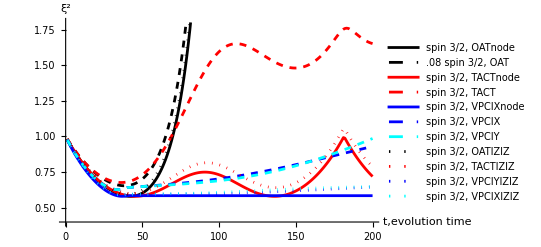

```mathematica
Plot3half2Newparameter=ListPlot[{OATnode,OAT,TACTnode,TACT,VPCIXnode,VPCIXsub,VPCIYsub,OATIZIZ,TACTIZIZ,VPCIYIZIZ,VPCIXIZIZ},Joined->{True,True,True,True,True,True},PlotRange->{{0,200},{0.4,1.8}},PlotLegends->{"spin 3/2, OATnode",.08"spin 3/2, OAT","spin 3/2, TACTnode","spin 3/2, TACT","spin 3/2, VPCIXnode","spin 3/2, VPCIX","spin 3/2, VPCIY","spin 3/2, OATIZIZ","spin 3/2, TACTIZIZ","spin 3/2, VPCIYIZIZ","spin 3/2, VPCIXIZIZ"},AxesLabel->{"t,evolution time","ξ^2"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed},Blue,{Blue,Dashed},{Cyan,Dashed},{Black,Dotted},{Red,Dotted},{Blue,Dotted},{Cyan,Dotted}},AxesStyle->Directive[Thick,Black]]
```

```mathematica
Export["E:\\desksave2\\Astro\\spin squeezing\\picture save\\Plot3half2Newparameter.pdf",Plot3half2Newparameter]
```

E:\desksave2\Astro\spin squeezing\picture save\Plot3half2Newparameter.pdf

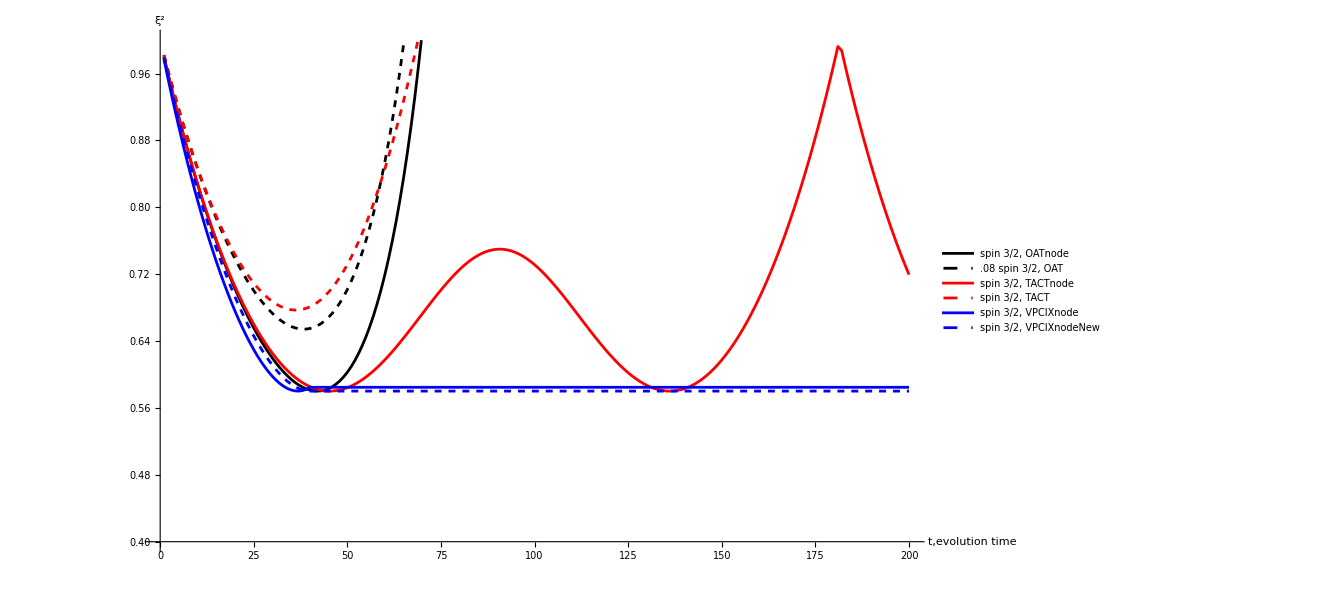

```mathematica
Plot7half2WithTACT=ListPlot[{OATnode,OAT,TACTnode,TACT,VPCIXnode,VPCIXnodeNew},Joined->{True,True,True,True,True,True},PlotRange->{{0,200},{0.4,1}},PlotLegends->{"spin 3/2, OATnode",.08"spin 3/2, OAT","spin 3/2, TACTnode","spin 3/2, TACT","spin 3/2, VPCIXnode","spin 3/2, VPCIXnodeNew","spin 3/2, VPCIYnode","spin 3/2, VPCIY"},AxesLabel->{"t,evolution time","ξ^2"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed},Blue,{Blue,Dashed},Purple,{Purple,Dashed},Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

## sequence with decay, master equation backup 5/2

```mathematica
Clear["Global`*"];
(*定义 fidelity 函数*)Fidelity[rho_,sigma_]:=Module[{sqrtRho,inner},sqrtRho=MatrixPower[rho,1/2];
inner=sqrtRho.sigma.sqrtRho;
(Tr[MatrixPower[inner,1/2]])^2]

(*示例：两个 2x2 密度矩阵*)


dim=5/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
(*Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});*)
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;


IniPhi={{1},{0},{0},{0},{0},{0}};

StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi//FullSimplify
StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(χ*(3*Iz3half2.Iz3half2+η*(Iplus3half2.Iplus3half2+Iminus3half2.Iminus3half2)/2))*t].StateθϕInitial[θ,ϕ]

DensityMatrixEvo[t_,θ_,ϕ_]:=StateEvo[t,θ,ϕ].ConjugateTranspose[StateEvo[t,θ,ϕ]]


(*StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].StateθϕInitial[θ,ϕ]
StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t].StateθϕInitial[θ,ϕ]

StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(3Iz3half2.Iz3half2+η/2(Ix3half2.Ix3half2-Iy3half2.Iy3half2))*t].StateθϕInitial[θ,ϕ]
StateEvo2[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].css[θ,ϕ]*)
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
θ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
(*ϕ2[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*Print[N[xVal]];
Print[yVal//FullSimplify];*)
If[First[Flatten[N[xVal]]]==0&&First[Flatten[N[yVal]]]!=0,Pi/2,N[First[Flatten[ArcTan[yVal/xVal]]]]]
]*)
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]
]
ϕ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]]]
]
In1[state_]:=N[-Ix3half2*Sin[ϕ1DM[state]]+Iy3half2*Cos[ϕ1DM[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1DM[state]]Cos[ϕ1DM[state]]-Iy3half2*Cos[θ1DM[state]]Sin[ϕ1DM[state]]+Iz3half2*Sin[θ1DM[state]]]
(*In1[state_]:=N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]
In1n2plusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]*)
In1n2plusSqure[state_]:=Tr[(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=Tr[(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=Tr[(In1[state].In2[state]+In2[state].In1[state]).state]
ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )^1/((Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2)]]]
(*ξSqure[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )/Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]*)
(*ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]*)
ξbottomF[state_]:=N[First[Flatten[ Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]




d=6;
L0=Table[0 ,{i,d*d},{j,d*d}];
Do[L0[[i,j]]=Subscript[L, (i-1)*d*d+j],{i,1,d*d},{j,1,d*d}];
L0List=Flatten[L0];
H0=Table[0 ,{i,d},{j,d}];
ρ0=Table[0 ,{i,d},{j,d}];
Do[H0[[i,j]]=Subscript[H, (i-1)*d+j];ρ0[[i,j]]=Subscript[ρ, (i-1)*d+j],{i,1,d},{j,1,d}](*Print[L0//MatrixForm]; Print[H0//MatrixForm; Print[ρ0//MatrixForm]*)

(*RHLIST=-I*(H0.ρ0-ρ0.H0)+gamma*(PauliMatrix[3].ρ0.PauliMatrix[3]-ρ0);

RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));

RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
*)
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
(*RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γ, z](KroneckerProduct[Iz3half2,Identit yMatrix[2]].ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));*)
RHBlockList=Flatten[Transpose[RHLIST]];
ρBlockList=Flatten[Transpose[ρ0]]; (*Print[ρBlockList]; Print[RHBlockList//MatrixForm]*)
LHBlockList=L0.Transpose[ρBlockList];(*Print[LHBlockList//MatrixForm]; Print[LHBlockList-RHBlockList//MatrixForm//FullSimplify]*)
Solvelist=LHBlockList-RHBlockList; (*Print[Solvelist//FullSimplify//MatrixForm]; Print[Solvelist[[1]]//FullSimplify//MatrixForm]*)
L1=Table[0 ,{i,d*d},{j,d*d}];
Do[L1[[i,j]]=Coefficient[Solvelist[[i]],Subscript[ρ, j],1],{i,1,d*d},{j,1,d*d}];
Do[L1[[i]]=Sort[L1[[i]]],{i,1,d}] ;(*Print[L1//MatrixForm];*)
L1=Flatten[L1];(*Print[L1//MatrixForm];*)
Do[L1[[i]]=Solve[L1[[i]]==0,L0List],{i,1,d*d*d*d}];
L1resultList=Flatten[Sort[L1]];(*Print[L1resultList]*)
Do[L1resultList[[i]]=L1resultList[[i,2]],{i,1,d*d*d*d}];(*Print[L1resultList]*)
L1resultList=N[Partition[L1resultList,d*d]];

(*HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}});

HMATRIX=Iz3half2.Iz3half2;*)
(*HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})HMATRIX=IdentityMatrix[6];

=Ix3half2.Ix3half2-Iy3half2.Iy3half2;*)
HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}});

Print[HMATRIX//MatrixForm];

Do[
Subscript[H, (i-1)*d+j]=HMATRIX[[i,j]];
,{i,1,d},{j,1,d}]
Ω=0;
β=1;
Subscript[γI, z]=0.1;
Subscript[γI, x]=0;
Subscript[γS, z]=0;
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

General::stop: 在本次计算中，Solve::svars 的进一步输出将被抑制.

(0 | 1/2 √5 ⅇ^(-ⅈ ϕ11) | 0 | 0 | 0 | 0
1/2 √5 ⅇ^(ⅈ ϕ11) | 0 | √2 ⅇ^(-ⅈ ϕ2) | 0 | 0 | 0
0 | √2 ⅇ^(ⅈ ϕ2) | 0 | (3 ⅇ^(-ⅈ ϕ3))/2 | 0 | 0
0 | 0 | (3 ⅇ^(ⅈ ϕ3))/2 | 0 | √2 ⅇ^(-ⅈ ϕ4) | 0
0 | 0 | 0 | √2 ⅇ^(ⅈ ϕ4) | 0 | 1/2 √5 ⅇ^(-ⅈ ϕ5)
0 | 0 | 0 | 0 | 1/2 √5 ⅇ^(ⅈ ϕ5) | 0)

```mathematica
(*UEvo=MatrixExp[-I*({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})*t1];
UEvo=MatrixExp[-I*Iz3half2.Iz3half2*t1];
*)
UEvo=MatrixExp[-I*({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})*t1];

(*IniState={{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}};
IniState=StateθϕInitial[Pi/2,Pi/2];
MatrixExp[I*Ix3half2*Pi/2].

{{1/(√2)},{0},{0},{0},{0},{1/(√2)}}
*)
IniState=StateθϕInitial[Pi/2,Pi/2];

EvoState=UEvo.IniState;

dt=0.01;
number1=10 ;
number=10;
totNumber=20;

CtTable=Table[0,{i,0,totNumber}];
(*aaa={{-1.2269057307077853,-1.530271689622663,4.403178377782569,-2.1619964633463926,3.019285024330924,0.18671168010212336,2.24547354378955,2.3388848317093425,2.6974809976000182,1.4377723136713092,0.5971588127479954,1.6631273953201644,1.2984892721243106,2.7426862671553067,1.9213539249618128,0.28355197915516506,2.697327892631874,2.4128954690633266,3.3887193065301515,1.4062078776692593},{0.38971079214838644,0.8485854886614761,0.8123951187874039,0.49267689130473835,0.7161633658278421,0.9908357390648255,1.9709238529011097,2.481869004133195,2.669114789122622,1.4778308380709557,1.4509089068416614,0.8499308790558611,1.7668802465691478,2.213534167514667,2.302893623582208,0.950179141614754,2.8302170880251287,1.9131315037676258,2.762117114238386,0.9995746838624946},{1.5521916924169323,1.5001241952759967,1.4437565558622376,1.5082963760931176,1.4790000666254395,4.046022129883772,2.4338181488669752,1.81487095939405,2.803404669588847,1.8058615427980191,2.8397084407896935,0.7573783856015055,1.7013951623819112,1.921142166425751,2.6694006734625395,0.96691784978275,3.21087919463566,2.721007402015986,3.128933508852332,0.531927349222495},{2.792174241535089,2.2738119577431037,2.147252024033043,2.1860623838295146,1.9421223753440708,2.709264035021671,2.58234308046476,2.078965074818801,2.8717725648335426,0.10627284893373101,2.8971231802638275,0.8227483577933628,2.0525532832817452,1.8854170693583594,2.722732623526076,1.1299076451112828,3.0856562669075664,2.7272761089709245,3.4538311579317655,-0.2699028491166735},{2.0687470187361665,1.7501021842101512,1.3582640614465173,2.2632451841765837,-1.0933677578165,4.04399853459381,4.10186595823439,-0.9620252987963807,3.7961632230498976,-0.39162765173692193,3.5324116623589763,-0.46662748134286147,4.701923117961375,-1.3880241425068913,3.3002603044162813,4.480461741824306,3.1448568966379744,3.3618694281822084,3.1293644301066728,0.11761243267943922}};

ϕ1Table=aaa[[1]];
ϕ2Table=aaa[[2]];
ϕ3Table=aaa[[3]];
ϕ4Table=aaa[[4]];
ϕ5Table=aaa[[5]];
*)
(*
{{3.7598902694445195,3.590977996574284,3.6593033003131428,3.601574441551117,3.176425192783814,3.124159192784357,0.8668561522001461,1.1289914586518943,0.7690378643693294,1.155205488420319,0.6993012350173551,1.358995094803202,2.2368354524205865,1.8330965924310973,2.191771312016466,3.0069178203569695,0.19490072121916358,3.081703205320813,1.4910988051563496,2.333564873847301},{3.2338669678576615,3.2645210129119997,-2.847289039532734,2.795965377961795,1.6200799948407374,1.9486547459750563,0.9977135721021035,1.6599043925282562,2.596796983170254,1.2990610714137318,0.2465193697652257,1.7523268549563022,2.288096462081925,1.6425328617532782,2.010883079241734,3.0715886923245126,0.08015035130703918,2.2268784119059397,0.8815712812255629,1.411485931550104},{1.560503927579032,1.5681129257466213,1.5721423882831909,2.0104474632953027,1.4489917019883487,1.6065196616493758,0.9363287842327614,1.4274583885523784,2.111371728710777,1.4222388036264504,-0.34684203636652144,1.5316112833987825,2.058913587696896,1.142876729105029,2.1347915914125313,3.393562895097861,0.08715394593607506,0.6004575302217319,0.18010309948507697,1.8495121975415776},{-0.11686145918881286,-0.16936101498732814,5.925812460892263,1.9079670308928742,0.13512292961329964,1.3889432546952403,0.9335010666040517,1.3125171768090906,2.380013834940242,0.6577750630229433,3.2536289165930565,1.0726074329754267,2.969277005205355,0.9844369561361441,3.0937785984014416,2.981520053434312,-0.3785333317879225,0.12754100725064887,0.4215290291591254,1.294397031314035},{0.3464574550566395,0.21987738530618595,0.468874662714021,0.19587600141707107,-0.03413648609501152,2.774212079360055,3.2054518843929953,-0.3961931986956304,2.763968388043665,-1.991665819948444,3.8302844976077486,4.149635120805216,3.6617898429347555,-1.1622690362456662,3.7760424129362464,3.490004836173542,0.7585010271839616,1.6214779052721147,-1.205421030531137,3.9878447324096253}};

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415};*)

(*
ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415};

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table=Table[2.581055163108225,{i,0,totNumber}];
ϕ2Table=Table[3.9125553774195057,{i,0,totNumber}];
ϕ3Table=Table[0.8791183546201431,{i,0,totNumber}];

2.581055163108225,3.9125553774195057,0.8791183546201431

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};

ϕ1Table={3.2206143,3.2206143,3.2206143,3.2206143,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={2.9763257,2.9763257,2.9763257,2.9763257,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={0.1652670,0.1652670,0.1652670,0.1652670,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={−0.0790217,−0.0790217,−0.0790217,−0.0790217,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={1.4267131148515073,1.4267131148515073,1.4267131148515073,1.4267131148515073,1.4267131148515073,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.697953795751256,1.697953795751256,1.697953795751256,1.697953795751256,1.697953795751256,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.9324372999121295,1.9324372999121295,1.9324372999121295,1.9324372999121295,1.9324372999121295,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.44753115273887,2.44753115273887,2.44753115273887,2.44753115273887,2.44753115273887,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={1.7559400582907179,1.7559400582907179,1.7559400582907179,1.7559400582907179,1.7559400582907179,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={0.852725571715359,0.852725571715359,0.852725571715359,0.852725571715359,0.852725571715359,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.5701670771764915,1.5701670771764915,1.5701670771764915,1.5701670771764915,1.5701670771764915,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.8830887797333844,1.8830887797333844,1.8830887797333844,1.8830887797333844,1.8830887797333844,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.49933418078428,2.49933418078428,2.49933418078428,2.49933418078428,2.49933418078428,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={1.8230861347331135,1.8230861347331135,1.8230861347331135,1.8230861347331135,1.8230861347331135,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={3.117956388261617,3.117956388261617,3.117956388261617,3.117956388261617,3.117956388261617,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.31571912918101797,0.31571912918101797,0.31571912918101797,0.31571912918101797,0.31571912918101797,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={0.03157985243228989,0.03157985243228989,0.03157985243228989,0.03157985243228989,0.03157985243228989,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={0.5643541348473571,0.5643541348473571,0.5643541348473571,0.5643541348473571,0.5643541348473571,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={0.27027492808228937,0.27027492808228937,0.27027492808228937,0.27027492808228937,0.27027492808228937,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={-1.4938004545715677,-1.4938004545715677,-1.4938004545715677,-1.4938004545715677,-1.4938004545715677,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.8355471112600075,0.8355471112600075,0.8355471112600075,0.8355471112600075,0.8355471112600075,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5140903656371876,1.5140903656371876,1.5140903656371876,1.5140903656371876,1.5140903656371876,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.2551091259719245,2.2551091259719245,2.2551091259719245,2.2551091259719245,2.2551091259719245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={1.915070023105288,1.915070023105288,1.915070023105288,1.915070023105288,1.915070023105288,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={4.616491461962614,4.616491461962614,4.616491461962614,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.8272486038482931,0.8272486038482931,0.8272486038482931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5715189411737942,1.5715189411737942,1.5715189411737942,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.315366972872111,2.315366972872111,2.315366972872111,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={4.806923913246008,4.806923913246008,4.806923913246008,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={4.616491461962614,4.616491461962614,4.616491461962614,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={0.8272486038482931,0.8272486038482931,0.8272486038482931,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={1.5715189411737942,1.5715189411737942,1.5715189411737942,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={2.315366972872111,2.315366972872111,2.315366972872111,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={4.806923913246008,4.806923913246008,4.806923913246008,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
*)
(*IniStateBox={{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}};*)

IniStateBox={StateθϕInitial[Pi/2,Pi/2]};

fvaluebox={1};
SqueezeListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{i,number*totNumber}];
TargetStateBox={{{1},{0},{0},{0},{0},{0}},{{0},{1},{0},{0},{0},{0}},{{0},{0},{1},{0},{0},{0}},{{0},{0},{0},{1},{0},{0}},{{0},{0},{0},{0},{1},{0}},{{0},{0},{0},{0},{0},{1}}};
DM=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMList=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{l,totNumber}];

ϕ1Table={4.616491461962614,4.616491461962614,4.616491461962614,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.8272486038482931,0.8272486038482931,0.8272486038482931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5715189411737942,1.5715189411737942,1.5715189411737942,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.315366972872111,2.315366972872111,2.315366972872111,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={4.806923913246008,4.806923913246008,4.806923913246008,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


Do[
Do[
If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];
(*If[l==1,DM[[m,k]]={{0.06064613060530813-7.19910242530375*^-17 ⅈ,0.12209626438566488-0.030661048673710993 ⅈ,0.05277806578919029-0.08950977453873414 ⅈ,-0.08950968037760113-0.05277810030433395 ⅈ,0.030661064682025653+0.12209623840886856 ⅈ,-5.533503397246037*^-11-0.06064612703807027 ⅈ},{0.12209626438566476+0.03066104867371091 ⅈ,0.261312593640043+3.217912047936977*^-16 ⅈ,0.15150955446878536-0.15352303865369588 ⅈ,-0.15352283163318256-0.15150957635131984 ⅈ,4.5362024627890185*^-8+0.2613125494354407 ⅈ,0.030661046758808156-0.12209625723187398 ⅈ},{0.05277806578919005+0.08950977453873363 ⅈ,0.15150955446878497+0.15352303865369488 ⅈ,0.17804143246491294-1.3097162243624894*^-16 ⅈ,1.32887047519549*^-7-0.17804132352639723 ⅈ,-0.15352298638218315+0.15150955548938982 ⅈ,0.08950976922556535-0.052778062766428525 ⅈ},{-0.0895096803776005+0.05277810030433431 ⅈ,-0.1535228316331819+0.15150957635131987 ⅈ,1.3288704766873521*^-7+0.17804132352639712 ⅈ,0.1780412145880518+5.551115123125783*^-17 ⅈ,-0.15150957737188403-0.1535227793617031 ⅈ,0.05277809728156973+0.08950967506443834 ⅈ},{0.03066106468202596-0.12209623840886927 ⅈ,4.53620245459245*^-8-0.26131254943544285 ⅈ,-0.15352298638218356-0.15150955548939016 ⅈ,-0.15150957737188372+0.15352277936170242 ⅈ,0.26131250523085653-2.2811613709095013*^-16 ⅈ,-0.12209623125507962-0.030661062767121734 ⅈ},{-5.533525449918225*^-11+0.060646127038070506 ⅈ,0.03066104675880777+0.1220962572318738 ⅈ,0.08950976922556515+0.05277806276642822 ⅈ,0.05277809728156978-0.08950967506443769 ⅈ,-0.1220962312550793+0.030661062767121612 ⅈ,0.06064612347083336+5.833007687972014*^-17 ⅈ}},DM[[m,k]]=StateFinal;];
*)


(*If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];*)

DMList[[m,k]]=Flatten[Transpose[DM[[m,k]]]];
,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]

TargetStateDMBox=Table[0,{i,Length[TargetStateBox]}];
Do[
TargetStateDMBox[[i]]=TargetStateBox[[i]].ConjugateTranspose[TargetStateBox[[i]]];
,{i,1,Length[TargetStateDMBox]}]



FListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{j,1,Length[TargetStateBox]},{i,number}];

DMevolvemid=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMevolve=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
(*Print[FListBox];*)
Do[
Do[
ϕ11=ϕ1Table[[l]];
ϕ2=ϕ2Table[[l]];
ϕ3=ϕ3Table[[l]];
ϕ4=ϕ4Table[[l]];
ϕ5=ϕ5Table[[l]];
DMevolvemid[[m,k]]=N[MatrixExp[(L1resultList/. t->(i)*dt)*dt].DMList[[m,k]]];

DMevolve[[m,k]]=Transpose[Partition[DMevolvemid[[m,k]],d]];

SqueezeListBox[[m,k,i+(l-1)*number1]]=ξtopF[DMevolve[[m,k]]];
DMListBox[[m,k,l]]=DMevolve[[m,k]];
FListBox[[m,k,1,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[1]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[1]]]])^1;
FListBox[[m,k,2,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[2]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[2]]]])^1;
FListBox[[m,k,3,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[3]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[3]]]])^1;
FListBox[[m,k,4,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[4]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[4]]]])^1;
FListBox[[m,k,5,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[5]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[5]]]])^1;
FListBox[[m,k,6,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[6]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[6]]]])^1;
If[i==number1,StateFinal=DMevolve[[m,k]]];


DMList[[m,k]]=DMevolvemid[[m,k]];
(*If[Divisible[i,number1/printnumber],Print[i,"/",number1,"   m: ",m,"   k: ",k]];*)
,{i,1,number1}];

,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]
Print[l];
,{l,1,totNumber}]
```

Flatten::normal: Flatten[2.49816+1.73472×10^-18 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+6.72696×10^-19 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-4.99968×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

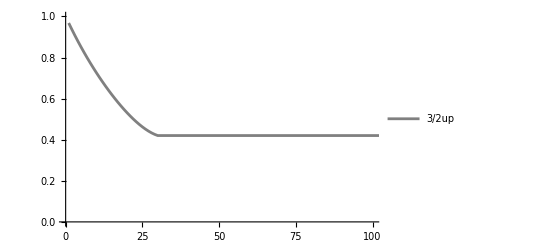

```mathematica
ListPlot[Chop[(2.5*SqueezeListBox[[1,1]])/1,10^-7],Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray},PlotRange->{{0,100},{0,1}}]
```

```mathematica
VPCIXnewNode={0.9681337436426091,0.937432378386872,0.907825268478373,0.8792483160563513,0.8516435990108671,0.8249590637106692,0.7991482694825601,0.7741701822248558,0.7499890150061943,0.7265741139401087,0.7038998880386871,0.6819457821378203,0.6606962923545101,0.6401410238850762,0.620274791283416,0.6010977616714519,0.5826156416299646,0.5648399087967512,0.5477880894595406,0.5314840836715277,0.5159585396351002,0.5012492792907438,0.4874017772083853,0.47446969500161573,0.46251547356388256,0.4516109854507333,0.4418382496928858,0.4332902112083173,0.42607158677292706,0.42029977919128225,0.42029977919128203,0.42029977919128225,0.4202997791912817,0.4202997791912817,0.42029977919128214,0.4202997791912817,0.42029977919128214,0.42029977919128186,0.42029977919128225,0.4202997791912818,0.4202997791912821,0.42029977919128136,0.4202997791912824,0.4202997791912821,0.42029977919128275,0.420299779191283,0.42029977919128236,0.420299779191283,0.42029977919128203,0.42029977919128153,0.4202997791912821,0.42029977919128225,0.4202997791912816,0.4202997791912813,0.420299779191281,0.4202997791912813,0.4202997791912818,0.42029977919128214,0.42029977919128125,0.42029977919128136,0.4202997791912817,0.4202997791912813,0.4202997791912807,0.4202997791912813,0.42029977919128114,0.4202997791912818,0.42029977919128125,0.4202997791912821,0.42029977919128125,0.4202997791912817,0.42029977919128153,0.4202997791912816,0.42029977919128203,0.42029977919128136,0.42029977919128214,0.4202997791912824,0.4202997791912822,0.42029977919128225,0.42029977919128353,0.42029977919128314,0.42029977919128203,0.4202997791912837,0.42029977919128264,0.42029977919128303,0.4202997791912828,0.4202997791912833,0.4202997791912828,0.4202997791912833,0.42029977919128386,0.42029977919128353,0.42029977919128314,0.4202997791912841,0.4202997791912847,0.4202997791912845,0.42029977919128547,0.42029977919128547,0.42029977919128575,0.420299779191286,0.42029977919128575,0.42029977919128714,0.42029977919128597,0.4202997791912865,0.4202997791912871,0.4202997791912872,0.4202997791912859,0.4202997791912876,0.42029977919128764,0.42029977919128736,0.4202997791912882,0.42029977919128764,0.42029977919128836,0.4202997791912887,0.42029977919128836,0.42029977919128764,0.4202997791912883,0.4202997791912877,0.42029977919128825,0.42029977919128886,0.42029977919129,0.42029977919128875,0.42029977919128836,0.4202997791912879,0.4202997791912889,0.42029977919128925,0.4202997791912897,0.4202997791912893,0.42029977919128925,0.4202997791912889,0.4202997791912887,0.4202997791912885,0.4202997791912885,0.4202997791912887,0.42029977919128925,0.4202997791912889,0.4202997791912885,0.42029977919128914,0.4202997791912898,0.42029977919128964,0.4202997791912899,0.4202997791912905,0.42029977919129047,0.4202997791912905,0.42029977919129036,0.42029977919129013,0.42029977919128986,0.4202997791912906,0.42029977919129047,0.4202997791912902,0.4202997791912904,0.4202997791912899,0.42029977919129097,0.42029977919129097,0.4202997791912904,0.4202997791912915,0.4202997791912918,0.420299779191292,0.42029977919129186,0.42029977919129213,0.42029977919129274,0.42029977919129247,0.4202997791912922,0.42029977919129263,0.42029977919129247,0.42029977919129297,0.42029977919129236,0.4202997791912916,0.4202997791912927,0.4202997791912927,0.42029977919129274,0.42029977919129335,0.42029977919129297,0.4202997791912926,0.4202997791912943,0.4202997791912938,0.4202997791912943,0.42029977919129513,0.4202997791912944,0.420299779191295,0.42029977919129496,0.42029977919129435,0.42029977919129385,0.42029977919129413,0.42029977919129424,0.42029977919129374,0.420299779191294,0.42029977919129385,0.4202997791912939,0.4202997791912946,0.42029977919129463,0.4202997791912939,0.42029977919129424,0.4202997791912949,0.42029977919129374,0.4202997791912943,0.420299779191294,0.42029977919129413,0.42029977919129513,0.4202997791912947,0.4202997791912956,0.4202997791912958};
VPCIXnewIZIZ={0.9693602016861569,0.9398835648587579,0.9115014193862452,0.8841516822710362,0.8577784904399828,0.832331890080989,0.8077675790464636,0.7840466993895052,0.7611356776012591,0.7390061105822303,0.7176346958104693,0.6970032045686465,0.6770984974629299,0.6579125818112743,0.6394427107988708,0.6216915245948065,0.604667233896918,0.5883838466205572,0.5728614386705873,0.5581264699319464,0.544212146779662,0.5311588325399831,0.5190145074251777,0.5078352795087031,0.4976859482971471,0.48864062238085987,0.4807833924953247,0.47420906108716054,0.46902392913702523,0.4653466405298172,0.4667530658946263,0.46816008421292,0.46956807460204186,0.4709774169008236,0.4723884913001469,0.47380167797067096,0.47521735668819665,0.4766359064571574,0.47805770513270174,0.47948312904184526,0.48091255260417526,0.4823463479525616,0.4837848845543563,0.48522852883352724,0.48667764379421413,0.48813258864612413,0.48959371843225713,0.49106138365938146,0.4925359299317126,0.49401769758823977,0.49550702134411595,0.4970042299365693,0.4985096457757201,0.500023584600773,0.5015463551419607,0.5030782587886633,0.504619589264123,0.506170632307136,0.5077316653611372,0.5093029572710674,0.5108847679884017,0.5124773482847522,0.5140809394743951,0.5156957731461314,0.5173220709048305,0.5189600441230432,0.5206098937030385,0.5222718098496371,0.5239459718541887,0.5256325478900483,0.5273316948198944,0.5290435580152393,0.5307682711884527,0.5325059562376426,0.5342567231046931,0.5360206696467996,0.5377978815217822,0.5395884320874899,0.5413923823155706,0.5432097807198937,0.5450406632998829,0.5468850534990051,0.548742962178681,0.5506143876077931,0.5524993154680611,0.5543977188754166,0.5563095584175993,0.5582347822080956,0.5601733259565849,0.5621251130559713,0.5640900546861356,0.5660680499344293,0.5680589859329941,0.570062738012886,0.5720791698750292,0.5741081337779204,0.5761494707420488,0.5782030107709062,0.5802685730884674,0.582345966392969,0.5844349891267944,0.5865354297622118,0.5886470671027254,0.5907696705997081,0.5929030006839907,0.5950468091120111,0.5972008393261373,0.59936482682867,0.6015384995690828,0.6037215783439288,0.6059137772088736,0.6081148039022573,0.6103243602795296,0.6125421427579104,0.6147678427705493,0.6170011472294635,0.6192417389964724,0.6214892973613393,0.62374349852627,0.6260040160959501,0.6282705215721955,0.6305426848523454,0.6328201747304553,0.635102659400347,0.6373898069595656,0.6396812859132555,0.6419767656769704,0.6442759170774414,0.6465784128502734,0.6488839281335927,0.6511921409566312,0.6535027327222453,0.6558153886823845,0.6581297984055203,0.6604456562350586,0.6627626617377842,0.6650805201414098,0.6673989427602779,0.6697176474083644,0.6720363587986756,0.674354808928247,0.6766727374478915,0.6789898920159564,0.681306028635358,0.6836209119731766,0.6859343156621883,0.6882460225836997,0.6905558251311467,0.6928635254539215,0.695168935680973,0.6974718781237541,0.6997721854581619,0.7020697008851379,0.7043642782696862,0.7066557822580757,0.7089440883730945,0.7112290830872364,0.7135106638737758,0.7157887392357276,0.7180632287127564,0.7203340628661341,0.7226011832419065,0.7248645423124687,0.7271241033968106,0.7293798405597509,0.7316317384904648,0.7338797923607412,0.73612400766339,0.7383644000312578,0.7406009950373895,0.7428338279768774,0.7450629436309703,0.7472883960140821,0.7495102481043213,0.7517285715582378,0.753943446410468,0.7561549607590103,0.7583632104368863,0.7605682986709007,0.7627703357283491,0.7649694385524047,0.7671657303870082,0.7693593403920831,0.7715504032498753,0.7737390587632615,0.7759254514468161,0.7781097301115301,0.7802920474439297,0.7824725595804867,0.7846514256780973,0.7868288074814693,0.7890048688882076,0.791179775512409,0.7933536942475437,0.7955267928294162,0.7976992393999445,0.7998712020725407,0.8020428484997943,0.8042143454442247,0.8063858583527503};
VPCIYnewIZIZ={0.9693602016861569,0.9398835648587579,0.9115014193862452,0.8841516822710362,0.8577784904399828,0.832331890080989,0.8077675790464636,0.7840466993895052,0.7611356776012591,0.7390061105822303,0.7176346958104693,0.6970032045686465,0.6770984974629299,0.6579125818112743,0.6394427107988708,0.6216915245948065,0.604667233896918,0.5883838466205572,0.5728614386705873,0.5581264699319464,0.544212146779662,0.5311588325399831,0.5190145074251777,0.5078352795087031,0.4976859482971471,0.48864062238085987,0.4807833924953247,0.47420906108716054,0.46902392913702523,0.4653466405298172,0.4667374435858507,0.4680974751743069,0.4694269425122899,0.47072606398827904,0.4719950688484609,0.4732341968823072,0.4744436981077764,0.47562383245651085,0.47677486945940395,0.47789708793288066,0.4789907756662297,0.48005622911033086,0.4810937530680902,0.48210366038688746,0.4830862716533434,0.4840419148906947,0.4849709252590459,0.48587364475877115,0.48675042193733453,0.4876016115997581,0.4884275745229952,0.489228677174423,0.4900052914346932,0.49075779432515054,0.4914865677400048,0.49219199818348636,0.4928744765121506,0.4935343976825274,0.494172160504286,0.4947881673990797,0.49538282416525115,0.49595653974853016,0.496509726018888,0.4970427975536925,0.4975561714272911,0.4980502670071593,0.49852550575674337,0.49898231104509416,0.49942110796343814,0.49984232314875654,0.50024638461449,0.5006337215884527,0.5010047643580469,0.5013599441228414,0.5016996928545933,0.5020244431647664,0.5023346281796048,0.5026306814227914,0.5029130367057337,0.5031821280255002,0.503438389470411,0.5036822551332885,0.5039141590323627,0.504134535039794,0.5043438168178003,0.5045424377623154,0.5047308309541485,0.5049094291175307,0.5050786645860053,0.5052389692755132,0.5053907746645949,0.5055345117815415,0.5056706111983762,0.5057995030314707,0.5059216169486447,0.506037382182526,0.5061472275499811,0.5062515814773663,0.5063508720313616,0.5064455269551358,0.506535973709541,0.5066226395190747,0.5067059514222634,0.506786336326174,0.5068642210646988,0.5069400324602646,0.5070141973885982,0.5070871428461644,0.5071592960198908,0.5072310843587686,0.5073029356469203,0.5073752780776959,0.5074485403283794,0.5075231516350531,0.5075995418671684,0.5076781416013675,0.5077593821940999,0.5078436958525632,0.5079315157034948,0.5080232758593574,0.5081194114814327,0.5082203588393699,0.5083265553667067,0.5084384397119037,0.5085564517844404,0.5086810327955099,0.5088126252928648,0.5089516731893886,0.5090986217849585,0.5092539177811696,0.509418009288545,0.5095913458258167,0.5097743783109113,0.5099675590432796,0.5101713416772301,0.5103861811859363,0.5106125338158206,0.510850857031023,0.5111016094476921,0.5113652507578627,0.5116422416427031,0.511933043674921,0.5122381192101841,0.5125579312673938,0.5128929433976956,0.5132436195421455,0.5136104238779525,0.5139938206532791,0.514394274010567,0.5148122477984322,0.5152482053721619,0.5157026093828911,0.5161759215555644,0.5166686024558227,0.5171811112459711,0.5177139054302107,0.5182674405893677,0.5188421701053614,0.5194385448756779,0.5200570130181532,0.5206980195664088,0.5213620061562642,0.522049410703531,0.5227606670735854,0.5234962047431426,0.5242564484546823,0.5250418178640122,0.5258527271814497,0.5266895848071472,0.5275527929610859,0.5284427473083012,0.52935983657991,0.5303044421905054,0.5312769378525521,0.5322776891883723,0.5333070533403554,0.5343653785800351,0.5354530039166691,0.5365702587059877,0.5377174622597651,0.5388949234568895,0.5401029403565899,0.5413417998145087,0.5426117771022829,0.5439131355313108,0.545246126081388,0.5466109870348592,0.5480079436169755,0.5494372076430986,0.550898977173405,0.5523934361757461,0.5539207541972729,0.5554810860454658,0.557074571479164,0.5587013349101956,0.5603614851161773,0.5620551149650557,0.563782301151916,0.5655431039486034,0.5673375669666432};
VPCIXnew={0.9718122523733753,0.9447072201105627,0.9186216318389788,0.893498442076559,0.8692864814064606,0.8459401613521462,0.8234192304787062,0.8016885787769246,0.7807180878765261,0.7604825250880753,0.7409614796923675,0.7221393402849858,0.7040053123444492,0.6865534755270752,0.6697828805020817,0.65369768542744,0.6383073324312872,0.6236267647050189,0.6096766850319786,0.5964838567682793,0.5840814484576464,0.5725094233969906,0.5618149755697545,0.5520530134247694,0.5432866929930981,0.5355880017968211,0.529038394902916,0.5237294843022435,0.5197637825362967,0.5172555011395938,0.520659136429188,0.5240621852786388,0.5274646527645108,0.5308665447321782,0.5342678677858238,0.5376686292750873,0.5410688372783787,0.5444685005828527,0.5478676286610771,0.5512662316444088,0.5546643202931243,0.5580619059633339,0.5614590005707383,0.5648556165512731,0.5682517668187069,0.571647464719272,0.5750427239833912,0.57843755867459,0.5818319831356928,0.5852260119323878,0.5886196597942858,0.5920129415535559,0.5954058720812926,0.5987984662217115,0.6021907387243144,0.6055827041741726,0.6089743769204488,0.612365771003341,0.6157569000795602,0.6191477773465524,0.622538415465584,0.625928826483894,0.6293190217560698,0.6327090118648361,0.6360988065414259,0.6394884145857387,0.6428778437864597,0.6462671008413341,0.6496561912777975,0.6530451193741454,0.6564338880814574,0.6598224989464603,0.6632109520355252,0.6665992458600144,0.6699873773031652,0.6733753415487086,0.6767631320114196,0.6801507402698033,0.6835381560010917,0.6869253669187667,0.6903123587127671,0.6936991149925864,0.6970856172334282,0.7004718447256074,0.7038577745273435,0.7072433814211418,0.7106286378738877,0.7140135140008464,0.7173979775336685,0.7207819937925802,0.7241655256628705,0.7275485335757943,0.730930975494018,0.7343128069017164,0.737693980799403,0.7410744477036023,0.7444541556514246,0.7478330502101254,0.751211074491705,0.7545881691726024,0.7579642725185074,0.7613393204143397,0.7647132463993965,0.7680859817076845,0.7714574553134289,0.774827593981747,0.7781963223244505,0.7815635628609603,0.7849292360842544,0.7882932605318338,0.7916555528615867,0.7950160279325041,0.798374598890153,0.801731177256786,0.8050856730260053,0.8084379947618241,0.811788049702022,0.8151357438656404,0.8184809821644773,0.8218236685183977,0.825163705974324,0.8285009968287088,0.8318354427533093,0.8351669449240745,0.8384954041529525,0.8418207210223907,0.8451427960223448,0.8484615296895605,0.8517768227489148,0.8550885762565785,0.8583966917447838,0.8617010713679473,0.8650016180499142,0.8682982356320885,0.8715908290222018,0.874879304343456,0.8781635690838343,0.8814435322452935,0.8847191044926102,0.887990198301628,0.8912567281066655,0.894518610446827,0.8977757641109849,0.9010281102811902,0.9042755726742695,0.9075180776813752,0.9107555545052615,0.9139879352950535,0.9172151552782943,0.9204371528900458,0.923653869898833,0.9268652515292332,0.9300712465809051,0.9332718075438575,0.9364668907097806,0.9396564562792635,0.9428404684647185,0.9460188955888429,0.9491917101784799,0.9523588890537147,0.9555204134120704,0.9586762689076801,0.961826445725297,0.9649709386490462,0.9681097471258028,0.9712428753231,0.9743703321814896,0.9774921314612682,0.9806082917835051,0.9837188366653116,0.9868237945493102,0.9899231988272423,0.9930170878577104,0.9961055049780116,0.9991884985100603,1.0022661217603848,1.0053384330142225,1.0084054955237038,1.0114673774901604,1.0145241520405865,1.0175758971982898,1.0206226958477769,1.0236646356939385,1.026701809215573,1.029734313613356,1.032762250752283,1.0357857270987267,1.038804853652149,1.0418197458716,1.0448305235970863,1.0478373109659305,1.0508402363242393,1.0538394321335907,1.0568350348730833,1.0598271849368537,1.0628160265272373,1.0658017075436728,1.068784379467532,1.0717641972429837,1.0747413191541058};
VPCIYnew={0.9718122523733753,0.9447072201105627,0.9186216318389788,0.893498442076559,0.8692864814064606,0.8459401613521462,0.8234192304787062,0.8016885787769246,0.7807180878765261,0.7604825250880753,0.7409614796923675,0.7221393402849858,0.7040053123444492,0.6865534755270752,0.6697828805020817,0.65369768542744,0.6383073324312872,0.6236267647050189,0.6096766850319786,0.5964838567682793,0.5840814484576464,0.5725094233969906,0.5618149755697545,0.5520530134247694,0.5432866929930981,0.5355880017968211,0.529038394902916,0.5237294843022435,0.5197637825362967,0.5172555011395938,0.5206305186537292,0.5239477296461005,0.5272071810594992,0.5304089454557974,0.5335531209569151,0.536639831172841,0.5396692251168005,0.542641477107705,0.5455567866600121,0.5484153783611202,0.5512175017364699,0.5539634311025027,0.55665346540765,0.559287928061527,0.5618671667525371,0.5643915532540466,0.5668614832193851,0.5692773759658362,0.5716396742478642,0.573948844019782,0.5762053741881181,0.5784097763538891,0.5805625845450253,0.5826643549392111,0.5847156655773685,0.5867171160680386,0.5886693272829286,0.5905729410438697,0.5924286198014398,0.594237046305535,0.5959989232681205,0.5977149730184521,0.5993859371510059,0.601012576166404,0.6025956691055744,0.6041360131774203,0.6056344233802614,0.6070917321172878,0.6085087888063111,0.6098864594840369,0.6112256264051331,0.6125271876363423,0.6137920566458642,0.6150211618882798,0.6162154463852362,0.6173758673021448,0.6185033955211111,0.6195990152103401,0.6206637233902328,0.6216985294963986,0.6227044549398073,0.6236825326642819,0.6246338067015553,0.6255593317240838,0.6264601725958331,0.6273374039212153,0.6281921095923833,0.6290253823350704,0.6298383232531479,0.630632041372099,0.6314076531815628,0.6321662821771385,0.6329090584016139,0.6336371179857756,0.6343516026889648,0.6350536594395368,0.635744439875381,0.6364250998846411,0.6370967991467845,0.6377607006741769,0.6384179703542837,0.639069776492641,0.6397172893567388,0.6403616807209349,0.6410041234125403,0.6416457908591837,0.6422878566376113,0.6429314940239949,0.6435778755459233,0.6442281725361474,0.644883554688219,0.6455451896141361,0.6462142424040894,0.6468918751884472,0.6475792467020623,0.6482775118510198,0.6489878212819382,0.649711320953914,0.6504491517132261,0.6512024488708983,0.6519723417832237,0.6527599534353473,0.6535664000280159,0.6543927905675923,0.6552402264594277,0.6561098011046951,0.6570025995007862,0.6579196978453719,0.6588621631441993,0.6598310528227562,0.6608274143418886,0.6618522848174478,0.6629066906440955,0.6639916471233342,0.6651081580958815,0.6662572155784676,0.6674397994051617,0.6686568768733127,0.6699094023942082,0.6711983171485435,0.6725245487467895,0.6738890108945571,0.6752926030630639,0.6767362101647691,0.678220702234295,0.6797469341147173,0.681315745149321,0.6829279588788981,0.6845843827447075,0.6862858077971592,0.688033008410329,0.6898267420023909,0.691667748762052,0.693556751381085,0.6954944547930341,0.6974815459182022,0.6995186934149772,0.7016065474376131,0.7037457394005142,0.7059368817491489,0.7081805677376334,0.7104773712130938,0.7128278464068698,0.7152325277326594,0.7176919295916507,0.7202065461847423,0.7227768513319227,0.7254032982988621,0.728086319630823,0.7308263269939168,0.7336237110238147,0.7364788411819462,0.7393920656192755,0.7423637110476965,0.7453940826191262,0.748483463812339,0.7516321163276091,0.7548402799892183,0.7581081726558553,0.7614359901390005,0.7648239061293034,0.7682720721310222,0.7717806174045604,0.7753496489171361,0.7789792513016407,0.7826694868236961,0.7864203953569654,0.7902319943667386,0.7941042789018203,0.7980372215947458,0.8020307726703536,0.8060848599627203,0.8101993889404913,0.8143742427405997,0.8186092822104136,0.8229043459582881,0.8272592504125504,0.8316737898889042,0.8361477366662652,0.8406808410710054};
VPCIXnode={0.9693957104448592,0.9402261460338447,0.912385814392786,0.8857784882627753,0.8603164612437487,0.8359198997373438,0.8125162838881507,0.7900399315160289,0.7684316001509516,0.7476381633429003,0.7276123584386228,0.7083126040093484,0.6897028860931674,0.6717527133966854,0.6544371425966888,0.637736875907907,0.6216384341519802,0.6061344096900381,0.5912238047821324,0.5769124622268397,0.5632135965297721,0.5501484353670987,0.537746982766155,0.526048917236367,0.5151046400659943,0.5049764911681874,0.495740152225807,0.48748625945705004,0.4803222511062604,0.4743744777516759,0.47437447775167646,0.4743744777516761,0.4743744777516763,0.47437447775167607,0.47437447775167646,0.4743744777516763,0.4743744777516755,0.4743744777516761,0.4743744777516765,0.47437447775167574,0.47437447775167596,0.47437447775167696,0.4743744777516764,0.4743744777516757,0.4743744777516764,0.4743744777516765,0.47437447775167596,0.4743744777516757,0.4743744777516757,0.47437447775167585,0.47437447775167485,0.47437447775167496,0.47437447775167557,0.47437447775167607,0.47437447775167624,0.47437447775167646,0.47437447775167596,0.47437447775167585,0.4743744777516765,0.47437447775167674,0.47437447775167624,0.4743744777516756,0.47437447775167557,0.4743744777516751,0.47437447775167557,0.47437447775167507,0.4743744777516745,0.47437447775167496,0.4743744777516751,0.47437447775167474,0.47437447775167374,0.4743744777516748,0.47437447775167474,0.4743744777516755,0.4743744777516741,0.4743744777516745,0.4743744777516752,0.47437447775167496,0.47437447775167496,0.47437447775167496,0.4743744777516761,0.4743744777516752,0.4743744777516745,0.47437447775167496,0.4743744777516752,0.4743744777516753,0.4743744777516759,0.4743744777516755,0.4743744777516751,0.47437447775167535,0.4743744777516748,0.4743744777516743,0.47437447775167496,0.4743744777516743,0.47437447775167507,0.4743744777516745,0.47437447775167585,0.47437447775167557,0.474374477751675,0.47437447775167596,0.4743744777516761,0.47437447775167674,0.4743744777516774,0.4743744777516767,0.47437447775167785,0.47437447775167724,0.4743744777516776,0.47437447775167785,0.47437447775167785,0.47437447775167696,0.4743744777516763,0.47437447775167757,0.47437447775167646,0.4743744777516767,0.4743744777516761,0.47437447775167696,0.4743744777516768,0.47437447775167735,0.4743744777516773,0.47437447775167646,0.4743744777516768,0.47437447775167707,0.4743744777516775,0.4743744777516775,0.4743744777516775,0.4743744777516766,0.47437447775167807,0.47437447775167735,0.47437447775167696,0.47437447775167646,0.4743744777516779,0.47437447775167674,0.4743744777516773,0.4743744777516764,0.4743744777516767,0.47437447775167674,0.4743744777516768,0.4743744777516765,0.4743744777516772,0.4743744777516776,0.47437447775167685,0.4743744777516767,0.47437447775167807,0.4743744777516782,0.47437447775167885,0.4743744777516774,0.4743744777516774,0.4743744777516778,0.47437447775167696,0.47437447775167757,0.4743744777516779,0.4743744777516778,0.4743744777516779,0.4743744777516787,0.47437447775167885,0.47437447775167946,0.4743744777516803,0.47437447775167946,0.4743744777516798,0.47437447775168,0.4743744777516809,0.4743744777516796,0.47437447775167974,0.47437447775167974,0.47437447775168,0.4743744777516811,0.47437447775168096,0.47437447775168096,0.4743744777516805,0.47437447775168,0.4743744777516806,0.47437447775168146,0.4743744777516823,0.47437447775168307,0.47437447775168273,0.4743744777516832,0.4743744777516829,0.47437447775168345,0.4743744777516839,0.47437447775168373,0.47437447775168406,0.47437447775168445,0.47437447775168395,0.4743744777516828,0.474374477751684,0.4743744777516839,0.47437447775168395,0.47437447775168495,0.474374477751684,0.47437447775168484,0.4743744777516865,0.4743744777516852,0.47437447775168556,0.4743744777516859,0.47437447775168556,0.4743744777516865,0.47437447775168584,0.4743744777516865,0.4743744777516867,0.474374477751687};
```

```mathematica
VPCIXsub={0.9730621483977192,0.947468291339752,0.9231234873172149,0.8999416205586537,0.8778446889793641,0.8567621885695037,0.8366305866059542,0.8173928773131194,0.7989982147553681,0.7814016188342123,0.7645637513013497,0.7484507596982812,0.7330341881079896,0.7182909545673304,0.7042033959535478,0.6907593821377378,0.6779525022053936,0.6657823265925107,0.6542547500887409,0.6433824218300321,0.633185269655947,0.6236911275547539,0.614936476375857,0.606967309566818,0.5998401374028266,0.5936231450299726,0.5883975216475622,0.5842589803127214,0.5813194901611185,0.5797092452921424,0.5834153551924319,0.5871212525849041,0.5908270261858257,0.5945327655662949,0.598238561106652,0.6019445039466698,0.6056506859315559,0.6093571995537881,0.6130641378908115,0.6167715945386609,0.6204796635415484,0.6241884393174936,0.627898016580062,0.6316084902562888,0.6353199554009048,0.639032507106937,0.6427462404128079,0.6464612502060592,0.6501776311238229,0.653895477450166,0.6576148830104801,0.6613359410630453,0.6650587441879605,0.6687833841735775,0.6725099519006474,0.676238537224356,0.6799692288544457,0.6837021142336186,0.6874372794144425,0.6911748089349743,0.6949147856933033,0.6986572908212768,0.7024024035576154,0.7061502011206586,0.7099007585810037,0.7136541487342631,0.7174104419741999,0.7211697061665066,0.7249320065234627,0.7286974054797517,0.7324659625696867,0.7362377343061076,0.7400127740612301,0.7437911319496624,0.7475728547139259,0.751357985612662,0.7551465643118503,0.7589386267792521,0.76273420518234,0.7665333277900054,0.7703360188782132,0.7741422986399188,0.7779521830994549,0.781765684031593,0.7855828088855585,0.7894035607141618,0.7932279381082927,0.7970559351369534,0.8008875412930496,0.8047227414450876,0.8085615157949823,0.8124038398421157,0.8162496843538125,0.8200990153423772,0.8239517940487919,0.8278079769332408,0.8316675156725133,0.8355303571644275,0.8393964435393081,0.8432657121786213,0.8471380957407957,0.8510135221942887,0.8548919148578905,0.8587731924483224,0.8626572691350687,0.866544054602487,0.8704334541191188,0.8743253686141681,0.8782196947610941,0.88211632506824,0.8860151479763962,0.8899160479632134,0.8938189056543469,0.89772359794118,0.9016299981050155,0.9055379759475591,0.9094473979275146,0.9133581273031386,0.9172700242805396,0.9211829461675243,0.9250967475327565,0.9290112803700378,0.9329263942674332,0.9368419365810156,0.9407577526129741,0.9446736857937987,0.9485895778682871,0.9525052690851052,0.956420598389563,0.9603354036193718,0.964249521703031,0.9681627888605803,0.9720750408063723,0.9759861129535847,0.9798958406201163,0.9838040592355951,0.9877106045491326,0.9916153128375317,0.9955180211136133,0.9994185673343401,1.0033167906084228,1.0072125314030798,1.011105631749637,1.0149959354476559,1.0188832882672758,1.0227675381494525,1.0266485354038157,1.0305261329038227,1.0344001862789172,1.0382705541034392,1.0421370980819609,1.0459996832308076,1.0498581780554934,1.053712454723811,1.057562389234329,1.0614078615800588,1.0652487559070667,1.0690849606678028,1.0729163687689416,1.0767428777135417,1.0805643897373132,1.0843808119388472,1.0881920564036145,1.0919980403215805,1.0957986860983078,1.0995939214593933,1.1033836795481264,1.1071678990162677,1.1109465241078207,1.114719504735755,1.1184867965515437,1.1222483610075182,1.1260041654119428,1.1297541829767752,1.1334983928580997,1.1372367801892083,1.140969336106299,1.144696057766848,1.1484169483606084,1.152132017113317,1.1558412792831008,1.1595447561496643,1.1632424749962849,1.1669344690847174,1.1706207776230277,1.1743014457265268,1.1779765243717937,1.1816460703439775,1.1853101461774522,1.1889688200899393,1.1926221659102356,1.1962702629996789,1.1999131961674947,1.2035510555801592,1.2071839366649562,1.210811940007866,1.2144351712459605,1.2180537409544867,1.2216677645287957,1.2252773620613169};
```

```mathematica
VPCIYsub={0.9730621483977192,0.947468291339752,0.9231234873172149,0.8999416205586537,0.8778446889793641,0.8567621885695037,0.8366305866059542,0.8173928773131194,0.7989982147553681,0.7814016188342123,0.7645637513013497,0.7484507596982812,0.7330341881079896,0.7182909545673304,0.7042033959535478,0.6907593821377378,0.6779525022053936,0.6657823265925107,0.6542547500887409,0.6433824218300321,0.633185269655947,0.6236911275547539,0.614936476375857,0.606967309566818,0.5998401374028266,0.5936231450299726,0.5883975216475622,0.5842589803127214,0.5813194901611185,0.5797092452921424,0.5833828462708053,0.5869912210581063,0.5905344852335492,0.5940127826993699,0.5974262855894873,0.6007751941653057,0.6040597366984785,0.6072801693407764,0.6104367759812,0.6135298680904923,0.6165597845531879,0.6195268914874096,0.622431582052532,0.6252742762449375,0.6280554206820339,0.6307754883747188,0.6334349784885139,0.6360344160935403,0.6385743519035909,0.6410553620044595,0.6434780475717992,0.6458430345786881,0.6481509734931621,0.6504025389659205,0.6525984295084468,0.654739367161788,0.6568260971562062,0.6588593875619592,0.6608400289314493,0.6627688339329607,0.6646466369762628,0.6664742938302816,0.668252681233104,0.6699826964945654,0.671665257091624,0.67330130025681,0.6748917825599574,0.6764376794834537,0.6779399849912864,0.6793997110920618,0.6808178873962821,0.6821955606680763,0.6835337943716502,0.6848336682126427,0.6860962776746525,0.6873227335511306,0.6885141614728802,0.6896717014313638,0.6907965072980504,0.6918897463400042,0.6929525987319312,0.6939862570648924,0.6949919258518715,0.6959708210304406,0.6969241694626684,0.6978532084325179,0.6987591851408893,0.6996433561985311,0.7005069871169816,0.7013513517977399,0.7021777320198599,0.7029874169261181,0.7037817025079676,0.7045618910894347,0.7053292908101388,0.7060852151075981,0.7068309821990065,0.7075679145626372,0.7082973384190439,0.7090205832122127,0.7097389810908485,0.7104538663899284,0.7111665751127019,0.7118784444132888,0.7125908120800151,0.713305016019671,0.7140223937428107,0.7147442818502696,0.7154720155210388,0.7162069280016382,0.7169503500971569,0.7177036096640886,0.7184680311051138,0.7192449348659773,0.720035636934607,0.7208414483426074,0.7216636746692796,0.7225036155483098,0.7233625641772643,0.7242418068300418,0.7251426223723978,0.7260662817807245,0.7270140476641812,0.7279871737903467,0.7289869046145213,0.7300144748128089,0.7310711088191307,0.7321580203663097,0.7332764120313434,0.7344274747850297,0.7356123875460573,0.7368323167397233,0.7380884158613815,0.7393818250447861,0.7407136706354588,0.7420850647691952,0.7434971049558783,0.7449508736686933,0.7464474379389147,0.7479878489563779,0.7495731416757551,0.7512043344288051,0.7528824285426844,0.7546084079644765,0.7563832388920632,0.7582078694114578,0.7600832291407323,0.7620102288806684,0.7639897602722429,0.7660226954610958,0.7681098867690755,0.7702521663729995,0.7724503459907517,0.7747052165748194,0.7770175480134068,0.779388088839219,0.78181756594605,0.7843066843132772,0.7868561267383647,0.7894665535775082,0.7921386024944974,0.7948728882179174,0.7976700023068031,0.8005305129248135,0.8034549646230559,0.8064438781316385,0.8094977501600543,0.8126170532064779,0.8158022353760647,0.8190537202083558,0.8223719065138417,0.8257571682197897,0.8292098542254079,0.8327302882664049,0.8363187687890439,0.8399755688337319,0.8437009359282348,0.8474950919905568,0.8513582332415701,0.8552905301274278,0.8592921272518185,0.8633631433181287,0.86750367108153,0.8717137773110597,0.8759935027617223,0.880342862156638,0.8847618441792935,0.889250411475892,0.8938085006678552,0.898436022374487,0.903132861245795,0.9078988760055233,0.9127338995043615,0.9176377387833613,0.9226101751475623,0.9276509642497899,0.9327598361846747,0.9379364955928072,0.9431806217750859,0.9484918688171794};
```

```mathematica
OATnode={0.9609863519086785,0.9238922752148028,0.8886412859144883,0.8551610703838797,0.8233833543242555,0.7932437874201608,0.7646818429983273,0.7376407320991598,0.7120673314979826,0.687912125340704,0.6651291601886613,0.643676013400897,0.6235137749194835,0.6046070426656681,0.5869239319022463,0.5704360990717368,0.5551187807817584,0.5409508487798074,0.5279148819410496,0.5159972564865638,0.5051882558579192,0.49548220189951364,0.48687760924563717,0.4793773650780696,0.47298893671597614,0.46772460982723335,0.4636017604140894,0.46064316413176665,0.45887734695274607,0.45833898169924503,0.4590693355401079,0.4611167741954891,0.46453732932405706,0.46939533639534214,0.4757641512884634,0.4837269549239537,0.4933776564463383,0.5048219068529688,0.5181782365338194,0.5335793319760279,0.5511734689284233,0.5711261216530903,0.5936217705566258,0.6188659335439209,0.6470874499304492,0.6785410497532679,0.7135102459150255,0.7523105918711563,0.795293353634713,0.8428496518505234,0.8954151377256152,0.9534752758654801,1.0175713177540935,1.0883070619612214,1.166356511435505,1.2524725547647666,1.3474968174309374,1.4523708512968756,1.5681488563561883,1.6960121587688062,1.8372857041203563,1.9934568655428209,2.166196913838455,2.3573855522735503,2.5691389837017526,2.80384205386909,3.0641851042182955,3.3532062727388032,3.6743401054008102,4.031473487089085,4.42901007410506,4.871944615565134,5.365948794892528,5.917470513027981,6.533848881726824,7.223447610373833,7.995809967960813,8.86183910160549,9.834008217071279,10.926606003627505,12.156023750828446,13.54109190295253,15.103475383919928,16.86813897201396,18.863896398678744,21.12405980166362,23.68720982261334,26.598111184318498,29.908804244393693,33.67991009539221,37.98219564449322,42.898456244930415,48.52578749308692,54.978335561215765,62.39063796131113,70.92169530904081,80.75995128666847,92.12940497586754,105.29714020646095,120.58263475570311,138.36931377028367,159.11894425090065,183.3896410871992,211.85848388982043,245.3500467702011,284.8725464179913,331.6638534552479,387.25033833703185,453.52250628477583,532.8327148139776,628.1221025967715,743.0863899046938,882.3937266694143,1051.9726816199661,1259.3953947087348,1514.3907533235017,1829.5365353774769,2221.199790994728,2710.8243398399923,3326.707777827034,4106.474977205058,5100.551918752013,6377.090503416608,8029.020058327828,10184.250456930129,13020.60049549903,16787.89905803679,21841.118320921578,28690.713609224986,38080.20371277655,51107.569671026504,69418.35377175565,95518.255267292,133288.85905088962,188856.12964754968,272085.88439349097,399222.05912682414+1.330346176814012*^-7 ⅈ,597666.0801939697+2.4368031211779114*^-7 ⅈ,914890.7495025615+4.4693187843336146*^-7 ⅈ,1.4356081399471604*^6+9.549093346414434*^-7 ⅈ,2.3160345008149752*^6+1.81967959440611*^-6 ⅈ,3.855054874548745*^6+4.243780825585544*^-6 ⅈ,6.648784414938768*^6+9.612175416742901*^-6 ⅈ,1.1943697451637974*^7+0.000024059247195619844 ⅈ,2.249149395638006*^7+0.00005980420137260796 ⅈ,4.476155752060306*^7+0.00017787872273081787 ⅈ,9.513179490760377*^7+0.0005356765178485473 ⅈ,2.1889097016547966*^8+0.0018965953086790943 ⅈ,5.554532672734808*^8+0.007848301743737927 ⅈ,1.5952060111094728*^9+0.0374896403024667 ⅈ,5.384207200536708*^9+0.23685727876909357 ⅈ,2.2637880204772243*^10+2.0420090105717015 ⅈ,1.3061567529396396*^11+28.366195244707303 ⅈ,1.2375360085249924*^12+832.9971192284577 ⅈ,2.859942860154511*^13+93710.22595332658 ⅈ,5.418250722921726*^15+2.4353510116497293*^8 ⅈ,6.076501341248101*^24+9.17051434652434*^21 ⅈ,1.942491374451509*^16+1.6634795307304559*^9 ⅈ,5.40927512330616*^13+247071.06585064015 ⅈ,1.8923175723410562*^12+1629.2503339894508 ⅈ,1.7958742677940576*^11+46.78836391074643 ⅈ,2.9202618047540596*^10+3.08186021816176 ⅈ,6.656418000079224*^9+0.3376440692394342 ⅈ,1.913111484913096*^9+0.05295362381482603 ⅈ,6.511339053657576*^8+0.010560671851469734 ⅈ,2.5208452299157354*^8+0.0024883858101963936 ⅈ,1.0801321942379126*^8+0.0007072808847253708 ⅈ,5.0235107009480365*^7+0.00022136560925819755 ⅈ,2.499826657900736*^7+0.00007840178692610308 ⅈ,1.3166333955804747*^7+0.000029702944980969534 ⅈ,7.277959531978424*^6+0.000012207276912001386 ⅈ,4.1941576847353713*^6+5.531115240602928*^-6 ⅈ,2.5063142142356103*^6+2.5550557168144533*^-6 ⅈ,1.546230020803923*^6+1.18475274989024*^-6 ⅈ,981253.7581108636+6.259360969323614*^-7 ⅈ,638609.1907319527+3.1730702197137206*^-7 ⅈ,425125.91545491794+1.7236074453527698*^-7 ⅈ,288851.4265110099,199933.30324969644,140746.62240123292,100626.44925678699,72973.03349436885,53617.57177699335,39876.65190244724,29992.68152509596,22795.787813540483,17495.573290591958,13550.550434558041,10584.914055084264,8334.664323663515,6612.22368175522,5282.883726330611,4248.927025938657,3438.7946945084473,2799.6128873272,2291.981777257067,1886.3055103038357,1560.1828187025797,1296.5349944224781,1082.251337674543};
```

```mathematica
OAT={0.9638875749180813,0.9295996287110374,0.8970634839015813,0.8662106720785585,0.8369768154697639,0.8093015229352292,0.7831282998777447,0.7584044717001458,0.7350811205719998,0.7131130354023135,0.6924586750504197,0.6730801449449686,0.6549431874218401,0.6380171862367234,0.622275185858283,0.6076939263045674,0.5942538944501525,0.5819393929062784,0.5707386277629399,0.5606438166829272,0.5516513190557677,0.5437617901574673,0.5369803615232422,0.5313168500289347,0.5267859984967905,0.5234077509977313,0.5212075664205325,0.5202167743248555,0.5204729775967416,0.5220205069901818,0.5249109332756476,0.5292036434366242,0.5349664881698135,0.542276508867594,0.551220753307839,0.56189719046417,0.5744157361996212,0.5888994031418417,0.6054855897855345,0.6243275258588521,0.645595893260882,0.6694806444686936,0.6961930432725792,0.7259679560826973,0.7590664259237265,0.7957785656708694,0.8364268121675401,0.8813695887030455,0.9310054300348982,0.9857776318520245,1.0461794954515515,1.1127602486297363,1.1861317355850352,1.2669759822541302,1.3560537592496353,1.454214282793786,1.5624062151602618,1.6816901506349544,1.813252801463454,1.9584231313502034,2.1186907226208214,2.2957267081150543,2.4914076513855847,2.7078428201996934,2.9474053703044145,3.21276804087102,3.5069440623231234,3.8333340941929643,4.195780148645014,4.598627618473074,5.046796721714337,5.545864904615202,6.102162017954164,6.722880407767685,7.41620245149514,8.191448538200763,9.05924905380991,10.031744610222972,11.122819576826032,12.348374966773665,13.72664793900479,15.27858665097559,17.028291000168327,19.00353200454505,21.23636529409033,23.763857544840018,26.628948844749324,29.88147914247905,33.579413356926175,37.79030775094363,42.59307022520303,48.080079818255506,54.35974661773723,61.55961341752765,69.83012599724317,79.34923142407946,90.32800534563466,103.01756257857184,117.71757401190506,134.7868017451214,154.65617990951688,177.84511943952253,204.9819128844918,236.8293761048708,274.3172091427791,318.58301860467526,371.02455988571694,433.3665869954845,507.74682107087983,596.8270792166228,703.9377038242337,833.2663285469379,990.1060409448514,1181.183632350897,1415.0965626514314,1702.898542927446,2058.8897857600155,2501.6912921305366,3055.7165199461915,3753.2037434249105,4637.046606794418,5764.771683128355,7214.180642350042,9091.433523436424,11542.751475455481,14771.549101798275,19063.813158671022,24826.17124668179,32643.763634071398,43369.482891816544,58263.69821024689,79216.63218996668,109108.56159462476,152404.43173812513,216155.7784110922,311726.95933813305,457842.2961105141,686109.3812494187+1.2936217419757458*^-7 ⅈ,1.0513265000603923*^6+2.2142677639334595*^-7 ⅈ,1.6513461068589576*^6+5.654479964641365*^-7 ⅈ,2.6667431129441685*^6+1.0636842360988766*^-6 ⅈ,4.443250403883735*^6+2.495619719106607*^-6 ⅈ,7.670905237349658*^6+5.543078199722696*^-6 ⅈ,1.3793591316037081*^7+0.0000133659005680439 ⅈ,2.6001062470387615*^7+0.00003606316206529998 ⅈ,5.179790987854891*^7+0.00010036721718039229 ⅈ,1.101962986778872*^8+0.00030822795114813725 ⅈ,2.5380691101675752*^8+0.0010774017516118428 ⅈ,6.446996137976493*^8+0.004588893346651937 ⅈ,1.8533649789544013*^9+0.022145815261632663 ⅈ,6.261814987739673*^9+0.14303224927660163 ⅈ,2.6354119913499947*^10+1.2290325346303117 ⅈ,1.5220970796849323*^11+16.81178927764998 ⅈ,1.443574442750117*^12+491.0313130412902 ⅈ,3.3394346773383633*^13+54767.50848553186 ⅈ,6.332983654259591*^15+1.4407877715409043*^8 ⅈ,6.754955429732156*^24+5.061304831506908*^21 ⅈ,2.274973467402732*^16+9.952473567128212*^8 ⅈ,6.341497491682483*^13+146822.29483006106 ⅈ,2.2206551766902056*^12+959.8165109617668 ⅈ,2.10958648928999*^11+27.565769141734254 ⅈ,3.4338197405044144*^10+1.9073933641374636 ⅈ,7.834848214154871*^9+0.20595860154299775 ⅈ,2.2540553512396603*^9+0.03207901593718221 ⅈ,7.679428595006062*^8+0.00637922405941733 ⅈ,2.97604217677178*^8+0.0015389810783532835 ⅈ,1.2764509187736468*^8+0.0004443032862675257 ⅈ,5.9424955298397034*^7+0.00013604759435501305 ⅈ,2.9600958178441532*^7+0.00004917043509282182 ⅈ,1.5606126181247722*^7+0.0000195074180767846 ⅈ,8.635237842492301*^6+7.888296699228545*^-6 ⅈ,4.981313912575549*^6+3.2709499341989362*^-6 ⅈ,2.9796775101974662*^6+1.6846286807771394*^-6 ⅈ,1.840104883969186*^6+8.45266137581103*^-7 ⅈ,1.1689198644148298*^6+3.858752026710827*^-7 ⅈ,761506.7742051245+2.1765744204401222*^-7 ⅈ,507448.2449879131+1.1840834102605558*^-7 ⅈ,345131.6202939141,239128.9085152143,168508.75623074744,120596.6604594061,87543.83531364235,64389.06394332338,47936.64921417247,36092.00898467649,27460.000892760785,21097.377456566246,16357.489960221976,12791.239260701086,10082.919802559103,8008.061618233879,6405.351280244823,5157.691712689242,4179.273390200442,3406.6493954106263,2792.5087979455666,2301.2888377879854,1906.053428352338,1586.252459311302,1326.0995650672496};
```

```mathematica
TACTnode={0.960997769818748,0.9239792423426063,0.888920945384078,0.855793214761065,0.8245618628979465,0.7951896947560828,0.7676378626718057,0.741867054119508,0.7178385084124597,0.6955148600145028,0.6748608075779488,0.6558436091654617,0.6384334054737674,0.6226033743652116,0.6083297217267355,0.595591515690801,0.5843703736152402,0.5746500139362535,0.5664156880414859,0.5596535105663496,0.5543497098499315,0.5504898234979325,0.5480578668460365,0.547035504324877,0.5474012550147695,0.5491297637770769,0.5521911680349224,0.5565505873941307,0.56216775878473,0.5689968337129082,0.5769863467079089,0.586079355403029,0.5962137432708182,0.6073226662672966,0.6193351149790481,0.6321765547433151,0.6457695980025553,0.6600346561573412,0.6748905126015047,0.6902547545954131,0.7060439992731684,0.7221738485810529,0.7385585097332519,0.755110022726742,0.7717370462232613,0.7883431704845478,0.8048247554571063,0.8210683399850772,0.8369477429980471,0.8523210890234796,0.8670281462053987,0.8808885639670889,0.8937018169795747,0.9052498408694766,0.9153033678949646,0.923632675059819,0.9300226915952509,0.93429116692331,0.9363071597776941,0.936006092472944,0.933397723926564,0.9285649214756809,0.9216535661020209,0.9128562293398829,0.9023934331337156,0.8904960680389358,0.8773913471629278,0.863293235589355,0.8483971603847407,0.8328781719447633,0.8168915308526474,0.8005747717987559,0.7840504941653719,0.7674293470718728,0.7508128654926138,0.7342959579992814,0.7179689477943186,0.7019191356702104,0.6862318958893556,0.6709913417422917,0.6562806125983056,0.6421818425683989,0.6287758749156496,0.616141787482944,0.6043562933993508,0.5934930785210804,0.583622132622562,0.5748091253908658,0.5671148709421874,0.560594916101456,0.5552992783842349,0.5512723498891372,0.5485529735903598,0.5471746892620475,0.5471661378841753,0.5485516062184537,0.5513516875502851,0.5555840305039835,0.5612641453725541,0.5684062364732033,0.5770240294699098,0.5871315641565836,0.5987439255945197,0.611877889463642,0.6265524607515258,0.6427892882344893,0.6606129404152921,0.6800510315395958,0.7011341889405048,0.7238958552305392,0.7483719207915323,0.7746001836598018,0.8026196353489952,0.8324695724974784,0.8641885355840834,0.8978130774433347,0.9333763660475259,0.9709066281228583,0.9897086728927716,0.9512219796035465,0.9147136032433185,0.8801582999529884,0.8475250800494385,0.8167788380550617,0.787881827612983,0.7607949735462611,0.7354790156336578,0.7118954805721109,0.6900074801887114,0.6697803353699444,0.6511820265118573,0.6341834726778807,0.6187586431889408,0.6048845071558432,0.5925408285658655,0.5817098169908432,0.5723756467888077,0.5645238607728317,0.558140677613156,0.5532122255613077,0.5497237282262745,0.5476586708404947,0.5469979774496985,0.5477192304643587,0.549795963762545,0.5531970588252886,0.557886270083618,0.5638219007274173,0.5709566437489109,0.5792375951625109,0.5886064374588683,0.5989997817995651,0.6103496476774102,0.6225840492055434,0.6356276482784611,0.649402426928284,0.6638283245527643,0.6788237805025101,0.6943061189066824,0.7101917107136514,0.7263958479623449,0.7428322677998136,0.7594122697653931,0.7760433812732953,0.7926275462199194,0.8090588451304254,0.8252208092388611,0.8409834743263906,0.8562004425839089,0.8707063884737326,0.8843156522426168,0.8968227815750146,0.908006033626215,0.9176348066990487,0.9254815650555523,0.9313379219959667,0.9350332081719981,0.9364524516441142,0.9355499108103913,0.9323547782010798,0.9269675192344452,0.919547839063502,0.9102973541437891,0.8994408460339255,0.8872094262750378,0.8738276129278251,0.8595049216732243,0.8444315635485987,0.8287773331438236,0.81269266209534,0.796310934197993,0.7797513690798984,0.7631219950230423,0.746522409239126,0.7300461561512044,0.7137826455690182,0.6978185923651227,0.6822389966360289,0.667127705842359,0.6525676134190659};
```

```mathematica
TACT={0.9639013255954033,0.9297050061641453,0.8974044517613917,0.8669862391826584,0.8384318508564194,0.811719260276737,0.7868243535136094,0.7637221791832922,0.7423880215727013,0.7227982935045743,0.7049312471256042,0.6887675022254086,0.6742903930775395,0.6614861362575344,0.6503438235483067,0.6408552459816608,0.6330145573500056,0.6268177881807426,0.6222622241782854,0.6193456664338969,0.6180655941543509,0.6184182540843418,0.6203977039625335,0.623994839987342,0.629196440085974,0.63598425549184,0.6443341824837706,0.6542155439257534,0.6655905063527746,0.6784136527672633,0.6926317241519462,0.7081835342023707,0.7250000522855353,0.7430046395877671,0.7621134133452461,0.7822357045184551,0.8032745658598096,0.8251272806184945,0.8476858177229722,0.8708371778130797,0.8944635766922355,0.9184424195592046,0.9426460319850745,0.9669411336647676,0.9911880705943237,1.0152398629469752,1.0389411818593761,1.062127439712203,1.0846242632219705,1.1062477083642395,1.1268056521333722,1.1461008259573717,1.163935893311026,1.1801207695300011,1.1944820035298505,1.2068735116385494,1.2171873823030752,1.2253630525178747,1.2313931121289763,1.2353244483610655,1.2372543298626675,1.2373220722084741,1.2356977681112895,1.2325699468208327,1.228133901868014,1.2225819419869353,1.2160962059988332,1.2088441337809028,1.2009763052933355,1.1926261631650605,1.1839110840395692,1.1749343057506736,1.1657873035845847,1.1565523062872354,1.1473047324943004,1.1381154029674398,1.12905244195731,1.1201828239552896,1.1115735529794826,1.1032924833424853,1.0954088060777594,1.087993235748982,1.081117939534818,1.074856255089856,1.0692822461963705,1.064470145874926,1.0604937355237962,1.0574257058759216,1.0553370411867888,1.0542964622437097,1.0543699567365636,1.0556204175406305,1.0581074008695137,1.0618870074111513,1.0670118807865927,1.0735313092231842,1.0814914083477627,1.0909353554533747,1.1019036382283667,1.1144342732232069,1.1285629403343385,1.1443229677940439,1.1617450851629143,1.18085683575237,1.2016814983769255,1.2242363005360504,1.2485295921954647,1.274556457464786,1.3022919084718412,1.3316802147832452,1.3626178502441402,1.3949255642814813,1.4283014377248264,1.4622402857927286,1.495894821556869,1.5278474034737854,1.5558018772865967,1.5764411454475171,1.5862232581118294,1.5835673947752866,1.5702430029375378,1.5498499154539296,1.5256826046266037,1.5000108699153816,1.4742447743275249,1.4492398693409858,1.425519195279115,1.403407709675608,1.383110288168865,1.3647571856435787,1.348431091950735,1.3341836345575993,1.3220456660029245,1.3120337714970052,1.304154398982179,1.2984064436526368,1.2947827972810344,1.2932711872721,1.2938545212351582,1.2965108873994822,1.3012133211499768,1.307929422855204,1.3166208957918901,1.3272430615602338,1.339744401572768,1.3540661654951132,1.3701420799926178,1.3878981832569508,1.407252802307363,1.4281166809675496,1.4503932568786375,1.4739790762340363,1.4987643255322074,1.5246334510299022,1.5514658292706196,1.5791364466022437,1.6075165425193683,1.6364741714948372,1.6658746412233265,1.6955807924244495,1.7254530971108535,1.755349569114397,1.7851255032524584,1.8146330882101214,1.8437209729523918,1.8722339062405031,1.9000126108819526,1.9268940933418233,1.9527126164099555,1.9773015650009105,2.00049639722027,2.0221387793810974,2.042081846336925,2.0601963144619924,2.0763769344788856,2.090548560884702,2.102671004446165,2.112741885346715,2.1207969390790162,2.1269076077002906,2.1311761836449064,2.1337291475997517,2.1347095637924105,2.134269428342482,2.1325627327247005,2.129739769075231,2.1259429409470143,2.1213041107118014,2.1159433450832954,2.1099688202157867,2.1034776079800146,2.096557068539357,2.089286604061173,2.0817395703760697,2.073985188072494,2.066090336275127,2.05812114855942,2.050144360373523,2.0422283813084237,2.0344440843772054};
```

```mathematica
TACTIZIZ={0.9619889966376161,0.9259567892347186,0.8918856140701316,0.8597518552378737,0.8295277159772951,0.8011827270190055,0.774685083238048,0.7500028025679397,0.7271047033122344,0.7059611978104169,0.6865449019973396,0.6688310618688533,0.6527977993586978,0.638426181763036,0.6257001207241125,0.6146061089835437,0.6051328056854005,0.5972704839526237,0.5910103577294886,0.5863438083725226,0.5832615350186786,0.5817526561430881,0.581803792673798,0.5833981652615048,0.5865147395041067,0.591127452812911,0.5972045549415641,0.6047080908189901,0.613593549174672,0.623809693578373,0.635298584122186,0.6479957883544963,0.6618307696347674,0.6767274302822901,0.6926047762324855,0.7093776598626749,0.7269575486176796,0.7452532593802474,0.7641715924272562,0.7836177944620957,0.8034957777978791,0.8237080226069825,0.8441550919213597,0.8647346960955282,0.885340257150929,0.9058589478737433,0.9261692220757263,0.946137920133267,0.9656171394151052,0.9844412146264948,1.0024243652754623,1.0193598257303458,1.0350215291622282,1.0491695590390568,1.0615604258275355,1.0719625523515979,1.080176036291318,1.0860539920504382,1.0895212104405612,1.0905854627509504,1.0893381643608469,1.0859439983686323,1.080622202965538,1.0736241097592072,1.0652115540647773,1.0556393925442364,1.0451435133442304,1.0339342021204714,1.0221938571868492,1.0100777682616584,0.9977167670720406,0.9852208140389138,0.9726828660162073,0.9601826095088648,0.9477898226234758,0.935567251297742,0.9235729634926881,0.9118621920359746,0.9004887033642404,0.8895057432814785,0.8789666172129711,0.8689249645260226,0.8594347861876936,0.8505502833259687,0.8423255616003036,0.8348142528148039,0.8280691009300639,0.8221415545269167,0.8170814018640032,0.8129364780396278,0.8097524665866674,0.8075728103387039,0.8064387388966777,0.8063894128077209,0.8074621779373239,0.8096929177247024,0.8131164862432863,0.8177672013440194,0.8236793746482701,0.8308878536995906,0.8394285510152194,0.8493389348567508,0.8606584569420115,0.8734288926216254,0.8876945686511653,0.903502451689206,0.9209020654651241,0.9399451931744784,0.9606852978231508,0.9831765430107731,1.0074721865569598,1.0336218622421127,1.0616666100420542,1.0916286473682522,1.1234866858584276,1.1571024054168177,1.1919248740007855,1.2250801848007569,1.2361050979013526,1.2101616190825937,1.1775442461568788,1.14545671260599,1.1149998492480602,1.0864449551714335,1.0598669717893743,1.0352754085988618,1.0126532891509927,0.9919718749147998,0.9731972770978665,0.9562938140187304,0.9412258473631091,0.9279588009472983,0.916459680128253,0.9066972510629694,0.8986419686550242,0.8922657094317406,0.8875413503183,0.8844422274110242,0.8829415062191349,0.8830114943053019,0.8846229276004851,0.8877442621290622,0.892341002912675,0.8983751010166776,0.9058044477549737,0.9145824917683985,0.9246579999344904,0.9359749768607005,0.9484727501824107,0.9620862202636402,0.9767462635051387,0.9923802686862366,1.0089127760118584,1.0262661791938892,1.0443614422952618,1.0631187754393938,1.0824582069577084,1.1022999841274503,1.1225647302888004,1.143173282796532,1.164046134113773,1.1851023979957516,1.206258225595073,1.2274246053721347,1.2485045011976443,1.2693893238054104,1.289954805447004,1.3100564755117163,1.3295251396138026,1.3481630672537896,1.3657419939801276,1.3820044870315773,1.3966705443647012,1.4094511816273276,1.4200697907757445,1.4282899420430986,1.4339453420283232,1.4369650793413768,1.437386886527565,1.4353539975395122,1.4310963410392683,1.424901616024281,1.4170838426227426,1.4079558474253142,1.3978092366424768,1.3869025131026758,1.375456123002514,1.3636524873670408,1.351639116984694,1.3395333077109108,1.327427379198173,1.3153938171064918,1.3034899679971934,1.2917621262099999,1.2802489671834352,1.2689843460459906,1.2579995128169372,1.2473248093731162,1.2369909169251867,1.2270297212164245};
```

```mathematica
OATIZIZ={0.9619763969015914,0.9258603487956483,0.8915739058872492,0.8590435366867278,0.8281999853999246,0.7989781453197948,0.7713169474846653,0.7451592640046782,0.7204518255935398,0.6971451529781965,0.6751935019950102,0.6545548223180991,0.6351907299043441,0.6170664933809343,0.6001510347461293,0.5844169449031494,0.5698405147019526,0.5564017823255675,0.544084598028086,0.5328767074123655,0.5227698546288425,0.5137599070851482,0.5058470034819671,0.4990357272368646,0.4933353076279801,0.4887598512873264,0.4853286070032078,0.48306626715773526,0.4820033095340086,0.48217638368415394,0.48362874656110716,0.48641075269115397,0.4905804048099032,0.4962039716109492,0.5033566800755177,0.5121234907752958,0.5225999655838519,0.5348932384110793,0.5491231009082886,0.5654232166005849,0.5839424786119043,0.6048465280845832,0.6283194525911826,0.6545656863277443,0.6838121367065619,0.7163105651801588,0.7523402537816419,0.7922109930222897,0.8362664315175259,0.8848878331000741,0.9384982933195997,0.997567474231278,1.0626169243682109,1.1342260599205558,1.2130388935764516,1.299771609411415,1.395221095870082,1.5002745645286617,1.6159204002628158,1.7432604090273542,1.8835236530933794,2.038082090766128,2.208468268885083,2.3963953524459325,2.6037798172553215,2.832767179545628,3.08576119201353,3.365457000075848,3.674878826770253,4.017422841465493,4.39690596853175,4.817621509928313,5.284402593376817,5.8026946191200075,6.378638067700186,7.0191632541540505,7.732098877086983,8.52629652225015,9.411773649219157,10.399878028407022,11.503477118382293,12.73717649793495,14.117572215068275,15.663542812395912,17.39658786742513,19.341221186191245,21.52542835769983,23.98120027338024,26.745156512194335,29.859275276355923,33.37174994308907,37.337996407748285,41.82184039736076,46.896920034718654,52.64834638417365,59.174673825999065,66.59024327997466,75.02797502403071,84.6427047508449,95.61517735676127,108.15683875270221,122.51559797963402,138.98277169375166,157.9014726848973,179.6767660893189,204.78799465637908,233.80377205712037,267.4002662104503,306.3835499390407,351.71699297128293,404.5549190485496,466.28406982104735,538.5748230213779,623.4446317937244,723.3368186498961,841.2187154243438,980.7042478181174,1146.2074961623803,1343.13562406233,1578.1319877211956,1859.3833992344412,2197.009654409814,2603.558866614916,3094.6392965058503,3689.727800511187,4413.207498533495,5295.703801131143,6375.809899159447,7702.322017773131,9337.14357383532,11359.069001800726,13868.726495670355,16995.04937204623,20903.76436025997,25808.538740785305,31985.623326452846,39793.068068747314,49695.865628711996,62298.66815743251,78387.950955351,98985.50054208454,125414.55009368759,159378.13054954782,203045.08727838402,259130.75737191978,330943.47759742994,422340.9856857435,537499.2864038425+1.4437416644315905*^-7 ⅈ,680343.8300720026+2.0560711961397594*^-7 ⅈ,853450.810482272+2.8886698301305186*^-7 ⅈ,1.056256281880327*^6+3.977269575759431*^-7 ⅈ,1.282628405624913*^6+5.402706928569177*^-7 ⅈ,1.518393614646425*^6+6.777066444753916*^-7 ⅈ,1.740223568924132*^6+8.378892530399708*^-7 ⅈ,1.9178623454745715*^6+9.749274238463899*^-7 ⅈ,2.0209289415129486*^6+1.0605447170268246*^-6 ⅈ,2.028797033850461*^6+1.0661788331273235*^-6 ⅈ,1.9387894957554098*^6+9.9654670656214*^-7 ⅈ,1.767563962636659*^6+8.674912587508368*^-7 ⅈ,1.5446440767007808*^6+7.033468206328222*^-7 ⅈ,1.3021912221825384*^6+5.526751802578154*^-7 ⅈ,1.0665749928572753*^6+4.081503684666528*^-7 ⅈ,854635.2128655625+2.894690140688308*^-7 ⅈ,674108.6236194882+2.0892653082171017*^-7 ⅈ,526134.46758743+1.3876827231644007*^-7 ⅈ,408030.0057623491,315440.14041973406,243683.0203563731,188447.95937776522,146073.7976319948,113595.06297206154,88679.02239328559,69523.81085891963,54752.98575629001,43321.7154086957,34439.301971316956,27507.826898793068,22074.77205960619,17796.98993082295,14413.553861548351,11725.403236984472,9580.117945856728,7860.533824725109,6476.2217583965585,5357.097761836075,4448.618587728848,3708.1582922572106,3102.266137669942,2604.5839180601656,2194.25815539804,1854.724906373443,1572.776113229352,1337.8394664880775,1141.4207917741414,976.6706163839547,838.0459772032316,721.0455510478803,622.0014444368918,537.9149288353599,466.32638495302797};
```

```mathematica
VPCIXIZIZ={0.9706177728483846,0.9426639108897799,0.9160364097565049,0.8906425783631962,0.8663982976352324,0.843227378765566,0.8210610132977597,0.7998373086272037,0.7795009037154382,0.7600026609432065,0.741299431103971,0.7233538895769814,0.7061344427331064,0.689615204631989,0.6737760450800795,0.6586027111496711,0.6440870253232979,0.6302271645396629,0.6170280255906923,0.6045016835683567,0.5926679513984784,0.5815550499405252,0.5712003996904653,0.5616515468101126,0.5529672380315969,0.5452186609574262,0.5384908683994323,0.5328844076726503,0.5285171781747742,0.525526543119967,0.5270148563646329,0.5285039836187141,0.52999439881229,0.5314865767673913,0.5329809927230477,0.5344781218570375,0.5359784388049251,0.537482417177026,0.5389905290739221,0.5405032446011481,0.5420210313836561,0.5435443540806915,0.545073673901664,0.5466094481236483,0.5481521296110963,0.5497021663383571,0.5512600009156072,0.5528260701187514,0.5544008044239069,0.5559846275470111,0.5575779559891242,0.5591811985880046,0.5607947560764813,0.5624190206481929,0.5640543755312118,0.5657011945700977,0.5673598418168998,0.5690306711316259,0.5707140257926889,0.5724102381178343,0.5741196290960551,0.5758425080309533,0.5775791721960745,0.5793299065026581,0.5810949831802769,0.5828746614708429,0.584669187336408,0.5864787931812205,0.5883036975884717,0.5901441050721563,0.5920002058444651,0.5938721755991219,0.5957601753110627,0.5976643510528463,0.5995848338281733,0.6015217394228755,0.6034751682737343,0.6054452053554593,0.6074319200861636,0.6094353662516286,0.6114555819486698,0.6134925895478532,0.6155463956758523,0.6176169912176597,0.6197043513388593,0.6218084355281951,0.6239291876605474,0.626066536080526,0.6282203937067382,0.6303906581568746,0.6325772118936366,0.634779922391564,0.6369986423247505,0.6392332097754166,0.6414834484632796,0.6437491679956096,0.646030164137845,0.6483262191045813,0.6506371018707136,0.6529625685025067,0.6553023625082511,0.6576562152082087,0.6600238461234473,0.6624049633831444,0.6647992641498961,0.6672064350625202,0.6696261526958001,0.6720580840365724,0.6745018869755076,0.6769572108139204,0.6794236967848467,0.6819009785876584,0.6843886829353647,0.6868864301137679,0.689393834551588,0.6919105054005876,0.6944360471247917,0.696970060097732,0.6995121412067368,0.7020618844631681,0.7046188816175256,0.7071827227782894,0.7097529970333777,0.7123292930730241,0.7149111998129226,0.7174983070164289,0.7200902059146153,0.7226864898229586,0.7252867547534546,0.7278906000209174,0.7304976288422615,0.7331074489275444,0.7357196730615645,0.7383339196748333,0.7409498134027324,0.7435669856317063,0.7461850750313815,0.7488037280714595,0.7514225995223642,0.7540413529385785,0.7566596611236633,0.7592772065760125,0.761893681914436,0.7645087902826553,0.7671222457319582,0.7697337735811728,0.772343110753301,0.7749500060881149,0.7775542206301316,0.7801555278914187,0.7827537140887499,0.7853485783546937,0.7879399329222693,0.7905276032829023,0.7931114283174191,0.7956912603999526,0.7982669654746354,0.8008384231050649,0.8034055264965728,0.8059681824913718,0.8085263115367787,0.8110798476266965,0.813628738216659,0.8161729441127688,0.8187124393349309,0.8212472109548363,0.8237772589091857,0.826302595788738,0.828823246603768,0.8313392485265981,0.8338506506118908,0.836357513495452,0.8388599090723154,0.8413579201549237,0.8438516401122504,0.8463411724907381,0.8488266306179673,0.851308137189959,0.8537858238430961,0.8562598307116025,0.8587303059715817,0.8611974053726004,0.8636612917578381,0.8661221345738163,0.8685801093707236,0.8710353972943224,0.8734881845706054,0.8759386619840038,0.8783870243503471,0.8808334699855168,0.8832782001707975,0.8857214186159151,0.8881633309207795,0.8906041440368437,0.8930440657291006,0.8954833040395878,0.8979220667533672,0.9003605608678658,0.9027989920664532,0.9052375641971182};
```

```mathematica
VPCIYIZIZ={0.9706177728483846,0.9426639108897799,0.9160364097565049,0.8906425783631962,0.8663982976352324,0.843227378765566,0.8210610132977597,0.7998373086272037,0.7795009037154382,0.7600026609432065,0.741299431103971,0.7233538895769814,0.7061344427331064,0.689615204631989,0.6737760450800795,0.6586027111496711,0.6440870253232979,0.6302271645396629,0.6170280255906923,0.6045016835683567,0.5926679513984784,0.5815550499405252,0.5712003996904653,0.5616515468101126,0.5529672380315969,0.5452186609574262,0.5384908683994323,0.5328844076726503,0.5285171781747742,0.525526543119967,0.5269961310324316,0.5284290208897513,0.5298256027885274,0.5311862786797172,0.5325114618230338,0.5338015762431512,0.5350570561884072,0.5362783455926176,0.5374658975406422,0.5386201737383197,0.5397416439873509,0.5408307856657181,0.541888083214189,0.542914027629461,0.5439091159644572,0.5448738508362887,0.5458087399423843,0.5467142955852412,0.5475910342062926,0.5484394759292968,0.5492601441137155,0.5500535649184695,0.5508202668764909,0.5515607804804461,0.5522756377800062,0.5529653719910279,0.5536305171169821,0.5542716075829651,0.5548891778826043,0.555483762238175,0.5560558942741985,0.5566061067048159,0.5571349310351813,0.5576428972771458,0.5581305336794415,0.5585983664725901,0.5590469196287497,0.5594767146366766,0.5598882702919723,0.5602821025027722,0.5606587241110146,0.561018644729403,0.5613623705941607,0.5616904044336607,0.5620032453529868,0.5623013887344703,0.5625853261541993,0.5628555453145181,0.5631125299924683,0.5633567600041193,0.5635887111847167,0.5638088553845243,0.564017660480244,0.5642155904018462,0.5644031051746093,0.5645806609761741,0.5647487102083502,0.5649077015833879,0.5650580802244436,0.565200287779859,0.5653347625509184,0.5654619396326692,0.5655822510673799,0.5656961260101783,0.5658039909063723,0.5659062696799452,0.5660033839326587,0.5660957531531972,0.5661837949357336,0.5662679252072934,0.5663485584632371,0.5664261080101924,0.5665009862156901,0.566573604763803,0.5666443749159944,0.566713707776413,0.5667820145608212,0.5668497068683488,0.5669171969552194,0.5669848980096106,0.5670532244267835,0.5671225920836032,0.5671934186115588,0.5672661236674171,0.5673411292005794,0.567418859716282,0.5674997425337078,0.5675842080381366,0.567672689926235,0.5677656254435882,0.5678634556136224,0.5679666254570157,0.5680755842007903,0.5681907854761935,0.5683126875045956,0.5684417532705786,0.5685784506814449,0.5687232527123769,0.5688766375365544,0.5690390886394864,0.5692110949169151,0.5693931507556498,0.5695857560967187,0.5697894164802683,0.5700046430716983,0.5702319526685109,0.5704718676874433,0.570724916131458,0.5709916315362352,0.5712725528958293,0.5715682245672183,0.5718791961535099,0.5722060223656201,0.5725492628622726,0.5729094820682482,0.5732872489708228,0.5736831368944066,0.574097723253438,0.5745315892836467,0.574985319751816,0.5754595026442795,0.5759547288343659,0.576471591729127,0.5770106868956775,0.5775726116675428,0.5781579647314712,0.5787673456951782,0.5794013546365737,0.5800605916350488,0.5807456562854301,0.581457147195279,0.5821956614662295,0.5829617941601134,0.5837561377506512,0.5845792815615142,0.5854318111916318,0.5863143079285978,0.5872273481511158,0.5881715027214053,0.5891473363685517,0.5901554070637958,0.5911962653887609,0.5922704538976851,0.5933785064746918,0.5945209476871878,0.595698292136465,0.5969110438066129,0.5981596954128507,0.5994447277503995,0.6007666090450072,0.6021257943062645,0.6035227246848203,0.6049578268346498,0.6064315122814641,0.6079441767983926,0.609496199790043,0.6110879436860356,0.6127197533450808,0.614391955470685,0.6161048580395244,0.6178587497435141,0.6196538994465918,0.6214905556571962,0.6233689460174079,0.6252892768096646,0.6272517324819947,0.6292564751926099,0.6313036443747073,0.6333933563223092,0.6355257037978908};
```

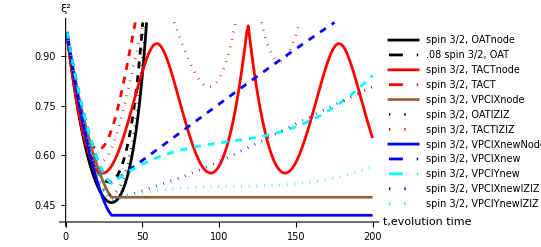

```mathematica
Plot5half2Newparameter=ListPlot[{OATnode,OAT,TACTnode,TACT,VPCIXnode,OATIZIZ,TACTIZIZ,VPCIXnewNode,VPCIXnew,VPCIYnew,VPCIXnewIZIZ,VPCIYnewIZIZ},Joined->{True,True,True,True,True,True},PlotRange->{{0,200},{0.4,1}},PlotLegends->{"spin 3/2, OATnode",.08"spin 3/2, OAT","spin 3/2, TACTnode","spin 3/2, TACT","spin 3/2, VPCIXnode","spin 3/2, OATIZIZ","spin 3/2, TACTIZIZ","spin 3/2, VPCIXnewNode","spin 3/2, VPCIXnew","spin 3/2, VPCIYnew","spin 3/2, VPCIXnewIZIZ","spin 3/2, VPCIYnewIZIZ"},AxesLabel->{"t,evolution time","ξ^2"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed},Brown,{Black,Dotted},{Red,Dotted},Blue,{Blue,Dashed},{Cyan,Dashed},{Blue,Dotted},{Cyan,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

```mathematica
Export["E:\\desksave2\\Astro\\spin squeezing\\picture save\\Plot5half2Newparameter.pdf",Plot5half2Newparameter]
```

E:\desksave2\Astro\spin squeezing\picture save\Plot5half2Newparameter.pdf

## sequence with decay, master equation backup 7/2

```mathematica
Clear["Global`*"];
dim=7/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
(*Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});*)
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;


IniPhi={{1},{0},{0},{0},{0},{0},{0},{0}};

StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi//FullSimplify
StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(χ*(3*Iz3half2.Iz3half2+η*(Iplus3half2.Iplus3half2+Iminus3half2.Iminus3half2)/2))*t].StateθϕInitial[θ,ϕ]

DensityMatrixEvo[t_,θ_,ϕ_]:=StateEvo[t,θ,ϕ].ConjugateTranspose[StateEvo[t,θ,ϕ]]


(*StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].StateθϕInitial[θ,ϕ]
StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t].StateθϕInitial[θ,ϕ]

StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(3Iz3half2.Iz3half2+η/2(Ix3half2.Ix3half2-Iy3half2.Iy3half2))*t].StateθϕInitial[θ,ϕ]
StateEvo2[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].css[θ,ϕ]*)
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
θ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
(*ϕ2[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*Print[N[xVal]];
Print[yVal//FullSimplify];*)
If[First[Flatten[N[xVal]]]==0&&First[Flatten[N[yVal]]]!=0,Pi/2,N[First[Flatten[ArcTan[yVal/xVal]]]]]
]*)
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]
]
ϕ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]]]
]
In1[state_]:=N[-Ix3half2*Sin[ϕ1DM[state]]+Iy3half2*Cos[ϕ1DM[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1DM[state]]Cos[ϕ1DM[state]]-Iy3half2*Cos[θ1DM[state]]Sin[ϕ1DM[state]]+Iz3half2*Sin[θ1DM[state]]]
(*In1[state_]:=N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]
In1n2plusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]*)
In1n2plusSqure[state_]:=Tr[(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=Tr[(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=Tr[(In1[state].In2[state]+In2[state].In1[state]).state]
ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )^1/((Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2)]]]
(*ξSqure[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )/Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]*)
(*ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]*)
ξbottomF[state_]:=N[First[Flatten[ Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]




d=8;
L0=Table[0 ,{i,d*d},{j,d*d}];
Do[L0[[i,j]]=Subscript[L, (i-1)*d*d+j],{i,1,d*d},{j,1,d*d}];
L0List=Flatten[L0];
H0=Table[0 ,{i,d},{j,d}];
ρ0=Table[0 ,{i,d},{j,d}];
Do[H0[[i,j]]=Subscript[H, (i-1)*d+j];ρ0[[i,j]]=Subscript[ρ, (i-1)*d+j],{i,1,d},{j,1,d}](*Print[L0//MatrixForm]; Print[H0//MatrixForm; Print[ρ0//MatrixForm]*)

(*RHLIST=-I*(H0.ρ0-ρ0.H0)+gamma*(PauliMatrix[3].ρ0.PauliMatrix[3]-ρ0);

RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
*)
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
(*RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γ, z](KroneckerProduct[Iz3half2,Identit yMatrix[2]].ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));*)
RHBlockList=Flatten[Transpose[RHLIST]];
ρBlockList=Flatten[Transpose[ρ0]]; (*Print[ρBlockList]; Print[RHBlockList//MatrixForm]*)
LHBlockList=L0.Transpose[ρBlockList];(*Print[LHBlockList//MatrixForm]; Print[LHBlockList-RHBlockList//MatrixForm//FullSimplify]*)
Solvelist=LHBlockList-RHBlockList; (*Print[Solvelist//FullSimplify//MatrixForm]; Print[Solvelist[[1]]//FullSimplify//MatrixForm]*)
L1=Table[0 ,{i,d*d},{j,d*d}];
Do[L1[[i,j]]=Coefficient[Solvelist[[i]],Subscript[ρ, j],1],{i,1,d*d},{j,1,d*d}];
Do[L1[[i]]=Sort[L1[[i]]],{i,1,d}] ;(*Print[L1//MatrixForm];*)
L1=Flatten[L1];(*Print[L1//MatrixForm];*)
Do[L1[[i]]=Solve[L1[[i]]==0,L0List],{i,1,d*d*d*d}];
L1resultList=Flatten[Sort[L1]];(*Print[L1resultList]*)
Do[L1resultList[[i]]=L1resultList[[i,2]],{i,1,d*d*d*d}];(*Print[L1resultList]*)
L1resultList=N[Partition[L1resultList,d*d]];

(*HMATRIX=({{0, (√7)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ11), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}});
HMATRIX=Iz3half2.Iz3half2;
HMATRIX=Ix3half2.Ix3half2-Iy3half2.Iy3half2;
*)
HMATRIX=({{0, (√7)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ11), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}});

Print[HMATRIX//MatrixForm];

Do[
Subscript[H, (i-1)*d+j]=HMATRIX[[i,j]];
,{i,1,d},{j,1,d}]
Ω=0;
β=1;
Subscript[γI, z]=0.01;
Subscript[γI, x]=0;
Subscript[γS, z]=0;
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

General::stop: 在本次计算中，Solve::svars 的进一步输出将被抑制.

(0 | 1/2 √7 ⅇ^(-ⅈ ϕ11) | 0 | 0 | 0 | 0 | 0 | 0
1/2 √7 ⅇ^(ⅈ ϕ11) | 0 | √3 ⅇ^(-ⅈ ϕ2) | 0 | 0 | 0 | 0 | 0
0 | √3 ⅇ^(ⅈ ϕ2) | 0 | 1/2 √15 ⅇ^(-ⅈ ϕ3) | 0 | 0 | 0 | 0
0 | 0 | 1/2 √15 ⅇ^(ⅈ ϕ3) | 0 | 2 ⅇ^(-ⅈ ϕ4) | 0 | 0 | 0
0 | 0 | 0 | 2 ⅇ^(ⅈ ϕ4) | 0 | 1/2 √15 ⅇ^(-ⅈ ϕ5) | 0 | 0
0 | 0 | 0 | 0 | 1/2 √15 ⅇ^(ⅈ ϕ5) | 0 | √3 ⅇ^(-ⅈ ϕ6) | 0
0 | 0 | 0 | 0 | 0 | √3 ⅇ^(ⅈ ϕ6) | 0 | 1/2 √7 ⅇ^(-ⅈ ϕ7)
0 | 0 | 0 | 0 | 0 | 0 | 1/2 √7 ⅇ^(ⅈ ϕ7) | 0)

```mathematica
ξtopF[DMevolve[[m,k]]];
```

```mathematica
Ix3half2//MatrixForm
```

(0 | (√7)/2 | 0 | 0 | 0 | 0 | 0 | 0
(√7)/2 | 0 | √3 | 0 | 0 | 0 | 0 | 0
0 | √3 | 0 | (√15)/2 | 0 | 0 | 0 | 0
0 | 0 | (√15)/2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | (√15)/2 | 0 | 0
0 | 0 | 0 | 0 | (√15)/2 | 0 | √3 | 0
0 | 0 | 0 | 0 | 0 | √3 | 0 | (√7)/2
0 | 0 | 0 | 0 | 0 | 0 | (√7)/2 | 0)

```mathematica
Iy3half2//MatrixForm
```

(0 | -(ⅈ √7)/2 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ √7)/2 | 0 | -ⅈ √3 | 0 | 0 | 0 | 0 | 0
0 | ⅈ √3 | 0 | -(ⅈ √15)/2 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ √15)/2 | 0 | -2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ | 0 | -(ⅈ √15)/2 | 0 | 0
0 | 0 | 0 | 0 | (ⅈ √15)/2 | 0 | -ⅈ √3 | 0
0 | 0 | 0 | 0 | 0 | ⅈ √3 | 0 | -(ⅈ √7)/2
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ √7)/2 | 0)

```mathematica
Iz3half2//MatrixForm
```

(7/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -7/2)

```mathematica
StateθϕInitial[Pi/2,Pi/2]
```

{{1/(8 √2)},{1/8 ⅈ √(7/2)},{-(√(21/2))/8},{-1/8 ⅈ √(35/2)},{(√(35/2))/8},{1/8 ⅈ √(21/2)},{-(√(7/2))/8},{-ⅈ/(8 √2)}}

```mathematica
(*UEvo=MatrixExp[-I*({{0, (√7)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ11), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}})*t1];*)
UEvo=MatrixExp[-I*Iz3half2.Iz3half2*t1];
(*IniState={{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}};*)
IniState=StateθϕInitial[Pi/2,Pi/2];

EvoState=UEvo.IniState;

dt=0.01;
number1=10 ;
number=10;
totNumber=20;

CtTable=Table[0,{i,0,totNumber}];
ϕ1Table={4.798215411225847,4.798215411225847,4.798215411225847,4.798215411225847,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={0.1944079490959938,0.1944079490959938,0.1944079490959938,0.1944079490959938,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={0.9854365550894499,0.9854365550894499,0.9854365550894499,0.9854365550894499,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={1.5016334514471628,1.5016334514471628,1.5016334514471628,1.5016334514471628,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={2.069304815853628,2.069304815853628,2.069304815853628,2.069304815853628,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ6Table={2.6948189616940574,2.6948189616940574,2.6948189616940574,2.6948189616940574,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ7Table={3.9672470265699005,3.9672470265699005,3.9672470265699005,3.9672470265699005,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
(*
ϕ1Table={4.798215411225847,4.798215411225847,4.798215411225847,4.798215411225847,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.1944079490959938,0.1944079490959938,0.1944079490959938,0.1944079490959938,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={0.9854365550894499,0.9854365550894499,0.9854365550894499,0.9854365550894499,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={1.5016334514471628,1.5016334514471628,1.5016334514471628,1.5016334514471628,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={2.069304815853628,2.069304815853628,2.069304815853628,2.069304815853628,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ6Table={2.6948189616940574,2.6948189616940574,2.6948189616940574,2.6948189616940574,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ7Table={3.9672470265699005,3.9672470265699005,3.9672470265699005,3.9672470265699005,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={4.798215411225847,4.798215411225847,4.798215411225847,4.798215411225847,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={0.1944079490959938,0.1944079490959938,0.1944079490959938,0.1944079490959938,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={0.9854365550894499,0.9854365550894499,0.9854365550894499,0.9854365550894499,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={1.5016334514471628,1.5016334514471628,1.5016334514471628,1.5016334514471628,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={2.069304815853628,2.069304815853628,2.069304815853628,2.069304815853628,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ6Table={2.6948189616940574,2.6948189616940574,2.6948189616940574,2.6948189616940574,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ7Table={3.9672470265699005,3.9672470265699005,3.9672470265699005,3.9672470265699005,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};

ϕ1Table={2.443830774388557,2.443830774388557,2.443830774388557,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={2.316783229103837,2.316783229103837,2.316783229103837,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-0.8080200072794748,-0.8080200072794748,-0.8080200072794748,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={-1.570795375807605,-1.570795375807605,-1.570795375807605,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={-2.333571364652085,-2.333571364652085,-2.333571364652085,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ6Table={0.8248085823864257,0.8248085823864257,0.8248085823864257,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ7Table={0.6977612325725193,0.6977612325725193,0.6977612325725193,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

ϕ1Table={2.443830774388557,2.443830774388557,2.443830774388557,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={2.316783229103837,2.316783229103837,2.316783229103837,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={-0.8080200072794748,-0.8080200072794748,-0.8080200072794748,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={-1.570795375807605,-1.570795375807605,-1.570795375807605,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={-2.333571364652085,-2.333571364652085,-2.333571364652085,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ6Table={0.8248085823864257,0.8248085823864257,0.8248085823864257,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ7Table={0.6977612325725193,0.6977612325725193,0.6977612325725193,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};


{2.443830774388557,2.316783229103837,-0.8080200072794748,-1.570795375807605,-2.333571364652085,0.8248085823864257,0.6977612325725193}*)
(*

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table=Table[2.581055163108225,{i,0,totNumber}];
ϕ2Table=Table[3.9125553774195057,{i,0,totNumber}];
ϕ3Table=Table[0.8791183546201431,{i,0,totNumber}];

2.581055163108225,3.9125553774195057,0.8791183546201431*)
(*IniStateBox={{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}};*)
IniStateBox={StateθϕInitial[Pi/2,Pi/2]};

fvaluebox={1};
SqueezeListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{i,number*totNumber}];
TargetStateBox={{{1},{0},{0},{0},{0},{0},{0},{0}},{{0},{1},{0},{0},{0},{0},{0},{0}},{{0},{0},{1},{0},{0},{0},{0},{0}},{{0},{0},{0},{1},{0},{0},{0},{0}},{{0},{0},{0},{0},{1},{0},{0},{0}},{{0},{0},{0},{0},{0},{1},{0},{0}}};
DM=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMList=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
Do[
Do[
If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];

DMList[[m,k]]=Flatten[Transpose[DM[[m,k]]]];
,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]

TargetStateDMBox=Table[0,{i,Length[TargetStateBox]}];
Do[
TargetStateDMBox[[i]]=TargetStateBox[[i]].ConjugateTranspose[TargetStateBox[[i]]];
,{i,1,Length[TargetStateDMBox]}]


FListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{j,1,Length[TargetStateBox]},{i,number}];

DMevolvemid=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMevolve=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
(*Print[FListBox];*)
Do[
Do[
ϕ11=ϕ1Table[[l]];
ϕ2=ϕ2Table[[l]];
ϕ3=ϕ3Table[[l]];
ϕ4=ϕ4Table[[l]];
ϕ5=ϕ5Table[[l]];
ϕ6=ϕ6Table[[l]];
ϕ7=ϕ7Table[[l]];
DMevolvemid[[m,k]]=N[MatrixExp[(L1resultList/. t->(i)*dt)*dt].DMList[[m,k]]];

DMevolve[[m,k]]=Transpose[Partition[DMevolvemid[[m,k]],d]];

SqueezeListBox[[m,k,i+(l-1)*number1]]=ξtopF[DMevolve[[m,k]]];

FListBox[[m,k,1,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[1]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[1]]]])^1;
FListBox[[m,k,2,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[2]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[2]]]])^1;
FListBox[[m,k,3,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[3]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[3]]]])^1;
FListBox[[m,k,4,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[4]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[4]]]])^1;
FListBox[[m,k,5,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[5]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[5]]]])^1;
FListBox[[m,k,6,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[6]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[6]]]])^1;
If[i==number1,StateFinal=DMevolve[[m,k]]];


DMList[[m,k]]=DMevolvemid[[m,k]];
(*If[Divisible[i,number1/printnumber],Print[i,"/",number1,"   m: ",m,"   k: ",k]];*)
,{i,1,number1}];

,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]
Print[l];
,{l,1,totNumber}]
```

Flatten::normal: Flatten[3.49836+3.90313×10^-18 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.57056+3.74089×10^-19 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.57006+8.52901×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

```mathematica
StateθϕInitial[Pi/2,Pi/2]
```

{{1/(8 √2)},{1/8 ⅈ √(7/2)},{-(√(21/2))/8},{-1/8 ⅈ √(35/2)},{(√(35/2))/8},{1/8 ⅈ √(21/2)},{-(√(7/2))/8},{-ⅈ/(8 √2)}}

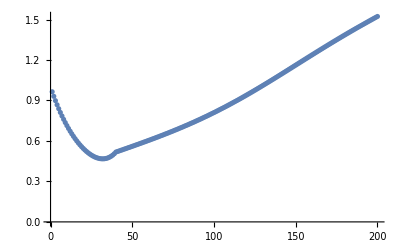

```mathematica
ListPlot[Chop[(3.5*SqueezeListBox[[1,1]])/1,10^-7]]
```

```mathematica
VPCIYnode={0.9563410988555731,0.9157759333902059,0.8779908768105775,0.8427118856058383,0.8096997882667508,0.7787464322999311,0.7496715960691895,0.7223205926260939,0.6965625124394321,0.6722890710262853,0.6494140462704323,0.627873309124527,0.607625470946871,0.588653191507865,0.5709652143698718,0.554599221621167,0.5396256286248613,0.5261524723911455,0.5143315853189444,0.5043662903376448,0.49652090485054545,0.49113240017198795,0.48862463093686115,0.4895256253285739,0.4944885111459617,0.5043167425327272,0.5199943832412084,0.5427222868599331,0.5739610798094047,0.6154818792660157,0.6154818792660152,0.6154818792660176,0.6154818792660168,0.6154818792660139,0.6154818792660132,0.6154818792660153,0.6154818792660165,0.6154818792660157,0.6154818792660173,0.6154818792660166,0.6154818792660156,0.6154818792660156,0.6154818792660137,0.6154818792660142,0.6154818792660142,0.6154818792660115,0.6154818792660125,0.6154818792660126,0.6154818792660116,0.6154818792660118,0.6154818792660092,0.6154818792660125,0.6154818792660092,0.6154818792660092,0.6154818792660074,0.6154818792660033,0.615481879266005,0.6154818792660014,0.6154818792660017,0.6154818792659973,0.6154818792659977,0.6154818792659947,0.615481879265998,0.6154818792659961,0.6154818792659994,0.6154818792659986,0.6154818792659984,0.6154818792659963,0.6154818792659963,0.6154818792659961,0.6154818792659961,0.6154818792659945,0.615481879265992,0.615481879265992,0.6154818792659912,0.6154818792659928,0.6154818792659926,0.6154818792659913,0.6154818792659896,0.6154818792659896,0.6154818792659923,0.615481879265993,0.6154818792659922,0.6154818792659931,0.6154818792659912,0.615481879265991,0.615481879265991,0.615481879265992,0.615481879265991,0.6154818792659894,0.6154818792659845,0.6154818792659859,0.6154818792659845,0.615481879265987,0.6154818792659845,0.6154818792659837,0.6154818792659837,0.6154818792659827,0.615481879265981,0.6154818792659773,0.6154818792659787,0.6154818792659814,0.615481879265978,0.615481879265978,0.615481879265978,0.6154818792659777,0.6154818792659787,0.6154818792659761,0.6154818792659769,0.6154818792659764,0.6154818792659764,0.6154818792659764,0.615481879265975,0.6154818792659774,0.6154818792659764,0.6154818792659784,0.6154818792659741,0.6154818792659751,0.6154818792659733,0.6154818792659759,0.6154818792659726,0.615481879265975,0.6154818792659724,0.615481879265972,0.6154818792659718,0.6154818792659722,0.6154818792659711,0.6154818792659722,0.6154818792659738,0.6154818792659714,0.6154818792659706,0.6154818792659674,0.6154818792659674,0.615481879265966,0.6154818792659653,0.6154818792659653,0.6154818792659651,0.6154818792659653,0.6154818792659621,0.6154818792659623,0.6154818792659627,0.6154818792659633,0.6154818792659653,0.6154818792659634,0.6154818792659661,0.6154818792659654,0.6154818792659645,0.6154818792659654,0.6154818792659639,0.6154818792659632,0.6154818792659632,0.6154818792659625,0.6154818792659642,0.6154818792659625,0.6154818792659619,0.615481879265962,0.6154818792659601,0.615481879265962,0.6154818792659622,0.615481879265963,0.6154818792659623,0.6154818792659615,0.6154818792659599,0.6154818792659609,0.6154818792659599,0.61548187926596,0.6154818792659585,0.6154818792659585,0.6154818792659604,0.6154818792659607,0.6154818792659589,0.6154818792659589,0.6154818792659578,0.6154818792659545,0.6154818792659554,0.6154818792659574,0.6154818792659542,0.6154818792659542,0.6154818792659551,0.6154818792659551,0.6154818792659575,0.6154818792659574,0.6154818792659582,0.6154818792659582,0.6154818792659601,0.6154818792659567,0.6154818792659545,0.6154818792659544,0.6154818792659529,0.6154818792659529,0.6154818792659523,0.6154818792659515,0.6154818792659492,0.6154818792659459,0.6154818792659466,0.6154818792659473,0.6154818792659466,0.6154818792659482,0.6154818792659483,0.6154818792659476};
```

```mathematica
VPCIXnewNode2={0.9614017868574336,0.9245757183322969,0.8894305174145685,0.8558799984311647,0.8238430032138503,0.7932433371394523,0.7640097062492257,0.7360756567795135,0.7093795185352776,0.6838643536130505,0.6594779120324997,0.6361725958689144,0.613905433495489,0.5926380655474867,0.5723367442133499,0.5529723474433781,0.53452040964732,0.5169611704301657,0.5002796428921698,0.484465702995687,0.46951420147829814,0.45542509976870005,0.44220363133836565,0.42986048989669734,0.4184120458085014,0.4078805920777565,0.3982946211978587,0.3896891341124254,0.3821059824582284,0.3755942451685178,0.37021064039567925,0.36601997356132693,0.36309562215347374,0.36152005765755796,0.36138540472394537,0.36279403733129006,0.3658592112950938,0.37070573198567464,0.3774706555512785,0.38630402128205893,0.38630402128205854,0.3863040212820581,0.38630402128205893,0.38630402128205676,0.38630402128205676,0.3863040212820566,0.3863040212820556,0.38630402128205527,0.3863040212820544,0.3863040212820531,0.3863040212820541,0.3863040212820535,0.3863040212820528,0.3863040212820523,0.38630402128205077,0.3863040212820521,0.3863040212820499,0.386304021282051,0.3863040212820503,0.38630402128204905,0.38630402128204916,0.38630402128204877,0.3863040212820483,0.3863040212820479,0.3863040212820469,0.38630402128204727,0.3863040212820458,0.38630402128204566,0.3863040212820455,0.386304021282044,0.38630402128204344,0.3863040212820436,0.3863040212820414,0.3863040212820417,0.3863040212820418,0.3863040212820422,0.38630402128204183,0.38630402128204167,0.3863040212820425,0.38630402128204105,0.3863040212820425,0.38630402128204383,0.3863040212820433,0.38630402128204383,0.3863040212820435,0.38630402128204266,0.38630402128204255,0.3863040212820418,0.38630402128204167,0.38630402128204033,0.3863040212820409,0.38630402128203944,0.38630402128204094,0.38630402128203917,0.3863040212820391,0.38630402128203756,0.38630402128203756,0.3863040212820374,0.3863040212820379,0.386304021282037,0.3863040212820381,0.3863040212820387,0.3863040212820389,0.3863040212820378,0.3863040212820367,0.38630402128203695,0.3863040212820352,0.38630402128203617,0.38630402128203595,0.38630402128203517,0.38630402128203434,0.38630402128203556,0.3863040212820369,0.3863040212820346,0.38630402128203634,0.38630402128203395,0.38630402128203595,0.386304021282036,0.38630402128203595,0.3863040212820356,0.3863040212820368,0.3863040212820378,0.38630402128203767,0.3863040212820368,0.3863040212820348,0.3863040212820349,0.3863040212820346,0.38630402128203245,0.3863040212820332,0.3863040212820332,0.3863040212820333,0.3863040212820329,0.38630402128203384,0.3863040212820346,0.3863040212820329,0.386304021282032,0.38630402128203284,0.3863040212820337,0.3863040212820337,0.38630402128203417,0.38630402128203406,0.38630402128203245,0.3863040212820327,0.3863040212820327,0.38630402128203295,0.3863040212820319,0.3863040212820321,0.3863040212820324,0.38630402128203145,0.38630402128203123,0.3863040212820309,0.3863040212820317,0.3863040212820332,0.3863040212820332,0.3863040212820332,0.3863040212820326,0.386304021282034,0.38630402128203273,0.38630402128203184,0.3863040212820328,0.3863040212820302,0.38630402128202995,0.3863040212820307,0.3863040212820316,0.38630402128203056,0.3863040212820313,0.3863040212820289,0.3863040212820294,0.3863040212820291,0.38630402128202923,0.3863040212820288,0.386304021282028,0.38630402128202823,0.386304021282027,0.38630402128202523,0.3863040212820251,0.386304021282025,0.38630402128202374,0.386304021282025,0.3863040212820238,0.3863040212820235,0.38630402128202296,0.38630402128202324,0.38630402128202107,0.38630402128202307,0.3863040212820208,0.3863040212820196,0.3863040212820201,0.38630402128201996,0.38630402128201874,0.3863040212820174,0.38630402128201746,0.38630402128201613,0.3863040212820166,0.38630402128201624,0.38630402128201574,0.38630402128201646,0.38630402128201513,0.3863040212820154,0.38630402128201585};
VPCIXnewNode={0.9624517274050266,0.926584862770228,0.8923171936969018,0.8595709526231746,0.8282727738208326,0.7983536501893663,0.7697488907694225,0.7423980799979434,0.7162450398084133,0.6912377957423826,0.6673285482839947,0.6444736506589862,0.6226335943555379,0.601773003628267,0.5818606402406205,0.5628694196868222,0.5447764401140006,0.5275630251396984,0.5112147817306296,0.4957216742761385,0.4810781159546741,0.4672830784535986,0.45434022106151295,0.4422580401069615,0.4310500396668227,0.4207349244101495,0.4113368153767262,0.4028854894119021,0.39541664288750467,0.3889721802299164,0.38360052764741637,0.3793569722959171,0.3763040269415208,0.3745118199657886,0.3740585103108526,0.37503072667235615,0.37752402991401335,0.3816433972941198,0.3875037266572693,0.3952303582499543,0.3952303582499544,0.39523035824995545,0.395230358249955,0.39523035824995534,0.395230358249955,0.3952303582499543,0.3952303582499547,0.3952303582499543,0.3952303582499539,0.39523035824995295,0.3952303582499523,0.3952303582499532,0.3952303582499523,0.3952303582499519,0.3952303582499519,0.3952303582499528,0.3952303582499523,0.3952303582499511,0.3952303582499517,0.3952303582499495,0.3952303582499496,0.39523035824994956,0.395230358249948,0.39523035824994723,0.3952303582499473,0.39523035824994823,0.3952303582499477,0.39523035824994823,0.3952303582499466,0.3952303582499465,0.39523035824994585,0.3952303582499462,0.39523035824994435,0.3952303582499441,0.39523035824994585,0.39523035824994596,0.39523035824994435,0.39523035824994496,0.3952303582499449,0.3952303582499445,0.39523035824994324,0.3952303582499424,0.3952303582499422,0.3952303582499426,0.3952303582499415,0.3952303582499412,0.39523035824994046,0.3952303582499402,0.3952303582499398,0.3952303582499384,0.39523035824993885,0.39523035824994013,0.39523035824993785,0.39523035824993796,0.39523035824993785,0.3952303582499376,0.39523035824993635,0.39523035824993635,0.3952303582499348,0.39523035824993363,0.3952303582499342,0.39523035824993236,0.39523035824993225,0.3952303582499327,0.3952303582499326,0.39523035824993397,0.3952303582499326,0.39523035824993225,0.3952303582499332,0.39523035824993247,0.39523035824993186,0.39523035824993186,0.39523035824993186,0.3952303582499325,0.3952303582499305,0.39523035824993086,0.395230358249932,0.3952303582499314,0.3952303582499307,0.3952303582499309,0.3952303582499305,0.39523035824992825,0.39523035824992825,0.39523035824992947,0.39523035824993014,0.39523035824993064,0.3952303582499301,0.39523035824992936,0.3952303582499289,0.3952303582499306,0.3952303582499303,0.3952303582499289,0.3952303582499296,0.3952303582499286,0.3952303582499267,0.395230358249927,0.3952303582499275,0.39523035824992675,0.3952303582499272,0.39523035824992625,0.3952303582499266,0.3952303582499278,0.39523035824992747,0.395230358249928,0.39523035824992747,0.39523035824992736,0.39523035824992736,0.3952303582499283,0.3952303582499266,0.3952303582499284,0.39523035824992764,0.395230358249927,0.3952303582499266,0.39523035824992775,0.3952303582499276,0.39523035824992797,0.3952303582499283,0.3952303582499274,0.39523035824992797,0.39523035824992925,0.39523035824992875,0.3952303582499276,0.3952303582499273,0.39523035824992764,0.3952303582499273,0.3952303582499267,0.3952303582499258,0.39523035824992747,0.3952303582499262,0.39523035824992553,0.3952303582499258,0.39523035824992664,0.39523035824992525,0.3952303582499241,0.3952303582499244,0.3952303582499257,0.3952303582499241,0.3952303582499227,0.3952303582499231,0.39523035824992236,0.39523035824992137,0.3952303582499216,0.3952303582499218,0.3952303582499201,0.3952303582499203,0.3952303582499203,0.39523035824991987,0.3952303582499179,0.39523035824991826,0.3952303582499169,0.39523035824991665,0.3952303582499169,0.39523035824991676,0.39523035824991487,0.3952303582499138,0.3952303582499131,0.39523035824991376,0.3952303582499126,0.39523035824991176,0.3952303582499108};
VPCIXnew={0.9682504522787911,0.9379878920694815,0.9091391654065073,0.881635543919887,0.8554126597571998,0.8304104395501654,0.8065730388940101,0.7838487788150464,0.7621900856885094,0.7415534360381535,0.7218993076050793,0.7031921380191519,0.6854002923454436,0.6684960407132065,0.652455547168299,0.637258870823811,0.6228899803190462,0.6093367825352208,0.5965911664573839,0.5846490630164866,0.5735105216925275,0.5631798046088053,0.5536654987972373,0.5449806472642131,0.5371428994338757,0.5301746814892156,0.5241033870689032,0.5189615887070642,0.5147872703219424,0.5116240809649639,0.5095216099314817,0.5085356832057318,0.5087286810623566,0.5101698764724536,0.5129357937605228,0.5171105867271443,0.5227864351878876,0.5300639585793513,0.5390526449458817,0.549871293243583,0.5551546062359423,0.5604353624961887,0.5657135758658284,0.5709892610276516,0.5762624335035136,0.581533109648377,0.5868013066405654,0.5920670424682513,0.5973303359121425,0.6025912065244269,0.6078496746039423,0.6131057611676316,0.6183594879183151,0.6236108772088069,0.6288599520024498,0.6341067358301181,0.6393512527437503,0.6445935272665215,0.6498335843397048,0.6550714492663425,0.6603071476518264,0.6655407053414976,0.6707721483553892,0.6760015028202291,0.6812287948988716,0.6864540507172763,0.6916772962891714,0.6968985574386204,0.7021178597205943,0.7073352283397627,0.712550688067671,0.717764263158496,0.722975977263561,0.728185853344825,0.7333939135875338,0.7386001793122565,0.743804670886497,0.7490074076361333,0.7542084077568604,0.7594076882258962,0.7646052647141574,0.7698011514991318,0.7749953613786964,0.7801879055860794,0.7853787937062288,0.7905680335937931,0.7957556312929651,0.8009415909594048,0.8061259147844684,0.8113086029219804,0.8164896534177633,0.8216690621421421,0.8268468227256449,0.8320229264981154,0.8371973624314297,0.8423701170860233,0.8475411745614445,0.8527105164510819,0.8578781218012851,0.8630439670750321,0.8682080261203187,0.8733702701434168,0.8785306676871669,0.883689184614417,0.8888457840967707,0.8940004266087488,0.8991530699274431,0.9043036691378245,0.9094521766437255,0.9145985421846243,0.9197427128582496,0.9248846331491001,0.9300242449628676,0.9351614876668538,0.940296298136323,0.9454286108068504,0.9505583577326228,0.9556854686506812,0.960809871051047,0.9659314902527149,0.9710502494854233,0.9761660699771242,0.9812788710471027,0.9863885702045693,0.9914950832527107,0.9965983243979868,1.0016982063645772,1.0067946405138328,1.0118875369685614,1.016976804741962,1.0220623518710532,1.0271440855543923,1.032221912293884,1.0372957380404495,1.0423654683433727,1.0474310085030605,1.0524922637270022,1.0575491392886696,1.0626015406891152,1.0676493738210113,1.0726925451348523,1.0777309618070827,1.0827645319098427,1.0877931645820602,1.0928167702016363,1.0978352605584156,1.1028485490276472,1.1078565507436609,1.1128591827734902,1.1178563642901098,1.1228480167450214,1.127834064039906,1.1328144326970342,1.1377890520281646,1.1427578543016432,1.1477207749074205,1.1526777525197036,1.1576287292569853,1.1625736508391715,1.1675124667415429,1.1724451303452974,1.1773715990844165,1.1822918345886175,1.1872058028221513,1.192113474218203,1.1970148238086888,1.2019098313492274,1.2067984814390762,1.2116807636358242,1.2165566725646926,1.2214262080222054,1.2262893750740975,1.231146184147305,1.2359966511158627,1.2408407973805629,1.2456786499422983,1.2505102414688951,1.2553356103553914,1.2601548007776158,1.26496786273901,1.2697748521105985,1.274575830664055,1.2793708660977836,1.284160032056001,1.2889434081407731,1.2937210799169583,1.298493138910094,1.3032596825971672,1.3080208143903174,1.3127766436134742,1.317527285471952,1.3222728610150452,1.3270134970916596,1.3317493262990865,1.33648048692484,1.34120712288187,1.3459293836369897,1.350647424132761,1.3553614047028768,1.3600714909811724};
VPCIYnew={0.9682504522787911,0.9379878920694815,0.9091391654065073,0.881635543919887,0.8554126597571998,0.8304104395501654,0.8065730388940101,0.7838487788150464,0.7621900856885094,0.7415534360381535,0.7218993076050793,0.7031921380191519,0.6854002923454436,0.6684960407132065,0.652455547168299,0.637258870823811,0.6228899803190462,0.6093367825352208,0.5965911664573839,0.5846490630164866,0.5735105216925275,0.5631798046088053,0.5536654987972373,0.5449806472642131,0.5371428994338757,0.5301746814892156,0.5241033870689032,0.5189615887070642,0.5147872703219424,0.5116240809649639,0.5095216099314817,0.5085356832057318,0.5087286810623566,0.5101698764724536,0.5129357937605228,0.5171105867271443,0.5227864351878876,0.5300639585793513,0.5390526449458817,0.549871293243583,0.5551153723827122,0.5602782755620357,0.565359815055314,0.5703598383082924,0.5752782279826234,0.5801149019835838,0.5848698134716207,0.5895429508577608,0.5941343377829573,0.5986440330814308,0.6030721307280754,0.607418759770054,0.6116840842426392,0.6158683030694464,0.6199716499471458,0.6239943932148257,0.6279368357080971,0.6317993145981289,0.6355822012157422,0.6392859008607502,0.6429108525966789,0.6464575290311165,0.6499264360817889,0.6533181127286314,0.6566331307520279,0.6598720944574059,0.6630356403864346,0.666124437015015,0.6691391844382993,0.6720806140429669,0.6749494881669749,0.6777465997470362,0.680472771954051,0.6831288578167368,0.6857157398337071,0.6882343295742355,0.6906855672679696,0.6930704213838317,0.6953898881983647,0.6976449913537879,0.6998367814059989,0.7019663353627921,0.7040347562125575,0.7060431724436866,0.7079927375549852,0.7098846295573119,0.7117200504667347,0.7135002257894185,0.7152264039985594,0.7168998560035496,0.7185218746117038,0.7200937739827233,0.7216168890762218,0.7230925750925008,0.7245222069068822,0.7259071784977857,0.7272489023688582,0.7285488089653542,0.7298083460850208,0.7310289782837565,0.7322121862762416,0.7333594663318099,0.7344723296657805,0.7355523018264933,0.7366009220782764,0.7376197427805862,0.7386103287635315,0.73957425670002,0.7405131144747724,0.7414285005503786,0.7423220233306803,0.7431953005216514,0.744049958490033,0.7448876316199096,0.7457099616674707,0.7465185971141695,0.7473151925184671,0.7481014078664228,0.7488789079212982,0.7496493615724175,0.7504144411834817,0.7511758219405432,0.7519351811998728,0.7526941978358906,0.753454551589402,0.7542179224163326,0.7549859898371648,0.755760432287285,0.7565429264684616,0.7573351467016209,0.7581387642811813,0.7589554468310925,0.7597868576628235,0.7606346551354837,0.7615004920183039,0.7623860148556266,0.7632928633346782,0.7642226696562774,0.7651770579086978,0.7661576434448827,0.7671660322632214,0.7682038203920754,0.7692725932782669,0.7703739251797352,0.7715093785625305,0.7726805035023936,0.7738888370910798,0.7751359028476367,0.7764232101348649,0.7777522535810937,0.77912451250756,0.7805414503614931,0.7820045141551744,0.783515133911132,0.7850747221136729,0.786684673166955,0.7883463628597679,0.7900611478372505,0.791830365079713,0.7936553313887482,0.7955373428808458,0.7974776744886741,0.7994775794702249,0.8015382889260093,0.8036610113244764,0.805846932035853,0.8080972128745717,0.8104129916504598,0.8127953817288881,0.8152454716000321,0.8177643244574204,0.8203529777859521,0.8230124429595392,0.8257437048485402,0.8285477214371569,0.8314254234509344,0.8343777139945455,0.8374054681999943,0.8405095328854005,0.843690726224512,0.8469498374270821,0.8502876264302626,0.8537048236011586,0.8572021294506503,0.8607802143586506,0.8644397183108992,0.8681812506474289,0.8720053898228269,0.8759126831784011,0.8799036467263609,0.8839787649461286,0.8881384905928961,0.8923832445184905,0.8967134155046911,0.9011293601090414,0.905631402523289,0.910219834444497,0.914894914958937,0.9196568704387889,0.9245058944517839};
VPCIYnewIZIZ={0.9655130622717605,0.9326948803100735,0.9014631192949962,0.8717404190976631,0.8434542995489083,0.8165370668524587,0.7909257222643988,0.7665618741985949,0.7433916549349996,0.7213656431065048,0.7004387931227275,0.6805703726586606,0.6617239092949592,0.6438671473474596,0.626972015868454,0.6110146087432746,0.5959751777443338,0.5818381393420787,0.5685920960090104,0.5562298726892272,0.5447485690418333,0.5341496280013898,0.5244389211316498,0.5156268511787977,0.5077284721560927,0.5007636272112147,0.4947571044391561,0.48973881070480013,0.48574396342838055,0.48281330016129603,0.48099330563690834,0.4803364558183939,0.4809014782809927,0.48275362805656385,0.48596497783186804,0.4906147211261228,0.4967894867762758,0.5045836627282181,0.514099726767757,0.5254485814257881,0.5296155739711143,0.5336874821407803,0.537665135232209,0.5415493895005866,0.5453411272929586,0.5490412561961292,0.5526507081965005,0.5561704388500316,0.5596014264605234,0.5629446712645683,0.5662011946215235,0.5693720382069958,0.5724582632084522,0.5754609495216458,0.5783811949467438,0.5812201143831357,0.5839788390220462,0.5866585155363044,0.5892603052666864,0.5917853834044777,0.5942349381700629,0.5966101699874917,0.5989122906551689,0.6011425225129678,0.6033020976062418,0.6053922568473574,0.607414249175547,0.6093693307160106,0.6112587639393494,0.6130838168225541,0.6148457620128851,0.6165458759960931,0.6181854382705614,0.619765730529015,0.6212880358495226,0.6227536378976299,0.624163820141445,0.625519865081612,0.6268230534981029,0.6280746637157565,0.6292759708905431,0.6304282463184792,0.6315327567691212,0.6325907638455006,0.6336035233723601,0.6345722848144183,0.6354982907264047,0.6363827762364374,0.637226968564276,0.6380320865758718,0.6387993403754924,0.6395299309366206,0.6402250497726631,0.6408858786483961,0.6415135893329236,0.6421093433947856,0.6426742920396886,0.6432095759912174,0.6437163254147039,0.6441956598842975,0.6446486883931035,0.6450765094061484,0.6454802109557431,0.645860870778695,0.6462195564946653,0.6465573258248265,0.6468752268498841,0.6471742983063159,0.6474555699196634,0.6477200627735087,0.6479687897127173,0.6482027557794172,0.6484229586800498,0.6486303892818223,0.6488260321367418,0.6490108660313806,0.6491858645604561,0.6493519967222454,0.649510227533822,0.649661518664074,0.6498068290823803,0.6499471157209036,0.6500833341483214,0.6502164392528965,0.6503473859327742,0.6504771297913374,0.6506066278355516,0.6507368391751766,0.6508687257207791,0.6510032528784829,0.6511413902394365,0.6512841122620181,0.6514323989447948,0.6515872364883406,0.6517496179440131,0.6519205438478636,0.6521010228378648,0.6522920722527296,0.6524947187105796,0.6527099986658043,0.652938958942512,0.653182657242951,0.6534421626294046,0.6537185559780299,0.6540129304032087,0.654326391650994,0.6546600584602638,0.6550150628902638,0.6553925506132214,0.6557936811707775,0.6562196281929991,0.6566715795787902,0.6571507376365122,0.6576583191837023,0.6581955556047896,0.6587636928657382,0.6593639914845709,0.6599977264567942,0.6606661871347289,0.6613706770598344,0.6621125137471122,0.6628930284207216,0.6637135657000048,0.6645754832351191,0.665480151291546,0.6664289522828021,0.6674232802506881,0.668464540292519,0.669554147934801,0.6706935284528979,0.6718841161362977,0.6731273534991739,0.6744246904359895,0.6757775833220073,0.6771874940586419,0.6786558890636993,0.680184238206614,0.6817740136889852,0.6834266888707259,0.6851437370423403,0.6869266301439348,0.688776837431712,0.6906958240928179,0.6926850498096069,0.6947459672744689,0.6968800206565744,0.6990886440220354,0.7013732597091328,0.7037352766604429,0.7061760887138702,0.7086970728547439,0.711299587431355,0.7139849703364274,0.7167545371572632,0.7196095792974289,0.7225513620730417,0.7255811227869242,0.7287000687839941,0.7319093754915174,0.7352101844479624};
```

```mathematica
VPCIXnewIZIZ={0.9644385295305504,0.9306364209504026,0.89850226581962,0.8679503467036084,0.8389005129123879,0.8112780580438287,0.7850136007679571,0.760042970333807,0.7363070982971006,0.7137519179599295,0.6923282729866677,0.67199183661778,0.6527030428489304,0.6344270308805955,0.617133604076429,0.6007972045995813,0.5853969048271176,0.5709164165750088,0.5573441191006818,0.5446731067870627,0.5329012573510042,0.522031321359121,0.512071033773998,0.5030332481916828,0.49493609436515373,0.4878031595355501,0.48166369401045883,0.4765528413333274,0.472511893276717,0.46958856976089036,0.46783732364428116,0.4673196701496543,0.4681045404749258,0.4702686588864764,0.47389694230080376,0.4790829210233881,0.48592917892730486,0.4945478109146875,0.5050608950078799,0.5176009758612965,0.5218273090103005,0.526057127577613,0.5302914142845737,0.5345311575094964,0.5387773508404761,0.5430309926068738,0.5472930853897919,0.5515646355117624,0.555846652505932,0.5601401485650622,0.5644461379705838,0.5687656365020308,0.5730996608271528,0.5774492278730088,0.581815354178338,0.5861990552275561,0.590601344766659,0.5950232341013688,0.599465731377866,0.6039298408464089,0.6084165621081968,0.6129268893458235,0.6174618105376535,0.6220223066564949,0.6266093508529482,0.631223907623797,0.635866931965854,0.6405393685156766,0.6452421506755938,0.6499761997265024,0.6547424239279153,0.6595417176058065,0.6643749602287814,0.6692430154731698,0.6741467302776895,0.6790869338883387,0.6840644368942839,0.6890800302554779,0.6941344843229051,0.6992285478523387,0.7043629470125935,0.7095383843893254,0.7147555379855035,0.7200150602197939,0.7253175769241035,0.73066368634172,0.7360539581274956,0.7414889323516636,0.7469691185089598,0.7524949945348254,0.7580670058305685,0.7636855642994597,0.7693510473958649,0.7750637971895911,0.7808241194477402,0.7866322827364751,0.7924885175451879,0.7983930154356631,0.8043459282189157,0.8103473671624828,0.8163974022310284,0.8224960613631456,0.828643329787413,0.834839149380714,0.8410834180719212,0.8473759892940957,0.8537166714883626,0.8601052276626179,0.86654137500827,0.8730247845781645,0.8795550810288116,0.8861318424300137,0.8927546001449352,0.8994228387835104,0.9061359962321114,0.9128934637621264,0.9196945862201311,0.9265386623020648,0.9334249449137074,0.940352641619534,0.9473209151818975,0.9543288841921423,0.9613756237951262,0.9684601665083055,0.9755815031362799,0.9827385837814411,0.9899303189509764,0.9971555807602939,1.0044132042324834,1.011701988693159,1.019020699259677,1.0263680684233565,1.0337427977229572,1.0411435595073402,1.0485689987848448,1.0560177351565578,1.0634883648302849,1.070979462711689,1.078489584568692,1.086017269264865,1.0935610410572951,1.1011194119539367,1.1086908841253065,1.1162739523649896,1.1238671065931711,1.1314688343971597,1.1390776236026607,1.146691964869276,1.1543103543036146,1.1619312960831372,1.1695533050838345,1.1771749095046198,1.1847946534813436,1.1924110996832062,1.2000228318843855,1.207628457503702,1.2152266101051155,1.2228159518520623,1.2303951759085765,1.2379630087804405,1.245518212589595,1.2530595872754053,1.2605859727164592,1.2680962507668843,1.2755893472014048,1.2830642335636966,1.2905199289128397,1.2979555014630502,1.3053700701122157,1.312762805855095,1.3201329330774714,1.3274797307278698,1.3348025333639315,1.3421007320708942,1.3493737752500339,1.3566211692754122,1.3638424790176158,1.3710373282336512,1.3782053998225479,1.3853464359466627,1.3924602380190634,1.3995466665578096,1.4066056409083,1.4136371388352673,1.4206411959863856,1.4276179052297635,1.4345674158679984,1.441489932731761,1.448385715156194,1.4552550758437004,1.4620983796170213,1.468916042066642,1.4757085280969253,1.4824763503755476,1.4892200676909673,1.495940283222862,1.502637642730653,1.5093128326653265,1.5159665782098903,1.5225996412539153};
```

```mathematica
VPCIXnode={0.9563410988555731,0.9157759333902059,0.8779908768105775,0.8427118856058383,0.8096997882667508,0.7787464322999311,0.7496715960691895,0.7223205926260939,0.6965625124394321,0.6722890710262853,0.6494140462704323,0.627873309124527,0.607625470946871,0.588653191507865,0.5709652143698718,0.554599221621167,0.5396256286248613,0.5261524723911455,0.5143315853189444,0.5043662903376448,0.49652090485054545,0.49113240017198795,0.48862463093686115,0.4895256253285739,0.4944885111459617,0.5043167425327272,0.5199943832412084,0.5427222868599331,0.5739610798094047,0.6154818792660157,0.6154818792660144,0.6154818792660104,0.6154818792660115,0.61548187926601,0.6154818792660117,0.6154818792660118,0.6154818792660117,0.6154818792660093,0.6154818792660094,0.6154818792660094,0.6154818792660095,0.6154818792660053,0.615481879266008,0.6154818792660055,0.6154818792660055,0.6154818792660064,0.6154818792660082,0.6154818792660091,0.6154818792660077,0.6154818792660051,0.6154818792660044,0.6154818792660044,0.6154818792660013,0.6154818792660022,0.6154818792660005,0.6154818792660014,0.6154818792659991,0.6154818792659975,0.6154818792659967,0.6154818792659962,0.6154818792659978,0.6154818792659962,0.6154818792659945,0.6154818792659954,0.6154818792659964,0.6154818792659924,0.6154818792659937,0.6154818792659924,0.6154818792659948,0.6154818792659948,0.6154818792659957,0.6154818792659938,0.6154818792659947,0.6154818792659932,0.6154818792659958,0.6154818792659953,0.6154818792659962,0.6154818792659963,0.6154818792659944,0.6154818792659931,0.6154818792659912,0.6154818792659953,0.6154818792659918,0.6154818792659922,0.6154818792659921,0.6154818792659897,0.6154818792659873,0.6154818792659915,0.6154818792659882,0.6154818792659899,0.6154818792659887,0.6154818792659881,0.6154818792659889,0.6154818792659846,0.6154818792659823,0.6154818792659844,0.615481879265987,0.6154818792659884,0.6154818792659917,0.6154818792659926,0.6154818792659903,0.6154818792659902,0.6154818792659902,0.615481879265991,0.6154818792659896,0.6154818792659906,0.6154818792659931,0.6154818792659911,0.6154818792659913,0.6154818792659887,0.6154818792659861,0.6154818792659871,0.6154818792659846,0.6154818792659856,0.6154818792659802,0.6154818792659803,0.6154818792659789,0.6154818792659805,0.6154818792659797,0.6154818792659772,0.6154818792659797,0.6154818792659821,0.615481879265982,0.6154818792659826,0.6154818792659851,0.6154818792659843,0.6154818792659815,0.6154818792659796,0.615481879265983,0.6154818792659801,0.6154818792659794,0.6154818792659758,0.6154818792659787,0.6154818792659743,0.6154818792659774,0.6154818792659761,0.6154818792659777,0.6154818792659771,0.6154818792659777,0.6154818792659731,0.6154818792659765,0.615481879265977,0.6154818792659791,0.6154818792659779,0.6154818792659784,0.615481879265978,0.6154818792659799,0.6154818792659775,0.6154818792659761,0.6154818792659758,0.6154818792659748,0.6154818792659731,0.6154818792659716,0.6154818792659716,0.61548187926597,0.6154818792659719,0.6154818792659724,0.6154818792659729,0.6154818792659701,0.6154818792659705,0.6154818792659706,0.6154818792659685,0.6154818792659683,0.6154818792659665,0.615481879265969,0.615481879265967,0.615481879265966,0.6154818792659651,0.6154818792659648,0.615481879265963,0.6154818792659624,0.6154818792659645,0.6154818792659643,0.6154818792659634,0.615481879265963,0.6154818792659624,0.6154818792659608,0.6154818792659609,0.6154818792659594,0.6154818792659582,0.6154818792659559,0.6154818792659567,0.6154818792659544,0.6154818792659567,0.6154818792659522,0.6154818792659532,0.6154818792659497,0.6154818792659478,0.6154818792659497,0.6154818792659477,0.6154818792659464,0.6154818792659458,0.6154818792659413,0.6154818792659413,0.6154818792659409,0.6154818792659392,0.6154818792659433,0.615481879265938,0.6154818792659373,0.6154818792659349};
```

```mathematica
VPCIXsub={0.9601483296562179,0.9232340174266419,0.8889686785011337,0.8571018516661785,0.8274164450784174,0.7997250591464599,0.7738670819969434,0.7497064770563218,0.7271302044955934,0.7060472390509791,0.6863881665386588,0.6681053607789884,0.6511737622328192,0.6355923000640678,0.6213860212494193,0.6086090144684261,0.5973482435784208,0.5877284363036113,0.5799182091746377,0.5741376505812209,0.5706676308472393,0.5698611621869573,0.5721571926848351,0.5780972870306403,0.5883457218324338,0.6037136028740185,0.6251876917137571,0.6539647026959383,0.6914918877272148,0.7395147480483009,0.7435930196265396,0.7476756149302666,0.75176433089345,0.7558609702320049,0.7599673406940841,0.7640852542877121,0.7682165264861237,0.7723629754109398,0.7765264209936866,0.7807086841158936,0.7849115857283469,0.7891369459498399,0.7933865831460905,0.7976623129892949,0.8019659474990022,0.8062992940649885,0.8106641544527963,0.8150623237928123,0.81949558955359,0.8239657305003772,0.828474515639697,0.833023703150981,0.8376150393062237,0.8422502573787476,0.8469310765421116,0.8516592007603557,0.8564363176706917,0.861264097459894,0.8661441917356109,0.8710782323938885,0.8760678304842374,0.8811145750735214,0.8862200321101334,0.8913857432898245,0.8966132249245562,0.9019039668159319,0.9072594311345974,0.9126810513071307,0.9181702309119097,0.9237283425855062,0.9293567269410583,0.9350566915002626,0.9408295096403929,0.946676419558001,0.9525986232507393,0.9585972855188888,0.9646735329880821,0.9708284531547565,0.9770630934557853,0.9833784603638134,0.9897755185096891,0.9962551898335087,1.0028183527655323,1.00946584143852,1.0161984449326467,1.0230169065544443,1.0299219231508805,1.0369141444599428,1.043994172498763,1.0511625609904958,1.058419814830948,1.0657663895960252,1.0732026910909251,1.0807290749419842,1.0883458462320104,1.0960532591798628,1.1038515168650258,1.111740770997752,1.1197211217354188,1.1277926175455213,1.1359552551157857,1.1442089793117574,1.1525536831820788,1.1609892080117314,1.1695153434233394,1.1781318275265664,1.1868383471156412,1.1956345379148026,1.2045199848716124,1.213494222497737,1.2225567352570008,1.2317069580001754,1.240944276446099,1.2502680277085454,1.2596775008681618,1.269171937588831,1.27875053277763,1.2884124352875803,1.2981567486622017,1.3079825319209843,1.3178888003846423,1.3278745265391012,1.337938640937014,1.3480800331356444,1.358297552669729,1.3685900100581332,1.3789561778427852,1.3893947916585871,1.3999045513327486,1.4104841220120838,1.421132135316744,1.43184719051875,1.4426278557438166,1.4534726691947517,1.4643801403948336,1.4753487514494719,1.4863769583244861,1.4974631921392656,1.5086058604731316,1.5198033486832139,1.5310540212320278,1.542356223023131,1.5537082807431235,1.5651085042082413,1.5765551877139004,1.5880466113854876,1.5995810425287227,1.611156736977974,1.6227719404408607,1.634424889837593,1.6461138146334493,1.6578369381628502,1.6695924789435153,1.681378651979281,1.6931936700500663,1.7050357449876528,1.7169030889358987,1.7287939155940864,1.7407064414421018,1.752638886946335,1.7645894777449562,1.77655644581164,1.7885380305964924,1.8005324801433256,1.812538052182176,1.8245530151962353,1.836575649462322,1.8486042480640705,1.8606371178771193,1.8726725805255797,1.8847089733091822,1.8967446501004868,1.9087779822116298,1.9208073592302077,1.9328311898237613,1.9448479025126444,1.956855946410838,1.968853791934554,1.9808399314783913,1.9928128800588985,2.0047711759254514,2.01671338113838,2.0286380821144494,2.040543890139533,2.052429441848854,2.0642933996747224,2.0761344522620266,2.0879513148517326,2.09974272963269,2.1115074660619433,2.123244321154042,2.134952119739619,2.146629714693792,2.1582759871346826,2.169889846592701,2.1814702311510343,2.1930161075579084,2.204526471311198,2.216000346716002,2.227436786915834};
```

```mathematica
VPCIYsub={0.9601483296562179,0.9232340174266419,0.8889686785011337,0.8571018516661785,0.8274164450784174,0.7997250591464599,0.7738670819969434,0.7497064770563218,0.7271302044955934,0.7060472390509791,0.6863881665386588,0.6681053607789884,0.6511737622328192,0.6355923000640678,0.6213860212494193,0.6086090144684261,0.5973482435784208,0.5877284363036113,0.5799182091746377,0.5741376505812209,0.5706676308472393,0.5698611621869573,0.5721571926848351,0.5780972870306403,0.5883457218324338,0.6037136028740185,0.6251876917137571,0.6539647026959383,0.6914918877272148,0.7395147480483009,0.7436535126644575,0.7479174330998497,0.7523080343295693,0.7568267924880441,0.7614751341871656,0.7662544358558622,0.7711660231015461,0.7762111700937782,0.7813910989705801,0.7867069792676851,0.7921599273712099,0.7977510059939718,0.8034812236758285,0.8093515343084005,0.8153628366844335,0.8215159740720994,0.8278117338145418,0.8342508469549343,0.8408339878872584,0.8475617740331137,0.8544347655447346,0.8614534650344323,0.8686183173306713,0.875929709260972,0.8833879694617555,0.8909933682153652,0.8987461173143279,0.9066463699529866,0.9146942206466802,0.9228897051784419,0.9312328005734125,0.939723425100912,0.9483614383043174,0.9571466410586736,0.9660787756561336,0.9751575259191434,0.9843825173414036,0.993753317256536,1.0032694350344125,1.0129303223050448,1.0227353732099933,1.032683924681131,1.0427752567466708,1.0530085928643025,1.0633831002812846,1.0738978904213226,1.0845520192980096,1.0953444879546574,1.1062742429302679,1.1173401767514177,1.12854112844978,1.1398758841050085,1.1513431774127314,1.162941690277255,1.1746700534287728,1.186526847064633,1.1985106015143603,1.2106197979280846,1.222852868987876,1.2352081996417719,1.2476841278598645,1.2602789454121954,1.2729908986678826,1.2858181894151204,1.29875897570148,1.3118113726940992,1.3249734535592315,1.3382432503606179,1.3516187549762007,1.3650979200325877,1.3786786598567549,1.3923588514444025,1.4061363354444179,1.420008917158808,1.433974367557576,1.4480304243078634,1.4621747928168318,1.4764051472875765,1.4907191317874733,1.5051143613283668,1.5195884229578847,1.5341388768612627,1.5487632574730221,1.563459074597847,1.578223814539947,1.5930549412403259,1.60794989742115,1.6229061057366987,1.6379209699300472,1.6529918759949784,1.668116193342264,1.6832912759697753,1.6985144636356746,1.7137830830339984,1.7290944489719988,1.74444586554855,1.759834627332878,1.7752580205431165,1.790713324223786,1.8061978114217687,1.8217087503599774,1.8372434056081162,1.8527990392499043,1.8683729120461423,1.8839622845929176,1.8995644184744815,1.915176577410036,1.9307960283939698,1.9464200428288414,1.962045897650651,1.9776708764457984,1.993292270559135,2.0089073801926434,2.024513515494232,2.0401079976360506,2.055688159881983,2.0712513486437008,2.0867949245249133,2.1023162633533463,2.117812757200017,2.1332818153854034,2.148720865472146,2.164127354243844,2.1794987486696624,2.1948325368543866,2.210126228973577,2.2253773581935854,2.240583481576091,2.255742180966938,2.270851063869,2.2859077642988703,2.300909943627169,2.3158552914022383,2.3307415261571265,2.345566396199671,2.3603276803855233,2.375023188874034,2.389650763866941,2.404208280329673,2.4186936466953055,2.4331048055510838,2.4474397343074927,2.461696445849834,2.475872989172384,2.4899674499950484,2.5039779513626605,2.5179026542268637,2.531739758010735,2.5454875011561393,2.5591441616539723,2.5727080575573478,2.586177547477847,2.599551031064977,2.6128269494689116,2.626003785786751,2.6390800654923234,2.6520543568497827,2.664925271311172,2.677691463898003,2.6903516335671895,2.702904523561398,2.7153489217440243,2.7276836609190522,2.7399076191358693,2.752019719979346,2.764018932845267,2.775904273201423,2.787674802834456,2.799329630082675,2.810867910055109};
```

```mathematica
OATnode={0.9420616893444905,0.8880970218599087,0.837889272323826,0.7912322227344881,0.747930198955717,0.7077981360088411,0.670661661347137,0.6363571876313199,0.6047320088835907,0.575644396335567,0.548963692709193,0.5245704059984455,0.5023563059903675,0.4822245287349566,0.46408969592549604,0.44787805768604594,0.43352766860192693,0.4209886080081883,0.41022325661747117,0.4012066425774254,0.3939268710577426,0.38838565253891,0.3845989461695213,0.3825977359363248,0.3824289590097992,0.38415660754618214,0.3878630275030837,0.3936504407208242,0.4016427196995094,0.41198744823262895,0.4248583054195378,0.44045781565971226,0.4590205131328824,0.48081657610863593,0.5061559943446448,0.5353933419857919,0.5689332389573705,0.6072365960790069,0.6508277532775242,0.7003026366622125,0.7563380792189744,0.8197024719267683,0.8912679377323403,0.9720242506736644,1.0630947572805862,1.1657545981182091,1.2814515750751694,1.4118300660629826,1.5587584547871387,1.7243606211161233,1.9110521296637084,2.121581863367605,2.3590799785678946,2.6271132125892134,2.9297487592678846,3.2716281485339795,3.658052830753608,4.095083484478066,4.589655449078214,5.14971314563689,5.784366907849451,6.504076320997778,7.320864987787053,8.248572637692119,9.30315171200552,10.503017040385265,11.869459039106113,13.42713308477666,15.204640448138706,17.23521953401037,19.557570320836007,22.216840023052228,25.265804360573526,28.766286728834995,32.79086742402954,37.42494740847287,42.76924656410784,48.94283583262853,56.086827182507456,64.36887640697503,73.98869320289076,85.18480323535194,98.24287113421055,113.5059757714843,131.38733523931987,152.38611597673582,177.10713816925133,206.2855207993534,240.81761188536427,281.79994583096203,330.57849193765895,388.8111488052649,458.5473569391158,542.329926409492,643.3258180684185,765.4948281686155,913.8081195140177,1094.5326144509017,1315.6028338050521,1587.1094222578236,1921.9441856556782,2336.656183538264,2852.5940057632156,3497.4383316774097,4307.269897527692,5329.376483941873,6626.086479020268,8280.037908160644,10401.468494490297,13138.371526205106,16690.745641534435,21330.738218831895,27431.341654262375,35507.60615598281,46276.33042626726,60743.28127611725,80331.8205062314,107074.44022835395,143900.88010276546,195076.16556468463,266874.07041863253,368624.79745132074,514365.17101177643,725472.1195913999+1.580437989524322*^-7 ⅈ,1.0349239786274902*^6+2.2126807462319284*^-7 ⅈ,1.4942977164004538*^6+5.069965642720587*^-7 ⅈ,2.185438896113628*^6+7.814243352366007*^-7 ⅈ,3.240249538241488*^6+1.295049971461921*^-6 ⅈ,4.874837463829095*^6+2.752633755626012*^-6 ⅈ,7.44956950016041*^6+4.5148616103114075*^-6 ⅈ,1.1576825081257498*^7+0.000010229594029630408 ⅈ,1.8318558425326597*^7+0.000019273994576961583 ⅈ,2.9557030435494892*^7+0.00004173375985147713 ⅈ,4.870814252630447*^7+0.00008154700066170476 ⅈ,8.213168004427686*^7+0.0001829805553714464 ⅈ,1.4200256900429538*^8+0.0004428342827452801 ⅈ,2.5234720696768048*^8+0.0010251998770584021 ⅈ,4.621868832733861*^8+0.0024820944493996 ⅈ,8.752809992060808*^8+0.006674027461237486 ⅈ,1.7203636283172934*^9+0.01895645380439812 ⅈ,3.5250366627813854*^9+0.05352515750246063 ⅈ,7.5696731750249*^9+0.15537639254757832 ⅈ,1.7144864284482895*^10+0.5785843577065115 ⅈ,4.127826618944242*^10+2.0118217493545294 ⅈ,1.0666837097653156*^11+8.21906835008482 ⅈ,2.9947643894721326*^11+41.58877953387185 ⅈ,9.278788874101725*^11+231.24355663938633 ⅈ,3.238495033203763*^12+1386.4949170635728 ⅈ,1.3090975399443479*^13+11878.749817128422 ⅈ,6.3712620883452914*^13+129053.67473810805 ⅈ,3.950778798034146*^14+1.9227075494155395*^6 ⅈ,3.4060693623241445*^15+4.926204623546528*^7 ⅈ,4.7205459963467624*^16+2.5569282829971404*^9 ⅈ,1.3766795437829622*^18+4.010968268589629*^11 ⅈ,1.5293028161797646*^20+4.5602146800154875*^14 ⅈ,3.96847881442172*^23+5.941374746591289*^19 ⅈ,6.356833048646263*^28+3.8240737873123374*^27 ⅈ,2.6727821586057765*^24+1.0336024356006351*^21 ⅈ,3.9777704374485293*^20+1.850041256073499*^15 ⅈ,2.603067369273978*^18+9.804178976868566*^11 ⅈ,7.610495483929947*^16+4.828359416490715*^9 ⅈ,4.990366814937701*^15+8.212185934240514*^7 ⅈ,5.4307637366509756*^14+2.910526491610688*^6 ⅈ,8.367788096759166*^13+178310.15717719708 ⅈ,1.661522008029954*^13+16179.622932599683 ⅈ,4.002400921176157*^12+1801.768362320472 ⅈ,1.1225814716435432*^12+284.1424111352593 ⅈ,3.5605366911906195*^11+51.80844109536658 ⅈ,1.2498917993747484*^11+10.249830232095412 ⅈ,4.777598090102199*^10+2.3601599666267266 ⅈ,1.9635128951803886*^10+0.6163838219572142 ⅈ,8.590065422186947*^9+0.19256496940510073 ⅈ,3.96822863398809*^9+0.05649654045052641 ⅈ,1.9229760732966993*^9+0.016885214323949287 ⅈ,9.722115265096623*^8+0.006550725165812132 ⅈ,5.104768295768261*^8+0.0022408459661925253 ⅈ,2.772967368353043*^8+0.0009154634678930678 ⅈ,1.5532390815178835*^8+0.00039529050966291004 ⅈ,8.945987996509005*^7+0.00017949172970433593 ⅈ,5.2850716668479696*^7+0.00008531313796685336 ⅈ,3.1957919950247493*^7+0.00004692024009080608 ⅈ,1.9742296800171316*^7+0.00001930399318543118 ⅈ,1.2439156694670923*^7+8.17587062187823*^-6 ⅈ,7.9821947038726555*^6+4.247431145749202*^-6 ⅈ,5.20985235720738*^6+2.617029719446296*^-6 ⅈ,3.454566856787381*^6+1.2220297644330548*^-6 ⅈ,2.324726440191956*^6+6.675748917817935*^-7 ⅈ,1.586170812416299*^6+3.7629212684324075*^-7 ⅈ,1.09636899218487*^6+2.1393520205887306*^-7 ⅈ,767105.8300495658+1.2787202493027845*^-7 ⅈ,542923.5873374107,388442.4689375295,280777.5975022225,204932.10783739694,150956.5657212427,112172.83371910082,84048.72917616073,63476.036694089125,48301.76884194209,37020.39277715539};
```

```mathematica
OAT={0.9458834065318835,0.8955381888266056,0.848754744707583,0.8053346951382352,0.7650909068499946,0.7278475262669953,0.693440017729743,0.6617152014765968,0.6325312892779837,0.6057579179509756,0.5812761831458846,0.5589786777477208,0.5387695409519504,0.5205645255556995,0.5042910922707008,0.4898885409467113,0.47730818953861154,0.4665136125093414,0.4574809511904237,0.45019930947963244,0.4446712491984118,0.4409134005152388,0.4389572041188851,0.4388498033492927,0.4406551063149253,0.4444550401958152,0.45035102250491477,0.45846567711479297,0.46894482641545127,0.48195979512381404,0.49771006609777235,0.5164263341119419,0.5383740100385763,0.5638572353740936,0.5932234757108331,0.6268687717532819,0.6652437380285976,0.7088604127919139,0.7583000780724495,0.8142221866970774,0.877374553879881,0.9486049950753392,1.0288746198508567,1.1192730242496838,1.221035662336151,1.33556372236096,1.4644468854809154,1.6094894066936407,1.7727400303886516,1.9565263388312617,2.163494233602845,2.3966533706957094,2.6594295134632775,2.95572493865503,3.2899882350458145,3.6672950786886407,4.093441862118265,4.575054407359792,5.119714417160841,5.7361068311900505,6.4341918733622565,7.2254063267814335,8.122899483437378,9.141810323127789,10.299593825213773,11.616405963830314,13.115558951972337,14.824060769837754,16.773256047472742,18.999589108852053,21.545514597709484,24.460586814385177,27.802765976357136,31.63998842760823,36.05205881618123,41.132936014674925,46.9935018192059,53.76492318711858,61.60274620129038,70.69189468532842,81.25279052848941,93.54886903870955,107.89583459857879,124.67309424805887,144.33792575507516,167.44309046763198,194.65880068203376,226.80021098200208,264.8619425381902,310.06159500960104,363.89478802775534,428.205051590735,505.27291799038915,597.9299475659043,709.705271222296,845.0147268399679,1009.4060446725734,1209.8781348387165,1455.2988213038627,1756.9540211826104,2129.2733395307055,2590.793704319142,3165.4459735533387,3884.282264281391,4787.808256045689,5929.151049819097,7378.3884159093195,9228.50302251583,11603.62593351276,14670.528288713667,18654.756026995077,23863.452902424204,30717.895714130773,39800.25153656862,51921.34377653705,68219.73749845926,90307.96284786693,120490.39869897797,162091.24412654643,219953.4837751423,301206.539055662,416461.27915398823,581693.542852957,821252.0148916149,1.1727286402335572*^6,1.694961458817839*^6,2.4813907871564277*^6,3.6827216827700376*^6,5.546060848090075*^6+1.0352181423898651*^-7 ⅈ,8.483787668978227*^6+1.468790369825778*^-7 ⅈ,1.3197214154924866*^7+4.754034382601433*^-7 ⅈ,2.0903466047612675*^7-3.789920992111842*^-7 ⅈ,3.376152468297448*^7-1.5547272650012083*^-6 ⅈ,5.569254723352552*^7+3.2957104825305376*^-6 ⅈ,9.400273588112824*^7-3.614538816612959*^-6 ⅈ,1.626897791588333*^8+8.227004704029739*^-6 ⅈ,2.8939888722603506*^8+0.00004880659314477063 ⅈ,5.3057924869122696*^8+0.00002420967915825512 ⅈ,1.0058064971213853*^9+0.00044270402093296894 ⅈ,1.978889211374114*^9+0.00034903567608493547 ⅈ,4.058814098976618*^9+0.0005125856026005308 ⅈ,8.72462852268531*^9,1.9780540796144547*^10+0.02757746831849471 ⅈ,4.7671613348483955*^10-1.323233816627759*^-6 ⅈ,1.2331285646639816*^11-0.08584645629873228 ⅈ,3.465529875179974*^11-3.640151250008439 ⅈ,1.0748121534598312*^12+12.150213172759026 ⅈ,3.7550765401041245*^12+7.2131039458196415 ⅈ,1.519433979408955*^13-352.2623647780364 ⅈ,7.402348581847486*^13+631.3157247470857 ⅈ,4.594739624689747*^14+0.0027327780661596654 ⅈ,3.965203132812633*^15-371262.9401943679 ⅈ,5.5009319269639736*^16-1.9183943057273813*^7 ⅈ,1.605823390819347*^18-1.0085767483976643*^9 ⅈ,1.784989176798107*^20+2.3639897425240273*^12 ⅈ,4.5447594324744995*^23-7.592903012360798*^16 ⅈ,2.8211651333751315*^27-4.638485664468387*^21 ⅈ,2.9671586883837013*^24-1.2665789117717002*^18 ⅈ,4.660182328086148*^20-2.493082089666294*^12 ⅈ,3.0545620521963715*^18-164.85821841997446 ⅈ,8.939850928204477*^16-0.3544735694416279 ⅈ,5.867959742442058*^15+1.5595199600077383*^6 ⅈ,6.392202995461961*^14+32040.408186711247 ⅈ,9.859044553229862*^13-2911.1563493058566 ⅈ,1.959587339946573*^13-601.9180305107183 ⅈ,4.725126529856779*^12-142.54119871359242 ⅈ,1.326615391226876*^12-18.1756860376206 ⅈ,4.21188911291426*^11+0.27096484776183744 ⅈ,1.480022031630857*^11-0.11288399636935625 ⅈ,5.662910148175155*^10+4.4905994810577445*^-7 ⅈ,2.3296898743666313*^10-0.007050094988989092 ⅈ,1.0202230262386217*^10+2.832436545822063*^-7 ⅈ,4.717692519589655*^9+0.000642453852526829 ⅈ,2.2884483858237762*^9-0.00021704160638828874 ⅈ,1.1581433118830285*^9+0.00007812022569956612 ⅈ,6.087120095493795*^8+0.00008931655887577882 ⅈ,3.309900172109739*^8-0.000011939024672864077 ⅈ,1.8558494858225736*^8-0.000010026787663585836 ⅈ,1.0699588231822038*^8+0.00002632958723694704 ⅈ,6.327380573032464*^7-9.97082499257066*^-7 ⅈ,3.829886642634429*^7+4.705745939355708*^-7 ⅈ,2.3683149507871713*^7-2.281702285502959*^-7 ⅈ,1.4937128626013733*^7+2.2877112922521592*^-7 ⅈ,9.594734382885596*^6+8.838908991957346*^-7 ⅈ,6.268600480225025*^6-4.3559056143747353*^-7 ⅈ,4.160767286303344*^6+1.8505635466503622*^-7 ⅈ,2.802763701098822*^6,1.914254180528294*^6,1.3244687291200538*^6,927632.5024771435,657197.065168638,470674.34609079995,340560.3470434399,248817.30017557627,183469.1094614403,136471.14032918675,102359.62855028256,77384.5962014026,58946.53253076458,45226.27157872579};
```

```mathematica
TACTnode={0.9421083022267582,0.888444629522457,0.8389830772300216,0.7936506863590691,0.7523395854502516,0.7149179083493115,0.6812392356453059,0.6511504140533059,0.6244977000131535,0.6011312509581328,0.5809080511569733,0.5636934105856065,0.549361216873459,0.5377931534138728,0.5288771217275057,0.5225051225846433,0.5185708568792016,0.5169673021555689,0.5175845027421146,0.5203077803891223,0.5250165293677902,0.5315837079751358,0.5398760814385376,0.5497552141652136,0.5610791568945159,0.5737047304668631,0.5874902750165077,0.6022987120124558,0.6180007554818285,0.6344781051279993,0.6516264537854835,0.6693581395121465,0.6876042621241032,0.7063160566249267,0.7254652594699295,0.7450430983292133,0.765057348310626,0.7855265668218916,0.8064700327922747,0.8278908622210102,0.8497478590975573,0.8719082176804351,0.894067374744547,0.915614668626274,0.9354243208099224,0.9516103493200732,0.9615253861276224,0.9626294911901196,0.9541739547131167,0.9377700430712173,0.9160311489728677,0.8912173452661711,0.8648724460012287,0.8379669745074789,0.8111045329280496,0.7846703843866162,0.7589229352650806,0.7340479147025505,0.7101904420955761,0.6874741513673969,0.6660125750486634,0.645915723832489,0.6272935536624957,0.6102573394740258,0.5949196145365607,0.5813931452183062,0.5697893137588108,0.5602162301426477,0.5527768602377034,0.5475674235749879,0.5446762705568912,0.5441833914679859,0.5461606392990163,0.5506726696927768,0.5577785211549892,0.5675336844657044,0.5799924482420581,0.595210261513853,0.6132458239717042,0.6341625954856328,0.6580293969185547,0.6849197292114961,0.7149093090647473,0.7480709519123493,0.7844648467099127,0.8241187278537074,0.8669787831482725,0.9127430633397664,0.959940365212966,0.9947684561913421,0.9673810357226722,0.9212607825464942,0.8765391994455477,0.835057397784757,0.7970539012521033,0.7624590956096003,0.7311085872158798,0.7028039492030599,0.6773373576040562,0.654504150045021,0.634110020043253,0.6159752046831979,0.5999366915027226,0.5858490015975942,0.5735839215129694,0.5630294753448168,0.5540883863528954,0.5466762488149716,0.5407196048215046,0.5361540924747566,0.5329228000801242,0.5309749260600369,0.5302648085192001,0.5307513544140592,0.5323978689571154,0.5351722634557009,0.539047605370997,0.5440029677183884,0.5500245343680542,0.5571069206329251,0.5652546715044168,0.5744838998555184,0.5848240213497062,0.5963195301075961,0.6090317387880563,0.6230403786079917,0.6384449186653799,0.6553654177436365,0.6739426592523202,0.6943372251839613,0.7167270001235375,0.7413022701062464,0.7682568598094005,0.7977719848833738,0.8299846694393328,0.8649175507197142,0.902291675214383,0.9408937478127315,0.9757985861885519,0.9885335097376022,0.9644788231271442,0.9258028272487655,0.8851233470219567,0.8456427037842031,0.8083167062879291,0.7734835826239725,0.7412649302765806,0.7116932188041947,0.6847617206525818,0.6604472903238718,0.638721764257448,0.6195577496468354,0.6029312269732957,0.5888221477985556,0.5772137121280121,0.5680908008834692,0.5614379456268264,0.5572371668687237,0.5554659705847604,0.5560957441344877,0.5590907314409808,0.5644076930800606,0.5719962741100425,0.581800017680364,0.5937578826860203,0.6078060542441202,0.6238797780751516,0.641914899826704,0.6618487358887408,0.6836198193317834,0.7071659087700966,0.7324193342219897,0.7592981096027048,0.7876898917044994,0.8174229525287882,0.848211812405888,0.8795501629416251,0.9104896721049283,0.9391808774225257,0.9620719791247279,0.9735932349341071,0.9695880759246829,0.9525409670440679,0.928518742400783,0.9019618259479565,0.8751341599381499,0.849055865691182,0.8241415360808841,0.8005145707801314,0.7781577100284015,0.7569883599901331,0.7368984853657901,0.7177767997222002,0.6995215063788842,0.6820476555141664,0.665291239051826,0.6492111901248923,0.633789958574268,0.6190330651069944,0.6049678875093248};
```

```mathematica
TACT={0.9459377233912899,0.8959459477560823,0.8500465674097497,0.8082107895061218,0.7703714649227743,0.736434249468595,0.7062873054609586,0.6798093676881305,0.656876096795195,0.6373647267695733,0.6211570825036483,0.6081411002705346,0.5982110303920465,0.5912665389158562,0.5872109542919621,0.5859489252710425,0.5873837660485892,0.5914147621524576,0.5979346941085512,0.6068278048973765,0.6179683925138515,0.6312201531294136,0.6464363374589973,0.663460717865091,0.6821293014621188,0.7022726692047228,0.7237187753544579,0.7462960066229665,0.7698362745088965,0.7941778949282242,0.8191679918264816,0.8446641407104835,0.8705349380019642,0.8966591367141956,0.922922922883985,0.9492148182636714,0.9754175896594459,1.001396452661588,1.0269828556442195,1.0519533991591372,1.0760043520358256,1.0987244029003767,1.1195725518185105,1.1378746714859789,1.1528588729806484,1.1637484038115804,1.169909443301857,1.1710095639656575,1.167112198930461,1.1586561157173365,1.1463378665341275,1.1309645265244719,1.1133361458660804,1.09417913488418,1.0741225800690182,1.0537003858307255,1.033364938889769,1.0135036326159128,0.9944540399481092,0.9765161487737714,0.9599613735044056,0.9450386089849946,0.931977784593335,0.9209914175888595,0.9122746545355509,0.9060042671146391,0.9023370435944369,0.9014079863834668,0.9033286819131859,0.908186144449201,0.9160423461336459,0.9269345314187032,0.940876278576545,0.9578591198675594,0.9778543704402018,1.000814645223637,1.0266743554189355,1.0553482499391287,1.0867267590163912,1.1206664323358875,1.1569730232903872,1.1953735825835345,1.2354720973465643,1.2766807498579695,1.3181168271858712,1.3584585692986797,1.3957774927851472,1.4274449247368757,1.4503692195738902,1.4618835657453544,1.4610693852929602,1.4493682694416887,1.429766270166704,1.4054486176160872,1.3789989840653831,1.352238078118716,1.3263545341447687,1.3020870140693026,1.279873647142432,1.2599575675112535,1.24245749411065,1.2274140137269323,1.2148196828999984,1.2046384429478754,1.196817951353493,1.191297200810363,1.1880110171043794,1.1868925291725754,1.187874376574665,1.1908891924082217,1.1958697334315653,1.2027489019125785,1.2114598044378664,1.2219359166347008,1.2341113673713953,1.2479213200203563,1.2633024094579965,1.2801931876856918,1.2985345325761375,1.3182699762118362,1.3393459039454023,1.3617115554091594,1.3853187182212858,1.4101209399203891,1.4360719916606093,1.4631231984938662,1.4912191081015027,1.5202908088613514,1.550246043712583,1.5809551323929822,1.6122316884318388,1.6438073645592155,1.6753007103708053,1.7061822633158292,1.735742064975624,1.7630726105994712,1.7870889195385886,1.8066125335221144,1.8205357395741342,1.828044544869266,1.8288251211323903,1.8231560490747731,1.8118388177586258,1.7960096298714356,1.7769261665450047,1.755803100091068,1.7337198145021646,1.7115878692463762,1.6901548506344528,1.6700249735213355,1.6516841910971913,1.6355236096271961,1.621858739365519,1.610944077397726,1.6029834218136507,1.5981366641537003,1.5965238877499706,1.5982275590239363,1.603293502968713,1.611731230051106,1.6235140405724549,1.6385791803705594,1.6568281651586976,1.6781272380467884,1.7023077855318258,1.7291664216437177,1.7584643682291734,1.7899257227795224,1.8232342290091479,1.8580282745783312,1.893894078125682,1.930357464777512,1.966875366841757,2.0028293355254565,2.03752494886102,2.070202820007542,2.100068120119635,2.1263444234919375,2.148352045797213,2.165600045545854,2.1778683286299505,2.1852507353355453,2.1881397375886693,2.1871559877207143,2.183047297783339,2.1765883317042474,2.1685036156934085,2.159421887267155,2.1498584712594173,2.1402173862620946,2.1308047253063105,2.1218468703876447,2.1135094391721223,2.105914719763731,2.0991565753640455,2.0933125116158773,2.0884529652424875,2.084648034898901,2.0819719311256413,2.0805054314944025};
```

```mathematica
TACTIZIZ={0.9441680801334253,0.8925419159442894,0.8451280485012187,0.8018877596715516,0.762748940692625,0.7276165650984376,0.696381524063006,0.6689276991166275,0.6451372474967169,0.6248941591672297,0.6080862131620117,0.594605516296544,0.5843478511521208,0.5772110934828091,0.5730929816946339,0.5718885317171847,0.573487387847861,0.5777713825965204,0.5846125457107256,0.5938717554493393,0.6053981666063604,0.619029484202329,0.6345930846391757,0.6519079231134237,0.670787112071011,0.6910410137125721,0.7124806611263756,0.7349213063717724,0.7581858865484844,0.7821081957474744,0.8065355457942162,0.8313306848945858,0.8563727124845334,0.8815566705237378,0.9067913924541972,0.9319950322270336,0.9570874525399459,0.9819782975589735,1.0065491039509196,1.0306272953860869,1.0539497186488247,1.0761146160166828,1.0965263162425614,1.114351522984836,1.128533811248267,1.137939056837965,1.1416687223231639,1.139422595094334,1.1316492440866355,1.1193564213520453,1.1037542915909717,1.085974472888605,1.066946618784417,1.0473863200348223,1.0278300779330942,1.0086793183504124,0.9902385825820315,0.972744597962541,0.956387117085781,0.9413233749452229,0.9276878788323871,0.9155988641847386,0.9051623961893273,0.8964748330779612,0.8896241857723024,0.8846907870570935,0.8817475995182349,0.8808604274443363,0.8820882411593863,0.8854837648469673,0.8910944169138577,0.8989636247716871,0.9091324654823348,0.9216415130698787,0.936532705014958,0.9538509745727782,0.9736453270534915,0.9959689530401402,1.02087783938819,1.0484270972553,1.078663742725819,1.1116136413036948,1.1472580424618861,1.1854897151370505,1.2260249230374025,1.2682097536338404,1.310550605794249,1.3495146793629569,1.3770559703396983,1.3813808038588906,1.3615629375505878,1.3294671245852814,1.2941176899888327,1.259508100398747,1.2272572974664986,1.1980073192864553,1.1719714657179805,1.1491583711724693,1.1294732237706366,1.1127682486658697,1.0988700199829042,1.087595098153693,1.07875923796847,1.0721827876556802,1.0676937161981614,1.0651291353824948,1.064335886782545,1.0651705951365222,1.0674994810198157,1.071198145423022,1.0761514719799234,1.0822537332475797,1.0894089346355897,1.0975313849165023,1.1065464482509635,1.1163914114455917,1.127016392391044,1.13838521985389,1.1504762272943616,1.1632829185136357,1.1768144739416748,1.191096066392109,1.2061689380537584,1.2220901515036244,1.2389318626405186,1.2567798681825624,1.27573104710501,1.295889128952114,1.3173579528814563,1.3402309754288029,1.3645751479930626,1.3904062631726168,1.417651241927932,1.4460903947338608,1.4752697040830693,1.5043721503011547,1.5320482318223585,1.5562581099750152,1.5743153094203455,1.583478659359164,1.582168576737844,1.5709192227462716,1.55201122763614,1.5282562269709312,1.5021028796444917,1.4753722698078438,1.4493282089623567,1.4248257024672353,1.4024395260277227,1.3825556295266417,1.365431854486865,1.3512373756743992,1.34007819139121,1.3320136048183957,1.3270669025768205,1.3252323106418946,1.3264795977900996,1.3307572411527198,1.337994760421226,1.3481046024911574,1.3609837805380698,1.3765153216138772,1.3945694455936937,1.415004281096229,1.437665817145903,1.4623866874236058,1.4889832784355486,1.517250532606682,1.5469536722372819,1.5778159035775634,1.609501018127819,1.6415898502955462,1.6735502015165482,1.7047020684037701,1.7341856547784207,1.7609511195158916,1.7838061089543658,1.8015675010294887,1.8133333419273894,1.8187915845129412,1.8183803380701027,1.813166694722153,1.8045191504160223,1.793776847510272,1.7820498828878477,1.7701566704464946,1.758644147826421,1.7478402963103474,1.7379105005117423,1.7289063008430152,1.7208038806634347,1.7135331220992778,1.706999032583484,1.7010973276598762,1.6957256408696642,1.6907914807163282,1.686217751361392,1.6819464157335209,1.6779407045411736,1.6741861546619807};
```

```mathematica
OATIZIZ={0.9441145975104048,0.8921393944938528,0.8438490424932237,0.7990306528288829,0.7574837429993792,0.7190201933867405,0.6834642072987707,0.6506522699213533,0.6204331042261568,0.592667624201792,0.5672288878872086,0.5440020545448936,0.5228843519011814,0.5037850607057582,0.48662552494440814,0.4713391969145395,0.45787172708802626,0.44618110929225396,0.4362378922919358,0.42802546940475894,0.4215404583844739,0.4167931845033801,0.4138082806064605,0.4126254189324516,0.41330019074093927,0.4159051512857234,0.4205310494693425,0.4272882636390304,0.4363084674803319,0.44774655287493065,0.4617828399634649,0.47862560854917147,0.49851398945987024,0.5217212596313359,0.548558590574609,0.579379306649347,0.6145837173096274,0.6546245963643321,0.7000133914739601,0.7513272587932306,0.8092170311037913,0.8744162432470494,0.9477513564983221,1.0301533441153514,1.1226708241155037,1.2264849529409991,1.3429263257190511,1.4734941660945167,1.6198781320358941,1.783983114695011,1.967957466652204,2.174225165267953,2.4055224982578784,2.664939954239226,2.955970113527152,3.282562467071238,3.6491862479261292,4.060902544608011,4.523447184571972,5.043326135423602,5.627925479248309,6.285638381112107,7.026011907822312,7.859917071284277,8.799746089006176,9.859641592803195,11.05576340020649,12.406599521523889,13.933329345548648,15.66024847332467,17.61526650695296,19.830491316400227,22.342915984311183,25.195227868750013,28.43676315226722,32.124635018091375,36.325069403075275,41.11498936121507,46.583897728227385,52.83611837700978,59.99346935796915,68.19845720523197,77.61810138415464,88.44852216721853,100.92045529938702,115.30589409443341,131.9261059156547,151.16132764933226,173.46251671136594,199.36562406926984,229.5089684722777,264.65443264319606,305.71338038651635,353.7784184085678,410.16241099635573,476.44651616242976,554.5394698983325,646.7509286115189,755.8824248023516,885.3404446624197,1039.277360043527,1222.7675216777454,1442.0278513151027,1704.6948966814928,2020.1737183796047,2400.078404876644,2858.789782647478,3414.16343181226,4088.431004656721,4909.35083951157,5911.680990580807,7139.070433979945,8646.494220737977,10503.39824365065,12797.772477965664,15641.442686759523,19176.965982558413,23586.643972154667,29104.34037424982,36031.02436053473,44755.27903374834,55780.447723203324,69760.68262699962,87548.9713283377,110261.33148183544,139362.90106491878,176783.7775780719,225075.40902431458,287622.44346332486,368930.6704398931,475019.6988935436,613960.2492317072-1.2399767548356085*^-7 ⅈ,796611.7152981297-2.523073269165426*^-7 ⅈ,1.0376378355628725*^6-3.3317221606328644*^-7 ⅈ,1.3569094965949168*^6-4.606441698737935*^-7 ⅈ,1.78144744145948*^6-6.693768435801497*^-7 ⅈ,2.3481187484223684*^6-1.1627611595098371*^-6 ⅈ,3.107385497606147*^6-1.6072244681135995*^-6 ⅈ,4.128519223104929*^6-2.660864027097887*^-6 ⅈ,5.506847359281724*^6-4.124803591959777*^-6 ⅈ,7.373790226892358*^6-6.470496580573819*^-6 ⅈ,9.910666635667399*^6-0.00001057741117905509 ⅈ,1.33674419528352*^7-0.000015696723932368238 ⅈ,1.8087624326047074*^7-0.00002402007675419183 ⅈ,2.454005005154847*^7-0.000040851414238765725 ⅈ,3.3356618256487675*^7-0.00006302002761379434 ⅈ,4.537070714733712*^7-0.00010148461542552714 ⅈ,6.1641475041114956*^7-0.0001669483482521646 ⅈ,8.343074412460643*^7-0.00025457229060656865 ⅈ,1.120683772417557*^8-0.00039632143533474144 ⅈ,1.4860338654492375*^8-0.0006177232987290151 ⅈ,1.931222301530437*^8-0.0009151641595518752 ⅈ,2.4370810510344636*^8-0.0012992318605248533 ⅈ,2.953469473397276*^8-0.0016905590353800473 ⅈ,3.3966194168983763*^8-0.002139277857061625 ⅈ,3.6666807053274506*^8-0.0023785397954916776 ⅈ,3.6875257208031*^8-0.0023916125696172366 ⅈ,3.447479146717388*^8-0.002157365228525881 ⅈ,3.0079770730847543*^8-0.0017673080718869335 ⅈ,2.4712685942226037*^8-0.0012929698917083998 ⅈ,1.9342080619301242*^8-0.000898621153547486 ⅈ,1.4597699796675247*^8-0.0006005454005183554 ⅈ,1.074010593790954*^8-0.00037126826418634566 ⅈ,7.772648471397974*^7-0.0002282360520308596 ⅈ,5.571304833422956*^7-0.0001401549314688057 ⅈ,3.975257996843904*^7-0.00008248574850998759 ⅈ,2.8336632751764193*^7-0.00004964248123989099 ⅈ,2.0229167995418385*^7-0.00003129622475646032 ⅈ,1.4486972652858026*^7-0.00001907594451761793 ⅈ,1.0418926863132372*^7-0.000011134626984960272 ⅈ,7.530400769517746*^6-7.2719470131176766*^-6 ⅈ,5.472033988026395*^6-4.263509447445988*^-6 ⅈ,3.998714061387473*^6-2.694920046626078*^-6 ⅈ,2.938891194646303*^6-1.7179864489208272*^-6 ⅈ,2.1724626575352894*^6-1.0411218439072648*^-6 ⅈ,1.6151631807974912*^6-6.958823707187615*^-7 ⅈ,1.2076727727469262*^6-4.6309307093256233*^-7 ⅈ,908058.8557668788-3.2251107359532506*^-7 ⅈ,686541.9121506118-1.9624019090258726*^-7 ⅈ,521868.3343223218-1.203320621648851*^-7 ⅈ,398791.55386048974,306317.15865299094,236475.46093850286,183459.21136219552,143014.9972983268,112011.60944283735,88132.40836641505,69654.98090638193,55292.53751646585,44079.19035908865,35286.569250542685,28362.925521219673,22888.450031476947,18542.336881277926,15078.395263553391,12306.910749145485,10081.095906797202,8286.925961059313,6835.481975789222,5657.159380870364};
```

```mathematica
VPCIXIZIZ={0.9583824604067959,0.9198058902792426,0.883968918974076,0.8506094678355803,0.8195000886788067,0.7904441865409176,0.7632730262427276,0.7378434452464933,0.7140362168103168,0.6917550278467968,0.6709260556217854,0.6514981469810163,0.6334436237268979,0.6167597586904956,0.6014709896026827,0.5876319627528541,0.5753315263605094,0.56469782533058,0.5559046853824097,0.549179516168488,0.5448130105662484,0.5431709712539758,0.5447086559969109,0.5499880991325392,0.5596989368448452,0.5746833345869191,0.5959656805882363,0.6247877602542337,0.6626501476995755,0.7113605206425123,0.7135722788068384,0.715786779880599,0.7180060251945986,0.7202320371671922,0.7224668596217285,0.7247125580665317,0.726971219936336,0.7292449547942432,0.7315358944931591,0.7338461932958322,0.7361780279525229,0.7385335977353048,0.7409151244281349,0.7433248522716198,0.7457650478614668,0.7482379999995732,0.7507460194965875,0.7532914389248023,0.7558766123200101,0.7585039148310888,0.7611757423157992,0.7638945108812596,0.7666626563675168,0.7694826337724434,0.7723569166161156,0.7752879962427609,0.7782783810581964,0.7813305957006649,0.7844471801427565,0.78763068872215,0.7908836890987582,0.7942087611357408,0.7976084957019393,0.8010854933930445,0.8046423631689679,0.8082817209047609,0.8120061878524518,0.8158183890112183,0.8197209514033899,0.8237165022537836,0.8278076670700505,0.8319970676217926,0.836287319816436,0.8406810314699618,0.8451807999708697,0.8497892098360809,0.8545088301575998,0.8593422119392821,0.864291885323348,0.8693603567066339,0.8745501057471101,0.8798635822616427,0.8853032030164456,0.8908713484122783,0.8965703590670252,0.9024025322988658,0.9083701185139614,0.9144753175031515,0.920720274653024,0.9271070770772436,0.9336377496749576,0.9403142511237036,0.947138469815151,0.9541122197426277,0.9612372363503543,0.9685151723548964,0.9759475935502366,0.9835359746085923,0.9912816948897818,0.999186034272763,1.0072501690234594,1.015475167713841,1.0238619872076347,1.032411468728608,1.0411243340279057,1.0500011816672747,1.0590424834352912,1.0682485809140432,1.0776196822138293,1.087155858893528,1.0968570430842168,1.1067230248335815,1.1167534496883489,1.1269478165316458,1.1373054756918035,1.1478256273384717,1.1585073201812597,1.169349450485421,1.1803507614180095,1.1915098427371449,1.2028251308357039,1.2142949091496698,1.2259173089399862,1.2376903104553565,1.2496117444819494,1.2616792942843298,1.2738904979403944,1.2862427510712504,1.2987333099653535,1.3113592950942723,1.3241176950157918,1.3370053706580518,1.350019059976744,1.3631553829753973,1.3764108470771268,1.3897818528342871,1.4032646999609117,1.4168555936709837,1.4305506513041457,1.4443459092188426,1.458237329931529,1.4722208094792522,1.4862921849817294,1.5004472423779993,1.5146817243117616,1.5289913381387277,1.5433717640286984,1.5578186631345516,1.5723276857999282,1.5868944797773674,1.6015146984283697,1.6161840088772037,1.6308981000904146,1.6456526908544118,1.6604435376241102,1.6752664422163153,1.690117259322272,1.7049919038148875,1.7198863578271057,1.7347966775791526,1.7497189999336287,1.7646495486588014,1.7795846403818831,1.7945206902156423,1.8094542170432089,1.8243818484475578,1.839300325273861,1.8542065058145294,1.869097369608404,1.8839700208473393,1.8988216913850444,1.9136497433446589,1.9284516713232633,1.9432251041930395,1.9579678065003794,1.9726776794657248,1.98735276158828,2.001991228861299,2.01659139460471,2.0311517089231965,2.0456707577989603,2.0601472618299406,2.074580074621851,2.0889681808545557,2.1033106940219444,2.117606853872713,2.131856023558239,2.1460576865049243,2.160211443026097,2.1743170066891166,2.1883742004536293,2.20238295259724,2.2163432924449116,2.2302553459185823,2.2441193309234118,2.257935552587113,2.2717043983686014,2.285426333052209,2.2991018936432726,2.3127316841809016};
```

```mathematica
VPCIYIZIZ={0.9583824604067959,0.9198058902792426,0.883968918974076,0.8506094678355803,0.8195000886788067,0.7904441865409176,0.7632730262427276,0.7378434452464933,0.7140362168103168,0.6917550278467968,0.6709260556217854,0.6514981469810163,0.6334436237268979,0.6167597586904956,0.6014709896026827,0.5876319627528541,0.5753315263605094,0.56469782533058,0.5559046853824097,0.549179516168488,0.5448130105662484,0.5431709712539758,0.5447086559969109,0.5499880991325392,0.5596989368448452,0.5746833345869191,0.5959656805882363,0.6247877602542337,0.6626501476995755,0.7113605206425123,0.7136260267882905,0.7160028272724336,0.7184945242079999,0.7211047614488731,0.723837221267574,0.7266956208152567,0.7296837083640613,0.7328052593327506,0.736064072097145,0.7394639635876414,0.743008764676733,0.7467023153603298,0.7505484597373209,0.754551040792713,0.7587138949904588,0.7630408466829051,0.7675357023446611,0.7722022446395369,0.7770442263299984,0.7820653640395259,0.7872693318790328,0.7926597549493964,0.7982402027329234,0.8040141823874541,0.8099851319575334,0.8161564135178254,0.8225313062647943,0.8291129995732054,0.8359045860347647,0.8429090544967709,0.8501292831192732,0.8575680324696323,0.8652279386738935,0.8731115066448112,0.8812211034065298,0.8895589515363425,0.8981271227440196,0.9069275316093062,0.9159619294982589,0.9252318986789797,0.9347388466571467,0.9444840007515786,0.9544684029296734,0.9646929049221951,0.9751581636363904,0.9858646368857851,0.9968125794544057,1.0080020395123568,1.019432855398855,1.031104652787908,1.0430168422507824,1.055168617228322,1.0675589524250109,1.0801866026354732,1.093050102012699,1.1061477637860113,1.1194776804353075,1.1330377243265974,1.1468255488124304,1.160838589799107,1.1750740677810647,1.1895289903411272,1.204200155113684,1.2190841532062529,1.2341773730730747,1.2494760048328797,1.264976045021223,1.2806733017661642,1.2965634003744952,1.3126417893141342,1.3289037465767601,1.3453443864033494,1.3619586663538328,1.3787413947007352,1.395687238125454,1.4127907296946134,1.4300462770928553,1.4474481710874292,1.4649905941990766,1.482667629552922,1.5004732698823617,1.5184014266584844,1.5364459393170369,1.554600584554722,1.5728590856663403,1.591215121894335,1.6096623377622818,1.628194352364141,1.646804768581333,1.6654871822002422,1.6842351909032536,1.7030424031071423,1.7219024466234851,1.7408089771166024,1.7597556863356312,1.778736310098455,1.7977446360063827,1.8167745108698208,1.835819847826587,1.8548746331358643,1.8739329326324878,1.8929888978276659,1.9120367716439377,1.9310708937738634,1.9500857056534948,1.9690757550435418,1.98803570021275,2.0069603137197243,2.025844485791211,2.044683227296472,2.0634716723190025,2.0822050803286283,2.1008788379583967,2.119488460392366,2.138029592371793,2.1564980088286294,2.174889615156675,2.1932004471318285,2.211426670494251,2.2295645802062025,2.2476105994004634,2.265561278035076,2.283413291270996,2.3011634375900307,2.3188086366710143,2.3363459270427,2.3537724635324166,2.3710855145296703,2.388282459084339,2.405360783859073,2.4223180799557484,2.439152039635565,2.4558604529524963,2.4724412043194017,2.4888922690258894,2.505211709726671,2.521397672918642,2.537448385424384,2.553362150899339,2.569137346379004,2.5847724188820353,2.6002658820842175,2.6156163130775107,2.630822349227516,2.6458826851417716,2.6607960697604423,2.675561303579883,2.690177236018723,2.7046427629349408,2.7189568243015674,2.733118402047457,2.747126518068706,2.760980232415073,2.7746786416549623,2.7882208774212773,2.801606105139665,2.8148335229395283,2.827902360747352,2.8408118795607713,2.853561370901212,2.8661501564416643,2.8785775878057036,2.8908430465327717,2.902945944204201,2.914885722723558,2.9266618547444128,2.938273844237892,2.949721227191852,2.9610035724330377,2.9721204825630743};
```

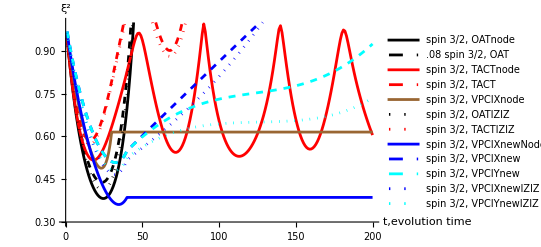

```mathematica
Plot7half2Newparameter=ListPlot[{OATnode,OAT,TACTnode,TACT,VPCIXnode,OATIZIZ,TACTIZIZ,VPCIXnewNode2,VPCIXnew,VPCIYnew,VPCIXnewIZIZ,VPCIYnewIZIZ},Joined->{True,True,True,True,True,True},PlotRange->{{0,200},{0.3,1}},PlotLegends->{"spin 3/2, OATnode",.08"spin 3/2, OAT","spin 3/2, TACTnode","spin 3/2, TACT","spin 3/2, VPCIXnode","spin 3/2, OATIZIZ","spin 3/2, TACTIZIZ","spin 3/2, VPCIXnewNode","spin 3/2, VPCIXnew","spin 3/2, VPCIYnew","spin 3/2, VPCIXnewIZIZ","spin 3/2, VPCIYnewIZIZ"},AxesLabel->{"t,evolution time","ξ^2"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed},Brown,{Black,Dotted},{Red,Dotted},Blue,{Blue,Dashed},{Cyan,Dashed},{Blue,Dotted},{Cyan,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

```mathematica
Export["E:\\desksave2\\Astro\\spin squeezing\\picture save\\Plot7half2Newparameter.pdf",Plot7half2Newparameter]
```

E:\desksave2\Astro\spin squeezing\picture save\Plot7half2Newparameter.pdf

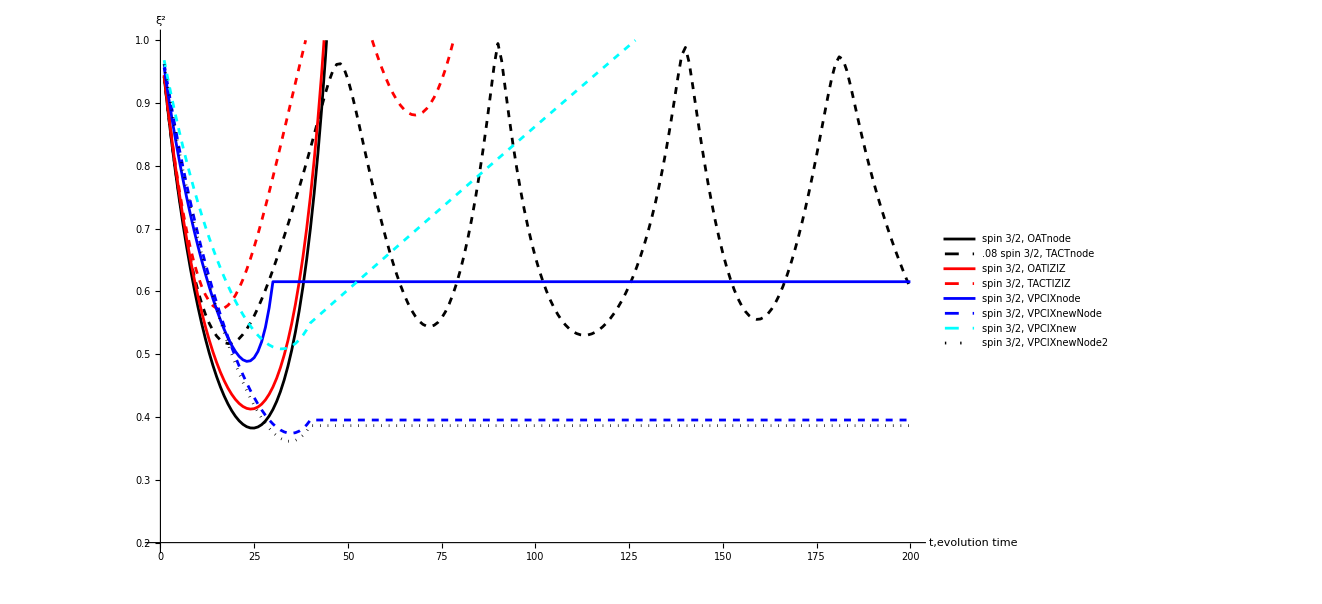

```mathematica
Plot7half2WithTACT=ListPlot[{OATnode,TACTnode,OATIZIZ,TACTIZIZ,VPCIXnode,VPCIXnewNode,VPCIXnew,VPCIXnewNode2},Joined->{True,True,True,True,True,True},PlotRange->{{0,200},{0.2,1}},PlotLegends->{"spin 3/2, OATnode",.08"spin 3/2, TACTnode","spin 3/2, OATIZIZ","spin 3/2, TACTIZIZ","spin 3/2, VPCIXnode","spin 3/2, VPCIXnewNode","spin 3/2, VPCIXnew","spin 3/2, VPCIXnewNode2","spin 3/2, OATIZIZ","spin 3/2, TACTIZIZ","spin 3/2, VPCIYIZIZ","spin 3/2, VPCIXIZIZ"},AxesLabel->{"t,evolution time","ξ^2"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed},Blue,{Blue,Dashed},{Cyan,Dashed},{Black,Dotted},{Red,Dotted},{Blue,Dotted},{Cyan,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```